# Mechanisms package

## Mechanisms package code

Last update: April 16, 2020
Christian D. Santangelo

```mathematica
BeginPackage["mechanisms`",{"Developer`"}];
```

```mathematica
(* 
	We need MeshRegion to work for this package to work.
*)
If[$VersionNumber<10,Print["Mathematica version may be too low."]];
```

```mathematica
(* 
	A snippet of code to test or a working C compiler, modified from
	https://mathematica.stackexchange.com/questions/39837/check-whether-a-working-ccompiler-is-installed
*)
If[Quiet[Check[TrueQ[Compile[{}, 0, CompilationTarget -> "C"][] == 0], False]],
  $compilationTarget = "C",
  Print["C compilation failed. Using MVM code instead."];
  $compilationTarget = "MVM"
];
```

### Version v1.09

```mathematica
$mechanismsVersion=1.1;
$mechanismsVersionText="mechanisms version 1.1";
```

### bugs or improvements

selfStresses[] does not have edge stiffnesses properly embedded into it.

Improving fixVertices[] to create proper constraint equations in 2D and 3D.

## Usage messages

### mechanism components

```mathematica
$mechanismComponents::usage="$mechanismComponents lists all valid components. $mechanismCompositeComponents lists composite mechanism components.";
$mechanismCompositeComponents::usage="$mechanismComponents lists all valid components. $mechanismCompositeComponents lists composite mechanism components.";
```

```mathematica
rigidBar::usage=
"rigidBar[{vertex 1, vertex 2}] represents a rigid bar. Use Options[rigidBar] to see valid properties.";
SetAttributes[rigidBar,NHoldFirst];

spring::usage="spring[{vertex 1, vertex 2}] represents a spring. Use Options[spring] to see valid properties.";
SetAttributes[spring,NHoldFirst];

joint::usage="joint[v] represents a freely rotating joint that is fixed in place. Use Options[joint] to see valid properties.";
SetAttributes[joint,NHoldFirst];

angleJoint::usage="angleJoint[{v1,v2,v3}] represents a torsional spring associated with the turning angle from vertex v1 to v2 to v3. Use Options[angleJoint] to see valid properties.";
SetAttributes[angleJoint,NHoldFirst];

fold::usage="fold[{v1,v2}] represents a fold with a torsional spring controlling its fold angle. Use Options[fold] to see valid properties.";
SetAttributes[fold,NHoldFirst];

vertexData::usage="vertexData[v] represents a vertex. Use Options[vertexData] to see valid properties.";
SetAttributes[vertexData,NHoldFirst];

edgeData::usage="edgeData[v] represents an edge. Use Options[edgeData] to see valid properties.";
SetAttributes[edgeData,NHoldFirst];

faceData::usage="faceData[v] represents a face. Use Options[faceData] to see valid properties.";
SetAttributes[faceData,NHoldFirst];

face::usage="face[{v1,...}] represents a face. Use Options[face] to see valid properties.";
SetAttributes[face,NHoldAll];
```

```mathematica
block::usage="block[{v1,...}] is a mechanism component that creates a \"block\" face made rigid by extra rigidBar elements.";
triangulatedFace::usage="triangulatedFace[{v1,...}] is a mechanism component that creates a triangulated face, with shortest diagonal triangulated first.";
flexibleBar::usage="flexibleBar[{v1,v2},n] is a mechanism component that creates a bar with n points between.";
```

### mechanism manipulators

```mathematica
framework::usage="framework[{{x1, y1}, {x2, y2}, ...}, {cell1[{i1,i2,..}], cell2[{j1,j2,...}], ...}] creates a linkage mechanism in 2D with vertex coordinates specified by the first argument and cells specified by the second..
framework[{{x1, y1, z2}, {x2, y2, z2}, ...}, {cell1[{i1,i2,..}], cell2[{j1,j2,...}], ...}] creates a linkage mechanism in 3D.";
origami::usage="origami[{{x1, y1}, {x2, y2}, ...}, {cell1[{i1,i2,..}], cell2[{j1,j2, ...}], ...}] creates an origami mechanism in 3D with vertex coordinates specified in 2D by the first argument and cells specified by the second..
origami[{{x1, y1, z2}, {x2, y2, z2}, ...}, {cell1[{i1,i2,..}], cell2[{j1,j2,...}], ...}] creates an origami mechanism in 3D.";

mechanismQ::usage="mechanismQ[m] returns True if m is a mechanism.";
```

```mathematica
polygonalLinkage::usage="polygonalLinkage[{vertex 1, vertex 2,...}] returns a polygonal linkage in which vertices are joined by rigid bars in cyclic order.";
```

```mathematica
boundaryVertices::usage=
"boundaryVertices[ mechanism ] returns a list of oriented boundary vertices { component 1, ...} where each boundary component is a list of vertex indices.
A boundary is defined as the boundary of a set of 2D faces.";

boundaryEdges::usage=
"boundaryEdges[ mechanism ] returns a list of oriented boundary components {{edge 1, edge 2, ...}, ...}. A boundary is defined as the boundary of a set of 2D faces.";

boundaryFaces::usage=
"boundaryFaces[ mechanism ] returns a list of oriented boundary components {{face 1, face 2, ...}, ...}. A boundary is defined as the boundary of a set of 2D faces.";

interiorVertices::usage=
"interiorVertices[ mechanism ] returns a list of interior vertices.";
interiorEdges::usage=
"interiorEdges[ mechanism ] returns a list of interior edges.";

listVertices::usage=
"listVertices[mechanism, {cell1, cell2,...}] lists the vertices associated with a list of cells.";

listEdges::usage=
"listEdges[mechanism, {cell1, cell2,...}] lists the edges (oriented if possible) associated with a list of cells.";

listFaces::usage=
"listFaces[mechanism, {cell1, cell2,...}] lists of the faces (oriented if possible) associated with a list of cells.";
```

```mathematica
joinMechanism::usage=
"joinMechanism[m1, m2, ...] creates a new mechanism by joining several individual ones. Overlapping vertices are identified if they fall within a specified precision.";
```

```mathematica
mechanismPositions::usage=
"mechanismPositions[ mechanism ] returns the coordinates of the vertices of mechanism.
mechanismPositions[ mechanism -> positions ] returns a new mechanism with coordinates given by positions.";
```

```mathematica
displayDimension::usage=
"displayDimension[ mechanism ] returns the display dimension.
displayDimension[ mechanism -> dim ] returns a mechanism with display dimension dim.";

embeddingDimension::usage=
"embeddingDimension[ mechanism ] returns the embedding dimension.
embeddingDimension[ mechanism -> dim ] returns a mechanism with embedding dimension dim.";
```

```mathematica
deleteVertices::usage="deleteVertices[m, {vertex 1, vertex 2,...}] deletes a list of vertices from a mechanism.";

deleteDanglingVertices::usage="deleteDanglingVertices[m,type] deletes all vertices of m not adjacent to a cell of a specific type, either \"faces\" or \"edges\".
If omitted, the argument type defaults to \"faces\" for origami or \"edges\" for frameworks. See: deleteVertices[]";
```

```mathematica
tesselateMechanism::usage=
"tesselateMechanism[mechanism, {primitive vectors}, {nx,ny} ],tesselateMechanism[mechanism, {primitive vectors}, {nx,ny,nz} ] tesselates a mechanism using a set of 2D or 3D primitive vectors.";
```

```mathematica
saveToFOLD::usage="saveToFOLD[mechanism, filename] saves a FOLD file from a mechanism.";
loadFromFOLD::usage=
"loadFromFOLD[filename] loads a mechanism from a FOLD. Use option \"face\" to choose how to treat a polygon.";
```

```mathematica
alignMechanism::usage="alignMechanism[point list 1, point list 2] aligns point list 2 with point list 1 using only Euclidean motions.
alignMechanism[point list 1, mechanism] aligns a mechanical with point list 1 using Euclidean motions.
alignMechanism[mechanism 1, mechanism 2] aligns mechanism 2 to mechanism 1 using Euclidean motions.";
```

```mathematica
displaceVertices::usage="displaceVertices[mechanism,{v1 -> vector1,...}] returns a mechanism with vertices having index {v1, ...} displaced by a vector.";
```

```mathematica
dataForm::usage="dataForm[cell type] returns a list of data elements in the order they appear as components.";
```

```mathematica
modifyMechanism::usage="modifyMechanism[mechanism, action 1 -> data 1, ...] modifies a mechanism. Use modifyMechanism[\"Methods\"] for valid actions.";
```

```mathematica
mechanismComponents::usage=
"mechanismComponents[ mechanism, pattern ] returns the components matching pattern.
mechanismComponents[ mechanism, pattern1-> {property1->data1,...}, ...] changes components matching pattern by adding, if possible the property specified.";
```

```mathematica
deleteCells::usage=
"deleteCells[mech, pattern] deletes cells that match a pattern.
deleteCells[pattern] is a form of deleteCells[] that can act on a mechanism.";

deleteData::usage=
"deleteData[mech, pattern] deletes the data associated with a pattern.
deleteData[pattern] is a form of deleteData[] that can act on a mechanism.";

addCells::usage="addCells[m, {cell1[{i1, i2, ...}], ...}] adds cells to a mechanism.";
```

### infinitesimal, vertexPosition, vertexDisplacement functions

```mathematica
infinitesimal::usage=
"infinitesimal[name, order] represents an infinitesimal quantity that will be automatically expanded to a particular order.";
SetAttributes[infinitesimal,{NHoldAll,Constant}]
```

```mathematica
vertexPosition::usage=
"vertexPosition[vertex, component] represents the displacement of vertex v along a particular component, which is one of \"x\", \"y\", or \"z\" or All[d] where d is the dimension.
vertexPosition[{vertex 1, vertex 2,...},{component 1, component 2,...}] returns a nested list of positions and components.";
SetAttributes[vertexPosition,{NHoldAll,Constant}]

vertexDisplacement::usage=
"vertexDisplacement[vertex, component] represents the displacement of vertex v along a particular component, which is one of \"x\", \"y\", or \"z\" or All[d] where d is the dimension.
vertexDisplacement[{vertex 1, vertex 2,...},{component 1, component 2,...}] returns a nested list of displacements and components.";
SetAttributes[vertexDisplacement,{NHoldAll,Constant}]
```

```mathematica
to3D::usage="to3D[vertices] embeds a list of coordinates into 3D.";
to2D::usage="to2D[vertices] projects a list of coordinates into 2D.";
toDim::usage="toDim[d][vertices] projects a list of coordinates into d dimensions.";
```

```mathematica
randomDisplacements::usage=
"randomDisplacements[ d, n ] creates a random displacement for n vertices in d dimensions.
randomDisplacements[mechanism] returns vertex positions that are randomly displaced from the mesh positions.";
```

```mathematica
orthogonalizeDisplacements::usage=
"orthogonalizeDisplacements[ {displacement 1, displacement 2, ...}(, tolerance) ] returns an orthogonalized set of vertex displacements using optional tolerance.";
```

```mathematica
dataRules::usage="dataRules[vertexPosition|vertexDisplacement, positions/displacements ] returns rules assigning positions or displacements to vertexPosition/vertexDisplacement head.";
```

```mathematica
displacements::usage="displacements[expression] returns a list of vertexDisplacement[] objects in the expression.";
parameters::usage="parameters[expression] returns a list of variables that are not vertexDisplacement[] objects in the expression.";
```

### geometrical measures

```mathematica
displacementVector::usage=
"displacementVector[ positions, edge ] returns the vector pointing along an oriented edge.
displacementVector[ positions, { edge 1, edge 2, ...} ] returns list of displacement vectors.
Edges can be specified as Line[{v1,v2}] or {v1,v2}.";

displacementLength::usage=
"displacementLength[ positions, edge 1 ] returns the length of an edge.
displacementLength[ positions, { edge 1, edge 2, ...} ] returns lengths of a list of edges.
Edges can be specified as Line[{v1,v2}] or {v1,v2}.";

displacementLengthSquared::usage=
"displacementLengthSquared[ positions, edge 1 ] returns the squared length of an edge.
displacementLengthSquared[ positions, { edge 1, edge 2, ...} ] returns squared lengths of a list of edges.
Edges can be specified as Line[{v1,v2}] or {v1,v2}.";

vectorAngle::usage=
"vectorAngle[ positions, {vertex 1, vertex 2, vertex 3}] returns the angle at vertex 2 spanned by the other two points.
vectorAngle[ positions, { triple 1, triple 2, ...} ] returns the vertex angles anong a list of vertex triples.";

turningAngle::usage=
"turningAngle[ positions, {vertex 1, vertex 2, vertex 3}] returns the turning angle at vertex 2 spanned by the other two points.
turningAngle[ positions, { triple 1, triple 2, ...} ] returns the turning angles anong a list of vertex triples.";

normalVector::usage=
"normalVector[ positions, {vertex 1, vertex 2, vertex 3} ] returns the vector normal to the plane spanned by the three points.
normalVector[ positions, { triple 1, triple 2, ...} ] returns vectors normal to the plane spanned by the list of triples.
normalVector[ positions, polygon ] returns the vector normal to a polygon.
normalVector[ positions, {polygon 1, polygon 2, ...} ] returns the vectors normal to a list of polygons.";

planarAngle::usage=
"planarAngle[positions, {v1, v2, v3}] returns the oriented angle at vertex v2 spanned by the other two vertices.
planarAngle[positions, {triple 1, triple 2, ...}] returns the oriented angles at for each triple of verticles.";

foldAngle::usage=
"foldAngle[ mesh, positions, edge ] returns the fold angle along an edge.
foldAngle[ mesh, positions,{edge 1, edge 2,...} ] returns the fold angle of a list of edges.";

gaussianCurvature::usage=
"gaussianCurvature[ mesh, positions,vertex ] returns the discrete Gaussian curvature of vertex.
gaussianCurvature[ mesh, positions,{vertex 1, vertex 2, ...} ] returns the discrete Gaussian curvature of a list of vertices.
gaussianCurvature[ mesh, metric,{vertex 1, vertex 2, ...} uses a metric to explicitly compute the Gaussian curvature at each vertex.";
```

```mathematica
congruentQ::usage="congruentQ[p1,p2] tests whether the two vectorPositions are related by a rigid transformation.
congruentQ[p1,p2,tolerance] tests whether the two vectorPositions are related by a rigid transformation.
congruentQ[tolerance] is a function that can check the positions between two vertexPosition configurations.";
```

### origami functions

```mathematica
kawasakiQ::usage=
"kawasakiQ[origami] returns True if it can be determined that the origami satisfies Kawasaki's theorem at each vertex.
Use option ZeroTest to modify how the function tests for zero. Use option WorkingPrecision to set a number of digits for the test.";
```

```mathematica
foldMatrix::usage=
"foldMatrix[origami] returns the fold matrix mapping linear vertex displacements to linear fold angle changes.";

angularFoldMatrix::usage=
"angularFoldMatrix[origami, (positions, ) vertex] returns the angular fold matrix of a vertex mapping the angular displacements of the folds from the xy plane to the fold angle changes.";
```

```mathematica
toOrigami::usage=
"toOrigami[ object ] converts an object to an origami mechanism. Effectively this only works for some MeshRegion[] or framework[] objects.";
```

```mathematica
singleVertex::usage=
"singleVertex[ {angle 1, angle 2, ...} ] returns a single vertex origami with angles as sector angles.
singleVertex[ {angle 1, angle 2, ...}, {length 1, ...} ] returns a single vertex origami with angles as sector angles and fold lengths given by the list of lengths.

See options \"angles\" and \"torsional stiffnesses\" to set the equilibrium angles and torsional stiffnesses.";

randomOrigami::usage=
"randomOrigami[ n ] returns random origami with n internal vertices.";

miuraOri::usage=
"miuraOri[ angle ] returns a Miura ori at a particular angle.";
```

```mathematica
flatOrigamiQ::usage=
"flatOrigamiQ[ origami ] returns True if the origami mechanism is flat.
Use option ZeroTest to specify how to test for zero. Use option WorkingPrecision to choose the precision.";
```

```mathematica
yoshimuraOrigami::usage=
"yoshimuraOrigami[{# azimuthal cells, # of rings(, twist)},overall scale, height ratio] creates a Yoshimura fold pattern of a particular radius, height, and integer twist if specified.";
```

### isometry functions

```mathematica
fixVertices::usage=
"fixVertices[mechanism, {v1,v2,...}] returns a list of rules for displacements that keep a list of vertices fixed.";
```

```mathematica
constraintMatrix::usage="constraintMatrix[mechanism (,positions)] returns the matrix associated with all linear constraints in a mechanism.
Use option \"constraints\" to set additional constraints.";

compatibilityMatrix::usage="compatibilityMatrix[mechanism (, positions)] returns the compatibility matrix associated with the rigid bars of a mechanism.
It is slightly faster than constraintMatrix[] when a mechanism only has rigid bars.";
```

```mathematica
constraintEquations::usage=
"constraintEquations[mechanism(, positions), order] returns constraint equations valid to some order in the displacements.
order should be 1, 2 or Infinity. Use option \"constraints\" to set additional constraints.";
```

```mathematica
selfStresses::usage=
"selfStresses[mechanism (,positions)] returns a list of self stresses based on the rigid bars in the structure.";
```

```mathematica
infinitesimalMotions::usage=
"infinitesimalMotions[mechanism(, positions)] returns a list of two elements: an infinitesimal linear motion and, if necessary, a list of quadratic constraints they must satisfy.

Use option \"variables\" to control the form of the output.";
```

```mathematica
isometricTrajectory::usage=
"isometricTrajectory[mechanism, {{Δx1, Δy1, ..}, ..}, n] creates a trajectory using n steps through the configuration space of a mechanism starting in the
displacement direction {{Δx1, Δy1, ..}, ..}.";
```

### simulations

```mathematica
$defaultStiffness::usage="$defaultStiffness[component] returns the default stiffness in case the constraint is rigid.
Use $defaultStiffness[\"constraints\"] to find the stiffness of added constraints.";
```

```mathematica
mechanismEnergy::usage=
"mechanismEnergy[ mechanism ] returns an energy expression for a mechanism.
mechanismEnergy[ mechanism, positions ] returns an energy expression assuming a set of vertex positions.";
```

```mathematica
compiledMechanismEnergy::usage=
"compiledMechanismEnergy[ mechanism ] compiles an energy and gradient for a mechanism.
compiledMechanismEnergy[ mechanism, positions ] compiles an energy and gradient for a mechanism starting from a set of positions.

Undefined symbols in the energy must be set using ReplaceAll[].";
```

```mathematica
minimizeEnergy::usage=
"minimizeEnergy[ mechanism, energy ] minimizes the energy of a mechanism. energy can be a compiled mechanism energy.";
```

```mathematica
repeatedMinimizeEnergy::usage=
"repeatedMinimizeEnergy[mechanism, energy, number] minimizes the energy number times using random initial conditions.
repeatedMinimizeEnergy[mechanism,energy,number,test value] uses a numeric test value to determine if two vertex positions are the same.
repeatedMinimizeEnergy[mechanism,energy,number,test function] uses a test function to determine if two vertex positions are the same.";
```

```mathematica
tallyRepeatedMinimizeEnergy::usage=
"tallyRepeatedMinimizeEnergy[mechanism, energy, number] minimizes the energy number times using random initial conditions and tallies the results.
tallyRepeatedMinimizeEnergy[mechanism,energy,number,test value] uses a numeric test value to determine if two vertexPositions are the same.
tallyRepeatedMinimizeEnergy[mechanism,energy,number,test function] uses a test function to determine if two vertexPositions are the same.";
```

```mathematica
orthogonalComplement::usage="orthogonalComplement[basis] returns an orthonormal basis for the orthogonal complement of the vector space spanned by basis.
orthogonalComplement[basis,f] returns an orthonormal basis for the complement of the vector space spanned by basis using inner product function f.
Options are the same as Orthogonal.";
```

```mathematica
findMinimalTrajectory::usage=
"findMinimalTrajectory[mechanism, start, end, n] attempts to find a valid trajectory from start to end configurations using n intermediate steps.";
```

```mathematica
dynamicalSystem::usage=
"dynamicalSystem[m,{initial positions, initial velocities}, {time variable, start time, end time}] returns a list of functions specifying how vertices will move as a function of time.

Use options \"mass\" and \"drag\" to set the mass and drag coefficient for the particles.";
```

```mathematica
dynamicalSystemEquations::usage=
"dynamicalSystemEquations[mech, {variable, time}] returns dynamical equations for vertex positions, using variable as vertex names, and time as the symbol for time.

Use options \"mass\" and \"drag\" to set the mass and drag coefficient for the particles.";
```

### graphics

```mathematica
mechanismPrimitives::usage=
"mechanismPrimitives[mechanism] returns a list of mechanism primitives.
mechanismPrimitives[mechanism,positions] returns a list of mechanism primitives with vertices at positions.
mechanismPrimitives[mechanism,positions, cellspec] returns a list of mechanism primitives with vertices at positions and cells specified by cellspec.";
```

```mathematica
toGraphics::usage="toGraphics[mechanism (,positions)] converts a mechanism to graphics.
toGraphics[mechanism, positions, cellspec] converts mechanism components matching cellspec to graphics.";
```

```mathematica
toMeshRegion::usage="toMeshRegion[mechanism,positions] attempts to convert a mechanism to a MeshRegion object.";
```

```mathematica
plotMechanism::usage=
"plotMechanism[ mechanism, positions ] plots a mechanism using positions.
plotMechanism[mechanism, {positions 1, positions 2,...}] creates a list of plotted mechanisms with uniform size.";
```

```mathematica
plotDisplacement::usage=
"plotDisplacement[ mechanism, vertex displacements ] plots mechanism with arrows correspond to vertex displacements overlayed.";
plotTension::usage=
"plotTension[ mechanism, edges->tesions ] plots tensions on the edges of a mechanism.";
```

```mathematica
angleMarker::usage="angleMarker[m, {v1,v2,v3}, (radius) ] creates an arc around an angle spanning (v1,v2) to (v3,v2).";
angleText::usage="angleTest[m, {v1,v2,v3}, (distance) ] adds a text label to the angle spanning (v1,v2) to (v3,v2).";
```

### linkages

```mathematica
toFramework::usage=
"toFramework[ mesh ] attempts to create a linkage from a mesh.";
```

```mathematica
KLChainUnitCell::usage="KLChainUnitCell[a,r,θ] returns a unit cell of the KLchain with spacing a, bar length r and equilibrium angle for the first bar θ.";
```

```mathematica
HennebergOperation::usage="HennebergOperation[m, {move1, move2,...}] takes a list of Henneberg moves specified as either 1 or 2 and performs them on a 2D mechanism m.";
```

### periodicity tools

```mathematica
periodicData::usage="periodicData[] contains data needed to compute for a periodic mechanism.";
periodicityRules::usage=
"periodicityRules[mechanism, periodic data, vertexPosition|vertexDisplacement, maps] returns a list of rules mapping either vertexPosition or vertexDisplacement data associated with the periodic data of a mechanism.";
identificationRules::usage="identificationRules[mechanism, {map1,...}] finds the equivalence classes of vertices that are overlapping under a set of maps";
```

```mathematica
periodicEquivalenceClasses::usage="periodicEquivalenceClasses[m,periodic data,elements] groups elements of mechanism m into classes related by being periodic images.";
```

```mathematica
Begin["`Private`"];
```

### $mechanismComponents, $mechanismCompositeComponents

```mathematica
$meshRegionProperties={MeshCellStyle,MeshCellLabel,MeshCellShapeFunction};
```

```mathematica
$mechanismComponents={rigidBar,spring,joint,fold,vertexData,edgeData,angleJoint};
$mechanismCompositeComponents={block,flexibleBar,triangulatedFace};
```

### mechanismQ[], mechanismPattern

```mathematica
mechanismQ[_framework|_origami]:=True
mechanismQ[_]:=False
```

```mathematica
mechanismPattern=_framework|_origami;
```

### dataForm[]

```mathematica
dataForm[rigidBar]:={"length","stiffness"}
dataForm[spring]:={"length","stiffness","force"}
dataForm[joint]:={"position","components","stiffness"}
dataForm[fold]:={"angle","torsionalStiffness"}
dataForm[vertexData]:={"label","data"}
dataForm[edgeData]:={"label","data"}
dataForm[angleJoint]:={"angle","angularStiffness"}
dataForm[_]:={}
```

## tools

### general tools

#### overlappingVertices[]

overlappingVertices[positions 1, positions 2] returns a list of which vertices listed in 1 can be found in 2.

```mathematica
(* 
	overlappingVertices returns a list of which vertices in the first set of positions can be
	identified in the second set.
*)
overlappingVertices[positions1_?MatrixQ,positions2_?MatrixQ]/;Dimensions[positions1]==Dimensions[positions2]:=
With[
{
	allPairs=Tuples[{Range[Length[positions1]],Range[Length[positions2]]}],
	zeroTest=(Chop[# . #]==0&)
},
	Rule@@@Select[
		allPairs,
		zeroTest[positions1[[#[[1]]]]-positions2[[#[[2]]]]]&
	]
]
```

#### orthogonalComplement

```mathematica
Options[orthogonalComplement]=Options[Orthogonalize];
orthogonalComplement::notmat="Not all elements of basis have the same dimension.";
orthogonalComplement::notind="Basis is not linearly independent.";
```

```mathematica
basisQ[array_?MatrixQ]:=MatrixRank[array]==Dimensions[array][[1]]
basisQ[_]:=(Message[orthogonalComplement::notmat]; False)
```

```mathematica
orthogonalComplement[array_?basisQ,opt:OptionsPattern[]]:=
Select[Drop[
	Orthogonalize[Join[array,IdentityMatrix[Dimensions[array][[2]]]],opt],
	Dimensions[array][[1]]
],# . #>0&]
orthogonalComplement[array_?basisQ,inn_,opt:OptionsPattern[]]:=
Select[Drop[
	Orthogonalize[Join[array,IdentityMatrix[Dimensions[array][[2]]]],inn,opt],
	Dimensions[array][[1]]
],# . #>0&]

orthogonalComplement[__]:="nothing" /; Message[orthogonalComplement::notind]
```

#### projectOut,projectTo

```mathematica
(* returns a projection operator to project out the array *)
projectOut[array_?MatrixQ]:=With[
{oarray=Orthogonalize[array]},
IdentityMatrix[Dimensions[array][[2]]] - Transpose[oarray] . oarray
]
```

```mathematica
(* returns a projection operator to project in the array *)
projectTo[array_?MatrixQ]:=With[
{oarray=Orthogonalize[array]},
Transpose[oarray] . oarray
]
```

#### displacements[],parameters[]

```mathematica
displacements[expr_]:=Cases[Variables[expr],_vertexDisplacement]
parameters[expr_]:=DeleteCases[Variables[expr],_vertexDisplacement]
```

#### realQ[]

```mathematica
realQ[data_]:=(Chop[#.#]==0 &) @ Im[Flatten[{data}]]
```

#### orderPairs[]

orderPairs[{{n1, n2}, {n3, n4}, ...}]
 When provided a list of pairs, {1, b}, sort them in order such that {{1, 2}, {2, 3}, {3, 4}, ...}
 
 orderPairs[list 1, list 2] orders pairs in which elements of each list are paired with
 the corresponding element.

```mathematica
orderPairs[{}]:={}
orderPairs[pairList_?(MatrixQ[#,IntegerQ]&)]:=
	orderPairsTopologicalSort[Graph[UndirectedEdge@@@pairList]]/; Dimensions[pairList][[2]]==2

orderPairs[pairList_,correspondingList_]:=
With[
{
association=Dispatch@Thread[pairList->correspondingList]
},
	orderPairs[pairList]/.association
]/; Length[pairList]==Length[correspondingList]
```

```mathematica
(* this does a topological sort on a graph *)
orderPairsTopologicalSort[g_?AcyclicGraphQ]:=Partition[TopologicalSort[DirectedEdge@@@EdgeList[g]],2,1]
orderPairsTopologicalSort[g_Graph]:=List@@@(First@FindCycle[g,Infinity,1])
```

#### rotateTo[]

```mathematica
rotateTo[s_List,v_]:=With[{pos=FirstPosition[s,v]},If[MissingQ[pos],s,RotateLeft[s,pos[[1]]-1]]]
rotateTo[h_[s_List],v_]:=h[rotateTo[s,v]]
```

### MeshRegion tools

These are tools I’ve designed to work with MeshRegions. MeshRegions are how I typically handle the graphical elements of mechanisms.

#### distributePropertyTag[]

```mathematica
distributePropertyTag[data_]:=
	Module[{x,y,z},
		Flatten[data//.{
			Property[x_,{}]:>x,
			Property[x_List,y_]:>(Property[#,y]&/@x),
			Property[Property[x_,y_],z_]:>Property[x,Join[Flatten@{{y},{z}}]]
		}]
	]
```

#### orderFaces[]

```mathematica
orderFaces[faceList_,v_Integer]:=orderPairs[{#[[2]],Last[#]}&/@faceList,faceList]
```

#### rotateCells[]

```mathematica
Options[rotateCells]={"Flatten"->True};
```

```mathematica
rotateCells[cells_,OptionsPattern[]]:=With[
{sortedCells=GatherBy[cells,Length]},
	Flatten[NestList[RotateLeft[#,{0,1}]&,#,Length[#[[1]]]-1]&/@sortedCells,2]
]/;OptionValue["Flatten"]
```

```mathematica
rotateCells[cells_,OptionsPattern[]]:=With[
{sortedCells=GatherBy[cells,Length]},
	First[NestList[RotateLeft[#,{0,1}]&,#,Length[#[[1]]]-1]&/@sortedCells]
]/;Not[OptionValue["Flatten"]]
```

#### connectivity[]

```mathematica
connectivity["Methods"]:={{"vertices","edges","faces"}->{"vertices","edges","faces","ordered faces","ordered edges"}};
```

```mathematica
(*
connectivity[surf,"faces"->"vertices"];//RepeatedTiming
0.0079s on {7445,22105,14661} triangulated vertices, edges and faces
*)
connectivity[m_?MeshRegionQ,Rule["faces","vertices"]]:=
	MeshCells[m,2][[All,1]]
```

```mathematica
rotateThroughFaces[faces_]:=Flatten[NestList[RotateLeft[#,{0,1}]&,faces,Last[Dimensions[faces]]-1],1]
connectivity[m_MeshRegion,Rule["vertices","faces"]]:=With[
{faces=rotateThroughFaces[MeshCells[m,2][[All,1]]]},
	GatherBy[
		Join[
			Transpose[{Range[MeshCellCount[m,0]]}], (*make a list of vertices in order of the form {{1},{2},...}*)
			faces
		],
	First][[All,2;;]]
]
```

```mathematica
(* 
geometry`Private`connectivity[surf,"faces"->"edges"];//RepeatedTiming
0.036s on {12289,36571,24283} triangulated vertices, edges and faces

Added ToPackedArray[] which ever so slightly speeds this function up. Since Transpose[]
packs arrays, it must speed up the operation of Transpose[] itself.
*)
connectivity[m_?MeshRegionQ,Rule["faces","edges"]]:=
With[{cells=Transpose[ToPackedArray[MeshCells[m,2][[All,1]]]]},
	Flatten[Partition[Transpose[Join[cells,{cells[[1]]}]],{1,2},1],{3}][[1]]
]

(* 
geometry`Private`connectivity[surf,"faces"->"edges"];//RepeatedTiming
0.19s on {7445,22105,14661} triangulated vertices, edges and faces
*)
connectivity[m_MeshRegion,Rule["edges","faces"]]:=With[
{edges=MeshCells[m,1][[All,1]],faces=MeshCells[m,2][[All,1]]},
	GatherBy[Flatten[{edges,rotateCells[faces]},1],Sort[#[[1;;2]]]&][[All,2;;]]
]
```

```mathematica
(*
geometry`Private`connectivity[surf,"edges"->"vertices"];//RepeatedTiming
0.015s on {8236,24449,16214} triangulated vertices, edges and faces
*)
connectivity[m_?MeshRegionQ,Rule["edges","vertices"]]:=
	MeshCells[m,1][[All,1]]

(*
geometry`Private`connectivity[surf,"vertices"->"edges"];//RepeatedTiming
0.032s on {8236,24449,16214} triangulated vertices, edges and faces
*)
connectivity[m_?MeshRegionQ,Rule["vertices","edges"]]:=With[
{edges=MeshCells[m,1][[All,1]]},
	SortBy[GatherBy[Flatten[{edges,Reverse[edges,{2}]},1],First],First]
]
```

```mathematica
(* 
geometry`Private`connectivity[surf,"edges"->"ordered faces"];//RepeatedTiming
0.81s on {24731,73776,49046} triangulated vertices, edges and faces

This function unpacks packed arrays.
*)
connectivity[m_MeshRegion,Rule["edges","ordered faces"]]:=
With[
{
test1=connectivity[m,"vertices"->"faces"],
edges=Transpose[MeshCells[m,1][[All,1]]]
},
	ToPackedArray@MapThread[
		Join[#1,#2]&,
		{
		MapThread[Cases[#1,{__,#2}]&,{test1[[edges[[1]]]],edges[[2]]}],
		MapThread[Cases[#1,{_,#2,__}]&,{test1[[edges[[1]]]],edges[[2]]}]
		}
	]
]
```

```mathematica
(*
geometry`Private`connectivity[surf,"vertices"->"ordered faces"];//Timing
0.90s on {7445,22105,14661} triangulated surface.

Unpacks lists.
*)
connectivity[m_MeshRegion,Rule["vertices","ordered faces"]]:=With[
{unorderedFace=connectivity[m,"vertices"->"faces"]},
	MapThread[orderFaces,{unorderedFace,Range[Length[unorderedFace]]}]
]
```

```mathematica
(*
geometry`Private`connectivity[surf,"vertices"->"ordered edges"];//Timing
0.912s on {7445,22105,14661}

Unpacks lists.
*)
connectivity[m_?MeshRegionQ,Rule["vertices","ordered edges"]]:=
	connectivity[m,"vertices"->"ordered faces"][[All,All,1;;2]]
```

```mathematica
connectivity::badcombo="Methods are not recognized in this combination.";
connectivity[m_MeshRegion,Rule[_,_]]:="nothing" /; Message[connectivity::badcombo]
```

#### boundaryVertices[] boundaryEdges[] boundaryFaces[]

```mathematica
boundaryEdges[m_MeshRegion]:=
Module[
{
	facePairs=connectivity[m,"edges"->"faces"],
	edges=MeshCells[m,1][[All,1]],
	boundary
},
	boundary=Pick[edges,Length/@facePairs,1];
	If[Length[boundary]==0,
		{},
		Map[List@@#&,FindCycle[Graph[boundary],Infinity,All],{2}]
	]
]
```

```mathematica
boundaryVertices[m_MeshRegion]:=Map[First@@#&,boundaryEdges[m],{2}]
```

```mathematica
boundaryFaces[m_MeshRegion]:=Module[{i},
With[{boundary=boundaryVertices[m],faces=MeshCells[m,2][[All,1]]},
	Table[Select[faces,ContainsAny[boundary[[i]],#]&],{i,1,Length[boundary]}]
]]
```

#### interiorEdges[] interiorVertices[]

```mathematica
interiorEdges[mr_MeshRegion]:=
	Pick[
		MeshCells[mr,1][[All,1]],
		Length/@connectivity[mr,"edges"->"faces"],
		2
	]
```

```mathematica
interiorVertices[mr_MeshRegion]:=
Complement[
	DeleteDuplicates[Flatten[interiorEdges[mr]]],
	Flatten@boundaryVertices[mr]
]
```

#### deformMesh[]

```mathematica
inactiveForm[expr_]:=With[{head=Head[expr]},
	ReleaseHold[Uncompress[Compress[expr],Hold]/.head:>Inactive[head]]
]
```

```mathematica
deformMesh[m_MeshRegion,pos_?numericCoordinatesQ]:=
	Activate[
		ReplacePart[inactiveForm[m],1->pos]
	]/;MeshCellCount[m,0]==Length[pos]
deformMesh[m_compiledMeshRegion,pos_?numericCoordinatesQ]:=
	ReplacePart[m,1->deformMesh[m["mesh"],pos]]
```

```mathematica
deformMesh::badpos="Number of vertices in positions not the same as in the MeshRegion.";
deformMesh::badnum="Displacements are not valid or numeric.";

deformMesh[m_MeshRegion,pos_?numericCoordinatesQ]:="nothing"/;Message[deformMesh::badpos]
deformMesh[m_MeshRegion,p_]:="nothing"/;Message[deformMesh::badnum]
```

#### meshCells[]

```mathematica
meshCells[mr_MeshRegion]:=Module[
{i},
	distributePropertyTag[Flatten@Table[Property[
		MeshCells[mr,{i,#}],DeleteCases[{
		MeshCellStyle->PropertyValue[{mr,{i,#}},MeshCellStyle],
		MeshCellShapeFunction->PropertyValue[{mr,{i,#}},MeshCellShapeFunction],
		MeshCellLabel->PropertyValue[{mr,{i,#}},MeshCellLabel]
	},Rule[_,Automatic]]]&/@Range[MeshCellCount[mr,i]],{i,0,2}]]
]
```

```mathematica
meshCells[mr_MeshRegion,i_Integer]:=
	distributePropertyTag[Flatten@Property[
		MeshCells[mr,{i,#}],DeleteCases[{
		MeshCellStyle->PropertyValue[{mr,{i,#}},MeshCellStyle],
		MeshCellShapeFunction->PropertyValue[{mr,{i,#}},MeshCellShapeFunction],
		MeshCellLabel->PropertyValue[{mr,{i,#}},MeshCellLabel]
	},Rule[_,Automatic]]]&/@Range[MeshCellCount[mr,i]]]
```

#### orientedQ[]

```mathematica
orientedQ[mr:_MeshRegion|_compiledMeshRegion]:=
	AllTrue[
		DeleteCases[connectivity[mr,"edges"->"faces"],{_}],
		facePairOrientedQ
	]
orientedQ[_]:=False
```

```mathematica
facePairOrientedQ[{v1_,v2_}]:=With[
{
	eg2=Take[RotateLeft[v2,#],2]&/@Range[Length[v2]],
	eg1=Reverse[Take[RotateLeft[v1,#],2]]&/@Range[Length[v1]]
},
	ContainsAny[eg1,eg2]
]
facePairOrientedQ[v1_,v2_]:=With[
{
	eg2=Take[RotateLeft[v2,#],2]&/@Range[Length[v2]],
	eg1=Reverse[Take[RotateLeft[v1,#],2]]&/@Range[Length[v1]]
},
	ContainsAny[eg1,eg2]
]
```

### vertex displacement tools

#### listParameters[],expandExpression[]

This is used to control automatic expansion of infinitesimal quantities to various orders. It is often cleaner to do this than to use Series[] when expressions are long.

```mathematica
listParameters[expr_]:=DeleteDuplicates[(Extract[expr,#]&)/@Position[List@@expr,infinitesimal[_,_]]]
```

```mathematica
(*
	This basically does what Series[] does in a somewhat dumber way.
	It won't handle limits as nicely as Series[] but it typically presents results that look
	more useful for analytic expressions.
*)
expandExpression[expr_,param_]:=Module[
{i,tmp},
	Total[Table[(tmp@@param)^i D[expr,{param,i}]/(i!),{i,0,param[[2]]}]/.param->0]/.tmp->infinitesimal
]
expandExpression[expr_?NumericQ]:=expr
expandExpression[expr_]:=With[{params=listParameters[expr]},
	Fold[expandExpression,expr,Reverse@params]
]
```

#### orthogonalizeDisplacements[]

```mathematica
orthogonalizeDisplacements[displacements_?ArrayQ,tol:_?NumericQ:10^(-8)]:=
With[{dim=Dimensions[displacements][[3]],tolsq=tol^2},
	Partition[#,dim]&/@Select[Orthogonalize[Flatten/@displacements,Tolerance->tol],#.#>tolsq&]
]/;Length[Dimensions[displacements]]==3
```

```mathematica
orthogonalizeDisplacements::notdispl="Not a list of valid vertex displacements of the same dimension.";
orthogonalizeDisplacements::tol="Tolerance must be numeric.";

orthogonalizeDisplacements[displacements_?ArrayQ,___]:="nothing"/;Message[orthogonalizeDisplacements::notdispl]
orthogonalizeDisplacements[displacements_?ArrayQ,_]:="nothing"/;Message[orthogonalizeDisplacements::tol]
```

#### normalizeDisplacement[]

```mathematica
normalizeDisplacement[displacement_?MatrixQ]:=Partition[Normalize[Flatten[displacement]],Last[Dimensions[displacement]]]
```

### defining mechanism components

#### componentData[]: extracting data from fundamental cells

```mathematica
evaluateData[{Automatic,d_}]:=d
evaluateData[{x_,d_}]:=x
```

spring

```mathematica
componentData["stiffness", m_, positions_, spring[indices_,data_] ]:=data[[All,2]]

componentData["length",m_,positions_,spring[indices_,data_]]:=
With[{lengths=Sqrt[displacementLengthSquared[positions,indices]],prescribedLengths=data[[All,1]]},
	evaluateData /@ Transpose[{prescribedLengths,lengths}]
]

componentData["force",m_,positions_,spring[indices_,data_]]:=data[[All,3]] /. "harmonic"->((#1-#2)^2/2&)
```

rigidBar

```mathematica
componentData["stiffness",m_,positions_,rigidBar[indices_,data_]]:=data[[All,2]]

componentData["length",m_,positions_,rigidBar[indices_,data_]]:=
With[{lengths=Sqrt[displacementLengthSquared[positions,indices]],prescribedLengths=data[[All,1]]},
	evaluateData /@ Transpose[{prescribedLengths,lengths}]
]
```

fold

```mathematica
componentData["torsionalStiffness",m_,positions_,fold[indices_,data_]]:=Last/@data
componentData["angle",m_,positions_,fold[indices_,data_]]:=With[{angles=First/@data},With[
{automaticIndices=indices[[ Pick[Range[Length[indices]],angles,Automatic] ]]},
	If[Length[automaticIndices]>0,
		indices/.Dispatch@Thread[automaticIndices->foldAngle[m,positions,automaticIndices]]/.Dispatch@Thread[indices->angles],
		angles
	]
]]
```

angleJoint

```mathematica
componentData["angularStiffness",m_,positions_,angleJoint[indices_,data_]]:=Last/@data

componentData["angle",m_,positions_,angleJoint[indices_,data_]]:=
With[{angles=data[[All,1]]},With[
{automaticIndices=indices[[ Pick[Range[Length[indices]],angles,Automatic] ]]},
	If[Length[automaticIndices]>0,
		(indices/.Dispatch[Thread[automaticIndices->turningAngle[positions,automaticIndices]]])/.Dispatch@Thread[indices->angles],
		angles
	]
]]
```

joint

```mathematica
componentData["stiffness",m_,positions_,joint[indices_,data_]]:=data[[All,3]]

componentData["components",m_,positions_,joint[indices_,data_]]:=With[{
allMeaning=Switch[embeddingDimension[m],
	3,{"x","y","z"},
	2,{"x","y"},
	_,{}
]},
	data[[All,2]]/.All->allMeaning
]

computePosition[index_,Automatic,pos_]:=pos[[index]]
computePosition[index_,specified_,pos_]:=specified

componentData["position",m_,positions_,joint[indices_,data_]]:=With[{pos=data[[All,1]]},
	MapThread[computePosition[#1,#2,positions]&,{indices,pos}]
]
```

#### expandCell[]: expanding composite cells

Expand any composite cells (cells made up of other cells) that require coordinate information.

```mathematica
expandCell[coordinates_][Property[cell_,properties_]]:=Property[expandCell[coordinates][cell],properties]
```

block[]

```mathematica
expandCell[coordinates_][block[indices_]]:=With[
{
	centroid=Mean[to3D[coordinates][[indices]]],
	nv=First[normalVector[to3D[coordinates],{indices},"normalize"->False]],
	p1=ToString[Unique[]],p2=ToString[Unique[]]
},
	Join[
	{
	Polygon[indices],
	Point[p1->(centroid+nv/10)],
	Point[p2->(centroid-nv/10)]
	},
	rigidBar[{#,p1}]&/@indices,
	rigidBar[{#,p2}]&/@indices,
	rigidBar[#]&/@Partition[indices,2,1,1]
	]
]/;Length[indices]>=3
```

```mathematica
block::badn="Faces need at least 3 indices.";
expandCell[coordinates_][block[_]]:=(Message[block::badn]; {})
```

triangulatedFace[]

```mathematica
expandCell[coordinates_][triangulatedFace[indices_]]:=Flatten[decomposePolygon[coordinates,indices]]/;Length[indices]>2

triangulatedFace::badn="Faces need more than 3 indices.";
expandCell[coordinates_][triangulatedFace[indices_]]:=(Message[triangulatedFace::badn]; {})/;Length[indices]<3
```

```mathematica
findShortestDiagonal[coordinates_,indices_]:=Module[{
	pairs=Subsets[Range[Length[indices]],{2}],
	adjacent=Join[Partition[Range[Length[indices]],2,1,1],Reverse/@Partition[Range[Length[indices]],2,1,1]],
	diagonals
},
	diagonals=Select[pairs,Not[MemberQ[adjacent,#]]&]; (*remove the sides of the polygon to make the diagonal list*)
	First[First[MinimalBy[Transpose[{diagonals,displacementLengthSquared[coordinates[[indices]],diagonals]}],Last]]]
]
```

```mathematica
decomposePolygon[coordinates_,indices_]:=With[
{
diagonal=findShortestDiagonal[coordinates,indices]
},
	{
	Property[edgeData[indices[[diagonal]]],{"data"->indices}],
	Property[fold[indices[[diagonal]]],{"angle"->0,"stiffness"->Infinity,MeshCellStyle->Gray}],
	decomposePolygon[coordinates,indices[[diagonal[[1]];;diagonal[[2]]]]],
	decomposePolygon[coordinates,Join[indices[[diagonal[[2]];;]],indices[[;;diagonal[[1]]]]]]
	}
]/;Length[indices]>3
decomposePolygon[coordinates_,indices_]:=face[indices]/;Length[indices]==3
```

flexibleBar[]

```mathematica
expandCell[coordinates_][flexibleBar[indices_,num_Integer]]:=With[
{
	endPoints=coordinates[[indices]],pLabel=ToString[Unique[]]
},
	Join[
		Property[Point[pLabel[#]->(endPoints[[1]]+# endPoints[[2]]/(num+1))],MeshCellStyle->{Gray}]&/@Range[num],
		rigidBar/@Partition[Range[3,num+2],2,1],
		{rigidBar[{indices[[1]],pLabel[1]}],rigidBar[{pLabel[num],indices[[2]]}]},
		angleJoint/@Partition[Range[3,num+2],3,1],
		{angleJoint[{indices[[1]],3,4}],angleJoint[{num+1,num+2,indices[[2]]}]}
	]
]/;num>1
```

```mathematica
expandCell[coordinates_][flexibleBar[indices_,1]]:=With[
{
	endPoints=coordinates[[indices]],pLabel=ToString[Unique[]]
},
		{
		Property[Point[pLabel->(endPoints[[1]]+endPoints[[2]])/2],MeshCellStyle->{Gray}],
		rigidBar[{indices[[1]],pLabel}],rigidBar[{pLabel,indices[[2]]}],
		angleJoint[{indices[[1]],pLabel,indices[[2]]}]
		}
]
```

```mathematica
expandCell[coordinates_][flexibleBar[indices_,0]]:={rigidBar[indices]}

flexibleBar::badn="Number of points between `1` and `2` must be an integer 0 or larger.";
expandCell[coordinates_][flexibleBar[indices_,_]]:=(Message[flexibleBar::badn,indices[[1]],indices[[2]]]; {rigidBar[indices]})
```

everything else

```mathematica
expandCell[coordinates_][cell_]:=cell/;Not[MatchQ[Join[{Property},$mechanismCompositeComponents],Head[cell]]]
```

#### cellForm[]: fundamental cells

Decompose a cell into a set of new coordinates, a display form, and a component form to compute energies and constraints from.

```mathematica
cellForm[cell_]:=cellForm[Property[cell,{}]]/;Head[cell]=!=Property
```

MeshRegion cell forms

```mathematica
(*MeshRegion cell forms*)
cellForm[Property[Point[index_],properties_]]:={
	{},
	{{Point,index,FilterRules[properties,$meshRegionProperties]}},
	{}
}
cellForm[Property[Polygon[index_],properties_]]:={
	{},
	{{Polygon,index,FilterRules[properties,$meshRegionProperties]}},
	{}
}
cellForm[Property[Line[index_],properties_]]:={
	{},
	{{Line,index,FilterRules[properties,$meshRegionProperties]}},
	{}
}
```

```mathematica
(*vertex adding cell*)
cellForm[Property[Point[label_->position_],properties_]]:={
	{{label,position}},
	{{Point,label,FilterRules[properties,$meshRegionProperties]}},
	{}
}
```

Cells for mechanical components.

```mathematica
Options[spring]={"stiffness"->1,"length"->Automatic,"force"->"harmonic"};
cellForm[Property[spring[indices_],properties_]]:={
	{},
	{{Line,indices,Join[{MeshCellStyle->Gray},FilterRules[properties,$meshRegionProperties]]}},
	{{spring,indices,FilterRules[properties,Options[spring]]}}
}
```

```mathematica
Options[rigidBar]={"stiffness"->Infinity,"length"->Automatic};
cellForm[Property[rigidBar[indices_],properties_]]:={
	{},
	{{Line,indices,Join[{MeshCellStyle->Black},FilterRules[properties,$meshRegionProperties]]}},
	{{rigidBar,indices,FilterRules[properties,Options[rigidBar]]}}
}
```

```mathematica
Options[fold]={"torsionalStiffness"->Infinity,"angle"->Automatic};
cellForm[Property[fold[indices_],properties_]]:={
	{},
	{{Line,indices,Join[{MeshCellStyle->Black},FilterRules[properties,$meshRegionProperties]]}},
	{
	{rigidBar,indices,FilterRules[properties,Options[rigidBar]]},
	{fold,indices,FilterRules[properties,Options[fold]]}
	}
}
```

```mathematica
Options[face]={"stiffness"->Infinity,"length"->Automatic};
cellForm[Property[face[indices_],properties_]]:={
	{},
	Join[
	{{Polygon,indices,FilterRules[properties,$meshRegionProperties]}},
	{Line,#,{MeshCellStyle->Black}}&/@Partition[indices,2,1,1]
	],
	{rigidBar,#,FilterRules[properties,Options[rigidBar]]}&/@Partition[indices,2,1,1]
}
```

```mathematica
Options[joint]={"stiffness"->Infinity,"position"->Automatic,"components"->All};
cellForm[Property[joint[indices_],properties_]]:={
	{},
	{{Point,indices,Join[{MeshCellStyle->{Gray,PointSize[Scaled[0.02]]}},FilterRules[properties,$meshRegionProperties]]}},
	{{joint,indices,FilterRules[properties,Options[joint]]}}
}
```

```mathematica
Options[angleJoint]={"angularStiffness"->Infinity,"angle"->Automatic};
cellForm[Property[angleJoint[indices_],properties_]]:={
	{},
	{},
	{{angleJoint,indices,FilterRules[properties,Options[angleJoint]]}}
}
```

information cells

```mathematica
Options[vertexData]={"label"->None,"data"->{}};
cellForm[Property[vertexData[indices_],properties_]]:={
	{},
	{},
	{{vertexData,indices,FilterRules[properties,Options[vertexData]]}}
}
```

```mathematica
Options[edgeData]={"label"->None,"data"->{}};
cellForm[Property[edgeData[indices_],properties_]]:={
	{},
	{},
	{{edgeData,indices,FilterRules[properties,Options[edgeData]]}}
}
```

```mathematica
Options[faceData]={"label"->None,"data"->{}};
cellForm[Property[faceData[indices_],properties_]]:={
	{},
	{},
	{{faceData,indices,FilterRules[properties,Options[faceData]]}}
}
```

```mathematica
Options[periodicVertex]={"label"->None,"data"->{}};
cellForm[Property[periodicVertex[indices_],properties_]]:={
	{},
	{},
	{{periodicVertex,indices,FilterRules[properties,Options[periodicVertex]]}}
}
```

error

```mathematica
cellForm::unknowncell="Cell type `1` unrecognized.";
cellForm[Property[x_,_]]:=(
	Message[cellForm::unknowncell,Head[x]];
	{{},{},{}}
)
```

### mechanism creation tools

#### unpackCells[],repackDisplayCells[],repackMechanismCells[]

Use this to unpack cells into more easily manipulated forms and repack them again into forms involving Property[].

```mathematica
unpackCell[Property[cell_[indices_],properties_]]:={{cell,indices,properties}}
unpackCell[cell_[indices_]]:={{cell,indices,{}}}/;Head[cell]=!=Property
unpackCell[h_[indices_,data_]]:=MapThread[{h,#1,Thread[dataForm[h]->#2]}&,{indices,data}]

unpackCells[data_List]:=Flatten[unpackCell/@data,1]
```

```mathematica
repackDisplayCell[{cell_Symbol,indices_,{}}]:=cell[indices]
repackDisplayCell[{cell_Symbol,indices_,properties_}]:=Property[cell[indices],properties]

repackDisplayCells[unpackedCells_]:=repackDisplayCell/@unpackedCells
```

```mathematica
repackMechanismCells[mechanismCells_]:=
	#[[1,1]][Developer`ToPackedArray[#[[2]]],Developer`ToPackedArray[#[[3]]]]&/@Transpose/@GatherBy[
		{#[[1]],#[[2]],dataForm[#[[1]]]/.#[[3]]/.Options[#[[1]]]}&/@mechanismCells,
		First
	]/;Length[mechanismCells]>0
repackMechanismCells[{}]:={}
```

#### replaceUnpackedCells[],replaceRepeatedUnpackedCells[]

```mathematica
replaceUnpackedCells[data_,rules_]:=With[
{flipCells=Transpose[data]},
	Transpose[{flipCells[[1]],flipCells[[2]]/.rules,flipCells[[3]]}]
]/;Length[data]>0
replaceUnpackedCells[{},rules_]:={}
```

```mathematica
replaceRepeatedUnpackedCells[data_,rules_]:=With[
{flipCells=Transpose[data]},
	Transpose[{flipCells[[1]],flipCells[[2]]//.rules,flipCells[[3]]}]
]/;Length[data]>0
replaceRepeatedUnpackedCells[{},rules_]:={}
```

#### removeOverlappingCoordinates[]

```mathematica
removeOverlappingCoordinates[{coordinateList_,displayCells_,mechanicalCells_},precision_:10^(-12)]:=
Module[
{
	numberedVertices=Transpose[{ Range @ Length @ coordinateList, coordinateList }],
	gatheredVertices,rules
},
	gatheredVertices=GatherBy[
		numberedVertices,
		(*they are the same if they are the same within the specified precision.*)
		Rationalize[N[#[[2]]],precision]&
	];
	rules=Dispatch @ Flatten[ (*two levels to thread through*)
		Thread /@ Thread[gatheredVertices[[All,All,1]] -> Range[Length[gatheredVertices]] ]
	];

	{
	#[[1,2]]& /@ gatheredVertices,
	replaceUnpackedCells[displayCells,rules],
	replaceUnpackedCells[mechanicalCells,rules]
	}
]
```

#### processElements[]

Take coordinates and a set of user specified cells and return a list {coordinates, unpacked display cells,unpacked component cells}

```mathematica
(*distribute properties across a list of cells recursively *)
distributeProperty[cellList_List]:=Flatten[cellList //. {
	Property[x_List,y_]:>(Property[#,y]&/@x),
	Property[Property[x_,y_],z_]:>Property[x,Normal@Merge[Flatten[{{y},{z}}],Flatten]]
}]
```

```mathematica
processCells[coordinates_,cellList_List]:=
	Flatten[#,1]&/@Transpose[cellForm /@ distributeProperty[ expandCell[ coordinates ] /@ cellList] ]
```

```mathematica
processCoordinates[oldCoordinates_,newCoordinates_]:=
With[{dim=Max[Length/@oldCoordinates,Length/@Last/@newCoordinates],num=Length[oldCoordinates]+Length[newCoordinates]},
{
	PadRight[Join[oldCoordinates,Last/@newCoordinates],{num,dim}],
	Dispatch[MapThread[#1->#2&,{First/@newCoordinates,Range[Length[oldCoordinates]+1,Length[oldCoordinates]+Length[newCoordinates]]}]]
}]
```

```mathematica
processElements[coordinates_,cells_List]:=Module[
{
finalCoordinates,newCoordinates,displayElements,mechanicalElements,coordinateLabels
},
	{newCoordinates,displayElements,mechanicalElements}=processCells[coordinates,cells];
	{finalCoordinates,coordinateLabels}=processCoordinates[coordinates,newCoordinates];
	{
		finalCoordinates,
		replaceUnpackedCells[displayElements,coordinateLabels],
		replaceUnpackedCells[mechanicalElements,coordinateLabels]
	}
]
```

#### deleteDegenerateCells[]

```mathematica
deleteDegenerateCells[{coordinates_,displayCells_,elementCells_}]:=
{
	coordinates,
	Select[
		DeleteDuplicatesBy[displayCells,{#[[1]],Sort[Flatten[{#[[2]]}]]}&],
		DuplicateFreeQ[Flatten[{#[[2]]}]]&
	],
	Select[
		DeleteDuplicatesBy[elementCells,{#[[1]],Sort[Flatten[{#[[2]]}]]}&],
		DuplicateFreeQ[Flatten[{#[[2]]}]]&
	]
}
```

#### remapVertices[]

```mathematica
vertexRulesQ[num_Integer,r:{__Rule}]:=With[{ruleRewrite=Transpose[List@@@r]},
	MatrixQ[ruleRewrite,IntegerQ]&&
	ContainsAll[Range[num],ruleRewrite[[1]]]&&
	ContainsAll[Range[num],ruleRewrite[[2]]]&&
	Length[r]==num
]
```

```mathematica
remapVertices[m_?mechanismQ,r_]:=With[{
unpackedm=m["unpack"],sorted=Transpose[SortBy[List@@@r,First]]
},
	Head[m][{
		unpackedm[[1]][[sorted[[2]]]],
		replaceUnpackedCells[unpackedm[[2]],r],
		replaceUnpackedCells[unpackedm[[3]],r]
	}]
]/;vertexRulesQ[MeshCellCount[m,0],r]

remapVertices::ru="Rules should be a valid permutation of the vertices of the mechanism in the form {_Integer->_Integer,...}";
remapVertices[m_?mechanismQ,_]:="nothing"/;Message[remapVertices::ru]
```

#### cleanupCells[]

```mathematica
cleanupCells[{coordinates_, displayCells_, mechanismCells_}]:=With[
{numVertices=Length[coordinates]},
	{ coordinates, Select[displayCells, validCellQ[numVertices, # ]&], Select[mechanismCells, validCellQ[numVertices, # ]&] }
]
```

```mathematica
validCellQ::range="Index for cell `1` out of range.";
validCellQ::ind="Indices haven't evaluated to integers for cell `1`.";

validCellQ[numVertices_,{cellType_Symbol, indices : _Integer | {__Integer}, properties : {___Rule}}]:=With[
{ind=Flatten[{indices}]},
	If[Min[ind]<0 || Max[ind]>numVertices,
		Message[validCellQ::range,cellType[indices]];
		False,

		True
	]
]
validCellQ[numVertices_,{cellType_Symbol, indices_, properties : {___Rule}}]:=(Message[validCellQ::ind, cellType[indices]]; False)
```

### parsing expression tools

#### equationToExpression[]

```mathematica
equationToExpression[Equal[a_,b_]]:=a-b
equationToExpression[Equal[a_,b__]]:=ConstantArray[a,Length[{b}]]-{b}
equationToExpression[a:Except[_Equal]]:=a
SetAttributes[equationToExpression,Listable];
```

#### constraintVector[]

Take a set of constraint equations and turn them into a constraint vector field.

```mathematica
constraintVector[positions_,None]:={}
constraintVector[positions_,constraints_]:=With[
{
equations=Flatten[{equationToExpression[constraints]}],
dimensions=Dimensions[positions]
},
	equations/.Dispatch[dataRules[vertexDisplacement,vertexPosition[ Range[dimensions[[1]]],All[dimensions[[2]]] ]-positions]]
]
```

```mathematica
mechanisms`Private`equationToExpression[{vertexDisplacement[1,All[2]],vertexPosition[2,All[3]]=={0,0,1}}]
```

{{vertexDisplacement[1,x],vertexDisplacement[1,y]},{vertexPosition[2,x],vertexPosition[2,y],-1+vertexPosition[2,z]}}

```mathematica
mechanisms`Private`constraintVector[randomOrigami[2]["positions"],{vertexDisplacement[1,All[2]],vertexPosition[2,All[3]]=={0,0,1}}]
```

{vertexDisplacement[1,x],vertexDisplacement[1,y],vertexPosition[2,x],vertexPosition[2,y],-1+vertexPosition[2,z]}

{-0.707107+vertexPosition[1,x],0.707107+vertexPosition[1,y],vertexPosition[2,x],vertexPosition[2,y],-1+vertexPosition[2,z]}

```mathematica
mechanisms`Private`constraintVector[randomOrigami[2]["positions"],{vertexDisplacement[1,All[3]]}]
```

{vertexDisplacement[1,x],vertexDisplacement[1,y],vertexDisplacement[1,z]}

{-0.707107+vertexPosition[1,x],0.707107+vertexPosition[1,y],vertexPosition[1,z]}

#### reduceConstraintToOrder[]

Adapt a constraint vector field to a particular order.

```mathematica
reduceConstraintToOrder[positions_,constraintVector_,order_Integer?(#>=0&)]:=Module[
{
dimensions=Dimensions[positions],
expandedExpression,x
},
	expandedExpression=constraintVector/.Dispatch[dataRules[vertexPosition, positions+x vertexDisplacement[Range[dimensions[[1]]],All[dimensions[[2]]]]]];
	Total[D[expandedExpression,{x,#}]/Factorial[#]&/@Range[0,order] /. x->0]
]
reduceConstraintToOrder[positions_,constraintVector_,_]:=constraintVector
```

#### numericExpressionQ[]

```mathematica
numericExpressionQ[positions_,expression_]:=
With[{reducedExpression=(# . #&)[Flatten[{expression/.dataRules[vertexPosition,N[positions]]/.vertexDisplacement[_,_]->0.001} ]]},
	NumericQ[reducedExpression]&&Chop[Im[reducedExpression]]==0
]
```

```mathematica
mechanisms`Private`numericExpressionQ[m["positions"],{q vertexDisplacement[1,All[3]]}]
```

dataRules::coord: Second argument should be valid vertex coordinates.

ReplaceAll::reps: {dataRules[vertexPosition,m[positions]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

False

#### parseExpression[]

```mathematica
parseValidTokenQ[foldAngle[{_Integer,_Integer}]]:=True
parseValidTokenQ[displacementLength[{_Integer,_Integer}]]:=True
parseValidTokenQ[displacementLengthSquared[{_Integer,_Integer}]]:=True
parseValidTokenQ[_]:=False

parseExtractTokens[expr_]:=With[{rawTokens=Select[Variables[expr],parseValidTokenQ]},
	Head[#[[1]]][#[[All,1]]]&/@GatherBy[rawTokens,Head]
]

parseEvaluateTokens[m_,positions_,foldAngle[data_]]:=Thread[(foldAngle/@data) -> foldAngle[m,positions,data]]
parseEvaluateTokens[m_,positions_,displacementLength[data_]]:=Thread[(displacementLength/@data) -> displacementLength[m,positions,data]]
parseEvaluateTokens[m_,positions_,displacementLengthSquared[data_]]:=Thread[(displacementLengthSquared/@data) -> displacementLengthSquared[m,positions,data]]
```

```mathematica
parseComponentData[m_,positions_,rigidBar[indices_,data_]]:=With[
{
	lengths=MapThread[If[#2===Automatic,#1,#2]&,{displacementLength[positions,indices],data[[All,1]]}],
	stiffnesses=data[[All,2]]
},
	Join[
		Thread[(length/@indices)->lengths],
		Thread[(length/@(Reverse/@indices))->lengths],
		Thread[(lengthSquared/@indices)->lengths^2],
		Thread[(lengthSquared/@(Reverse/@indices))->lengths^2],
		Thread[(stiffness/@indices)->stiffnesses],
		Thread[(stiffness/@(Reverse/@indices))->stiffnesses]
	]
]

parseComponentData[m_,positions_,foldAngle[indices_,data_]]:=With[
{
	angles=MapThread[If[#2===Automatic,#1,#2]&,{displacementLength[positions,indices],data[[All,1]]}],
	torsionalStiffnesses=data[[All,2]]
},
	Join[
		Thread[(angle/@indices)->angles],
		Thread[(angle/@(Reverse/@indices))->angles],
		Thread[(torsionalStiffness/@indices)->torsionalStiffnesses],
		Thread[(torsionalStiffness/@(Reverse/@indices))->torsionalStiffnesses]
	]
]

parseComponentData[m_,positions_,_]:={}
```

```mathematica
parseExpression[m_,positions_,expr_]:=With[
{
	parsingRules=Flatten[{
		parseComponentData[m,positions,#]&/@m["components"],
		parseEvaluateTokens[m,vertexPosition[m],#]&/@parseExtractTokens[expr]
	}]
},
	expr//.Dispatch[parsingRules]
]
```

```mathematica
m=singleVertex[{Pi/4,Pi/4,Pi/4,Pi/4,Pi/4,Pi/4,Pi/4,Pi/4}];
```

```mathematica
mechanisms`Private`parseExpression[m,m["positions"],(displacementLength[{1,2}]-mechanisms`Private`length[{1,2}])^2]
```

(-1+√((-vertexPosition[1,x]+vertexPosition[2,x])^2+(-vertexPosition[1,y]+vertexPosition[2,y])^2+(-vertexPosition[1,z]+vertexPosition[2,z])^2))^2

## vertex positions and displacements

### vertexPosition,vertexDisplacement

These are the individual elements to represent general vertex coordinates and vertex displacements.

```mathematica
$coordinateSymbols[3]={"x","y","z"};
$coordinateSymbols[2]={"x","y"};
```

```mathematica
vertexPosition[n : {__Integer}, d_]:=vertexPosition[#,d]& /@ n
vertexPosition[n_Integer, d : {__String}|{__Integer}]:=vertexPosition[n,#]&/@d
vertexPosition[n_Integer, All[ d_Integer ] ]:=vertexPosition[n,#]& /@ $coordinateSymbols[d]
vertexPosition[n_Integer, m_Integer]:=vertexPosition[n, $coordinateSymbols[3][[m]]]
vertexPosition[m : mechanismPattern, d_]:=vertexPosition[#,d]& /@ Range[MeshCellCount[m["mesh"],0]]
vertexPosition[m : mechanismPattern]:=vertexPosition[m, All[ embeddingDimension[m] ] ]
```

```mathematica
vertexDisplacement[n : {__Integer},d_]:=vertexDisplacement[#,d]&/@n
vertexDisplacement[n_Integer,d : {__String}|{__Integer}]:=vertexDisplacement[n,#]&/@d
vertexDisplacement[n_Integer,All[d_Integer]]:=vertexDisplacement[n,#]&/@$coordinateSymbols[d]
vertexDisplacement[n_Integer,m_Integer]:=vertexDisplacement[n,$coordinateSymbols[3][[m]]]
vertexDisplacement[m : mechanismPattern,d_]:=vertexDisplacement[#,d]&/@Range[MeshCellCount[m["mesh"],0]]
vertexDisplacement[m : mechanismPattern]:=vertexDisplacement[m,All[embeddingDimension[m]]]
```

### to3D[],to2D[],toDim[]

```mathematica
to3D=PadRight[#,{Length[#],3}]&;
to2D=PadRight[#,{Length[#],2}]&;
```

```mathematica
toDim::dim="Number of dimensions is not a positive integer.";

toDim[n_Integer]:=PadRight[#,{Length[#],n}]& /; n>0
toDim[n_]:="nothing"/;Message[toDim::dim]
```

### randomDisplacements[]

```mathematica
Options[randomDisplacements]={
	"distribution"->NormalDistribution[0,1/10],
	WorkingPrecision->MachinePrecision,
	"rules"->{}
};
```

```mathematica
randomDisplacements[coords_?vertexCoordinatesQ, OptionsPattern[] ]:=With[{dim=Dimensions[coords]},
Module[{res=randomDisplacementsInternal[dim[[1]], dim[[2]], OptionValue["distribution"], OptionValue["WorkingPrecision"], Flatten @ {OptionValue["rules"]}]},
	coords + res /; Head[res] =!= randomDisplacementsInternal
]]

randomDisplacements[m : mechanismPattern, OptionsPattern[] ]:=
Module[{res=randomDisplacementsInternal[MeshCellCount[m,0], embeddingDimension[m], OptionValue["distribution"], OptionValue["WorkingPrecision"], Flatten @ {OptionValue["rules"]}]},
	m["positions"] + res /; Head[res] =!= randomDisplacementsInternal
]

randomDisplacements[numberOfVertices_, All[ dim_ ], OptionsPattern[] ]:=
Module[{res=randomDisplacementsInternal[numberOfVertices, dim, OptionValue["distribution"], OptionValue["WorkingPrecision"], Flatten @ {OptionValue["rules"]}]},
	res /; Head[res] =!= randomDisplacementsInternal
]

randomDisplacements::arg="First argument is not a positive integer, mechanism, or list of vertex coordinates.";
randomDisplacements[_, OptionsPattern[]]:="nothing" /; Message[randomDisplacements::arg]
```

```mathematica
randomDisplacementsInternal[numberOfVertices_Integer?(#>0&), dim : 2|3, distribution_, precision_?(NumericQ[#]&&#>0&), {}]:=
	RandomVariate[
		distribution,
		{numberOfVertices,dim},
		WorkingPrecision->precision
	]

randomDisplacementsInternal[numberOfVertices_Integer?(#>0&), dim : 2|3, distribution_, precision_?(NumericQ[#]&&#>0&), rules : {Rule[vertexDisplacement[_,_],_]..}]:=
Module[
{
	displacements = Array[vertexDisplacement[#1,#2]&, {numberOfVertices,dim}] /. rules,
	arbitraryDisplacements
},
	arbitraryDisplacements = Cases[ Flatten[displacements], _vertexDisplacement];

	displacements /. Thread[arbitraryDisplacements->RandomVariate[
		distribution,
		Length[arbitraryDisplacements],
		WorkingPrecision->precision
	]]
]

randomDisplacements::dim="Dimension must be either 2 or 3.";
randomDisplacements::numvert="Not a valid number of vertices.";
randomDisplacements::precision="Working precision should be a real, positive number.";
randomDisplacements::rules="List of rules must be of the form {vertexDisplacements[_,_]->_, ..}";

randomDisplacementsInternal[numberOfVertices_Integer?(#>0&), dim : 2|3, distribution_, precision_?(NumericQ[#]&&#>0&), _]:="nothing" /; Message[randomDisplacements::rules]
randomDisplacementsInternal[numberOfVertices_Integer?(#>0&), dim : 2|3, _, _, {Rule[vertexDisplacement[_,_],_]..}]:="nothing" /; Message[randomDisplacements::precision]
randomDisplacementsInternal[numberOfVertices_Integer?(#>0&), _, _, _?(NumericQ[#]&&#>0&), {Rule[vertexDisplacement[_,_],_]..}]:="nothing" /; Message[randomDisplacements::dim]
randomDisplacementsInternal[_, 2 | 3, _, _?(NumericQ[#]&&#>0&), {Rule[vertexDisplacement[_,_],_]..}]:="nothing" /; Message[randomDisplacements::numvert]
```

### vertexCoordinatesQ[],numericCoordinatesQ,numericMachinePrecisionCoordinatesQ

```mathematica
vertexCoordinatesQ[positions_]:=And[ MatrixQ[positions], Last[Dimensions[positions]]≤3 ]
vertexCoordinatesQ[m : mechanismPattern, Automatic]:=True
vertexCoordinatesQ[m : mechanismPattern, positions : Except[Automatic]]:=And[ MatrixQ[positions], Dimensions[positions]=={MeshCellCount[m,0],embeddingDimension[m]} ]

numericMachinePrecisionCoordinatesQ[positions_]:=And[ MatrixQ[positions,MachineRealQ], Last[Dimensions[positions]]≤3 ]
numericMachinePrecisionCoordinatesQ[m : mechanismPattern, Automatic]:=MatrixQ[ m["positions"], MachineRealQ ]
numericMachinePrecisionCoordinatesQ[m : mechanismPattern, positions : Except[Automatic]]:=And[ MatrixQ[positions, MachineRealQ], Dimensions[positions]=={MeshCellCount[m,0],embeddingDimension[m]} ]

numericCoordinatesQ[positions_]:=And[ MatrixQ[positions,NumericQ], Last[Dimensions[positions]]≤3, realQ[positions] ]
numericCoordinatesQ[m : mechanismPattern, Automatic]:=MatrixQ[ m["positions"], MachineRealQ ]
numericCoordinatesQ[m : mechanismPattern, positions : Except[Automatic]]:=And[ MatrixQ[positions, NumericQ], Dimensions[positions]=={MeshCellCount[m,0],embeddingDimension[m]}, realQ[positions] ]
```

### dataRules[]

```mathematica
dataRules[head : vertexPosition|vertexDisplacement,positions_?vertexCoordinatesQ]:=Module[
{numberOfVertices,dim},

	{numberOfVertices,dim}=Dimensions[positions];
	Thread[Flatten[head[Range[numberOfVertices],All[dim]]]->Flatten[positions]]
]
dataRules[head : vertexPosition|vertexDisplacement,{positions__?vertexCoordinatesQ}]:=dataRules[head,#]&/@positions

dataRules::head="Invalid head.";
dataRules::coord="Second argument should be valid vertex coordinates.";
dataRules[_,positions_?vertexCoordinatesQ]:="nothing"/;Message[dataRules::head]
dataRules[vertexPosition|vertexDisplacement,positions_]:="nothing"/;Message[dataRules::coord]
```

## mechanism definitions

### framework[]

```mathematica
Format[framework[positions_,mesh_MeshRegion,energyComponents_]]:=mesh
SetAttributes[framework,NHoldRest];

Options[framework]=Join[Options[MeshRegion],{"overlapPrecision"->10^(-12)}];
```

#### accessors

All mechanisms need a "positions", "mesh", "components" and "unpack" method.

```mathematica
framework[positions_,mesh_MeshRegion,components_]["Methods"]:={"positions","mesh","components","unpack"}
framework[positions_,mesh_MeshRegion,components_]["positions"]:=positions
framework[positions_,mesh_MeshRegion,components_]["mesh"]:=mesh
framework[positions_,mesh_MeshRegion,components_]["components"]:=components
```

"unpack" unpacks a mechanism into coordinates and unpacked cells that can be manipulated.

```mathematica
framework[positions_,mesh_MeshRegion,components_]["unpack",n_Integer:1]:=Module[{x},{
	positions,
	replaceUnpackedCells[unpackCells[meshCells[mesh]],x_->(x+n-1)],
	replaceUnpackedCells[unpackCells[components],x_->(x+n-1)]
}]
```

#### modifiers

"positions", "mesh", and "components" should be rewritable.

```mathematica
framework[positions_,mesh_MeshRegion,components_]["positions"->newPositions_,r___Rule]:=framework[newPositions,mesh,components][r]
framework[positions_,mesh_MeshRegion,components_]["mesh"->newmesh_,r___Rule]:=framework[positions,newmesh,components][r]
framework[positions_,mesh_MeshRegion,components_]["components"->newcomponents_,r___Rule]:=framework[positions,mesh,newcomponents][r]
framework[positions_,mesh_MeshRegion,components_][]:=framework[positions,mesh,components]
```

#### creator

Create a mechanism from an unpacked version and from a user specified version.

```mathematica
framework[coordinates_?numericCoordinatesQ,cellList_List,opt:OptionsPattern[]]:=
	framework[processElements[coordinates,Flatten[cellList]],opt]/;Length[cellList]>0

framework[coordinates_?numericCoordinatesQ,{},opt:OptionsPattern[]]:=
	framework[processElements[coordinates,Flatten[cellList]],opt]/;Length[coordinates]>0
```

```mathematica
framework[unpacked:{_?MatrixQ,_List,_List},opt:OptionsPattern[]]:=
Module[{coordinates,displayCells,mechanismCells},
	{coordinates,displayCells,mechanismCells}=cleanupCells[deleteDegenerateCells[removeOverlappingCoordinates[unpacked,OptionValue["overlapPrecision"]]]];

	(*this is where you would check if there were cells you could not support*)
				
	With[
	{packedCoords=Developer`ToPackedArray[PadRight[coordinates]]},
		framework[
			packedCoords,
			Quiet[MeshRegion[packedCoords,
				DeleteDuplicates[Join[repackDisplayCells[displayCells],Point/@Range[Length[packedCoords]]]],
				Join[{Method->{"CoplanarityTolerance"->100}},FilterRules[{opt},Options[MeshRegion]]]],MeshRegion::dupcell],
			repackMechanismCells[mechanismCells]
		]
	]
]
```

### origami[]

```mathematica
Format[origami[positions_,foldPattern_MeshRegion,energyComponents_]]:=foldPattern
```

```mathematica
SetAttributes[origami,NHoldRest];
```

#### accessors

```mathematica
origami[positions_,mesh_MeshRegion,components_]["Methods"]={"positions","mesh","components","unpack"};
origami[positions_,mesh_MeshRegion,components_]["positions"]:=positions
origami[positions_,mesh_MeshRegion,components_]["mesh"]:=mesh
origami[positions_,mesh_MeshRegion,components_]["components"]:=components
```

```mathematica
origami[positions_,mesh_MeshRegion,components_]["unpack",n_Integer:1]:=Module[{x},{
	If[RegionEmbeddingDimension[mesh]==2,to2D[positions],positions],
	replaceUnpackedCells[unpackCells[meshCells[mesh]],x_->(x+n-1)],
	replaceUnpackedCells[unpackCells[components],x_->(x+n-1)]
}]
```

#### modifiers

```mathematica
origami[positions_,mesh_MeshRegion,components_]["positions"->newPositions_,r___Rule]:=origami[newPositions,mesh,components][r]
origami[positions_,mesh_MeshRegion,components_]["mesh"->newmesh_,r___Rule]:=origami[positions,newmesh,components][r]
origami[positions_,mesh_MeshRegion,components_]["components"->newcomponents_,r___Rule]:=origami[positions,mesh,newcomponents][r]
origami[positions_,mesh_MeshRegion,components_][]:=origami[positions,mesh,components]
```

#### creator

```mathematica
Options[origami]=Join[Options[MeshRegion],{"overlapPrecision"->10^(-12)}];
```

```mathematica
origami::cells="Cells of type `1` are not valid for origami.";
```

```mathematica
(*BUG FIX: 
Sometimes MatrixQ[] does not acknowledge output of randomOrigami[] is a numerical list of coordinates.
Forcing it to machine precision first works.
*)
origami[coordinates_?numericCoordinatesQ,cellList_List,opt:OptionsPattern[]]:=
	origami[processElements[PadRight[coordinates],Flatten[cellList]],opt] /; Length[cellList]>0
	
origami[coordinates_?numericCoordinatesQ,{},opt:OptionsPattern[]]:=
	origami[processElements[PadRight[coordinates],Flatten[{Point[1]}]],opt] /; Length[coordinates]>0
```

```mathematica
origami[unpacked:{_?MatrixQ,_List,_List},opt:OptionsPattern[]]:=
Module[{coordinates,displayCells,mechanismCells},
	{coordinates,displayCells,mechanismCells}=cleanupCells[deleteDegenerateCells[removeOverlappingCoordinates[unpacked,OptionValue["overlapPrecision"]]]];

	(*this is where you would check if there were cells you could not support*)

	With[{
		packedCoords3D=Developer`ToPackedArray[to3D[coordinates]],
		packedCoordsDisplay=PadRight[coordinates]
	},
		origami[
			packedCoords3D,
			Quiet[MeshRegion[packedCoordsDisplay,
				DeleteDuplicates[Join[repackDisplayCells[displayCells],Point/@Range[Length[coordinates]]]],
				Join[{Method->{"CoplanarityTolerance"->100}}, FilterRules[{opt},Options[MeshRegion]] ]
			],MeshRegion::dupcell],
			repackMechanismCells[mechanismCells]
		]
	]
]
```

### some special mechanisms

#### origami: singleVertex[]

```mathematica
Options[singleVertex]=Join[
	Options[origami],
	{
	"angles"->None,
	"torsionalStiffnesses"->None
	}
];

vertexOptionQ[None,_]:=True
vertexOptionQ[x_?VectorQ,n_Integer]:=Length[x]==n
vertexOptionQ[_,_]:=False
```

```mathematica
angleData[stiffnesses_List,angles_List]:=MapThread[Property[fold[{1,#1}],{"torsionalStiffness"->#2,"angle"->#3}]&,{Range[2,Length[stiffnesses]+1],stiffnesses,angles}]
angleData[None,angles_List]:=MapThread[Property[fold[{1,#1}],{"torsionalStiffness"->0,"angle"->#2}]&,{Range[2,Length[angles]+1],angles}]
angleData[stiffnesses_List,None]:=MapThread[Property[fold[{1,#1}],{"torsionalStiffness"->#2,"angle"->0}]&,{Range[2,Length[stiffnesses]+1],stiffnesses}]
angleData[None,None]:={}
```

```mathematica
singleVertex[angles:{__?NumericQ}, opt : OptionsPattern[]]:=
	singleVertexCreator[
		angles,ConstantArray[1,Length[angles]],
		angleData[OptionValue["torsionalStiffnesses"],OptionValue["angles"]],
		FilterRules[{opt},Options[MeshRegion]]
	]/; (
		(*check the options to make sure they make sense*)
		Length[angles]>2&&vertexOptionQ[OptionValue["angles"],Length[angles]]&&vertexOptionQ[OptionValue["torsionalStiffnesses"],Length[angles]]
	)
singleVertex[angles : {__?NumericQ}, lengths : {__?NumericQ}, opt : OptionsPattern[]]:=
	singleVertexCreator[
		angles,lengths,
		angleData[OptionValue["torsionalStiffnesses"],OptionValue["angles"]],
		FilterRules[{opt},Options[MeshRegion]]
	]/; (
		(*check the options to make sure they make sense*)
		Length[angles]>2&&Length[angles]==Length[lengths]&&vertexOptionQ[OptionValue["angles"],Length[angles]]&&vertexOptionQ[OptionValue["torsionalStiffnesses"],Length[angles]]
	)

singleVertex::sectorangles="Sector angles are not a vector of numerical values.";
singleVertex::length="Lengths are not a vector of numerical values.";
singleVertex::lengthmatch="Number of sector angles does not agree with number of lengths.";
singleVertex::folds="Number of fold stiffnesses does not match number of sector angles.";
singleVertex::angles="Number of fold angles does not match number of sector angles.";

singleVertex[angles_List,OptionsPattern[]]:="nothing"/;Which[
	Not@VectorQ[angles,NumericQ],Message[singleVertex::sectorangles],
	Not@vertexOptionQ[OptionValue["torsionalStiffnesses"],Length[angles]],Message[singleVertex::folds],
	Not@vertexOptionQ[OptionValue["angles"],Length[angles]],Message[singleVertex::angles]
]
singleVertex[angles_List,lengths_List,OptionsPattern[]]:="nothing"/;Which[
	Not@VectorQ[angles,NumericQ],Message[singleVertex::sectorangles],
	Not@VectorQ[lengths,NumericQ],Message[singleVertex::length],
	Length[angles]!=Length[lengths],Message[singleVertex::lengthmatch],
	Not@vertexOptionQ[OptionValue["torsionalStiffnesses"],Length[angles]],Message[singleVertex::folds],
	Not@vertexOptionQ[OptionValue["angles"],Length[angles]],Message[singleVertex::angles]
]
```

```mathematica
Options[singleVertexCreator]=Options[MeshRegion];

(*for Gaussian curvature zero vertices*)
singleVertexCreator[angles_,lengths_,extraCells_,opt:OptionsPattern[]]:=
Module[{tmp},With[
{
	foldDirections=Accumulate[angles],
	vertices=Range[2,Length[angles]+1]
},
	origami[
		(*construct vertex locations*)
		Join[{{0,0}},MapThread[#2 {Cos[#1],Sin[#1]}&,{foldDirections,lengths}]],
		Join[
			(*should folds be just edges or torsional springs?*)
			extraCells,
			(*there may be some redundancy here with the extra cells*)
			rigidBar[{1,#}]&/@vertices,
			(*rigid bars around boundary *)
			rigidBar/@(tmp=Partition[vertices,2,1,1]),
			(* faces are just polygons *)
			Polygon[Join[{1},#]]&/@tmp
		],
		opt
	]
]]/;PossibleZeroQ[Total[angles]-2 Pi]
```

```mathematica
singleVertex::notflat="Not able to handle non-flat vertices (yet).";
singleVertexCreator[__]:="nothing"/;Message[singleVertex::notflat]
```

#### origami: miuraOri[]

```mathematica
Options[miuraOri]=Join[Options[origami],
{
	"Size"->{1/2,1/2}, (* Unit cell square size *)
	"Triangulated"->False,
	"primitive"->False
}];
```

```mathematica
miuraOriFaces[False,False]:={
		Polygon[{4,5,2,1}],Polygon[{6,4,1,3}],
		Polygon[{9,7,4,6}],Polygon[{7,8,5,4}],
		Polygon[{12,10,7,9}],Polygon[{10,11,8,7}],
		
		Line[{4,5}],Line[{5,2}],Line[{2,1}],Line[{1,4}],
		Line[{6,4}],Line[{1,3}],Line[{3,6}],
		Line[{6,9}],Line[{9,12}],Line[{12,10}],Line[{10,11}],
		Line[{11,8}],Line[{8,5}],
		Line[{7,4}],Line[{7,9}],Line[{7,10}],Line[{7,8}]
}

miuraOriFaces[True,False]:={
		Polygon[{4,5,2}],Polygon[{4,2,1}],Polygon[{6,4,1}],Polygon[{6,1,3}],
		Polygon[{9,7,6}],Polygon[{7,4,6}],Polygon[{7,8,4}],Polygon[{8,5,4}],
		Polygon[{12,10,7}],Polygon[{12,7,9}],Polygon[{10,11,8}],Polygon[{10,8,7}],
		
		Line[{4,5}],Line[{5,2}],Line[{2,1}],Line[{1,4}],
		Line[{6,4}],Line[{1,3}],Line[{3,6}],
		Line[{6,9}],Line[{9,12}],Line[{12,10}],Line[{10,11}],
		Line[{11,8}],Line[{8,5}],
		Line[{7,4}],Line[{7,9}],Line[{7,10}],Line[{7,8}],
		
		Property[Line[{6,1}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{4,2}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{4,8}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{6,7}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{12,7}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{10,8}],{MeshCellStyle->GrayLevel[0.65]}]
}

miuraOriFaces[False,True]:={
		Polygon[{4,5,2,1}],Polygon[{6,4,1,3}],
		Polygon[{9,7,4,6}],Polygon[{7,8,5,4}],
		
		Line[{4,5}],Line[{5,2}],Line[{2,1}],Line[{1,4}],
		Line[{6,4}],Line[{1,3}],Line[{3,6}],
		Line[{6,9}],Line[{9,7}],Line[{7,8}],Line[{8,5}],
		Line[{7,4}]
}

miuraOriFaces[True,True]:={
		Polygon[{4,5,2}],Polygon[{4,2,1}],Polygon[{6,4,1}],Polygon[{6,1,3}],
		Polygon[{9,7,6}],Polygon[{7,4,6}],Polygon[{7,8,4}],Polygon[{8,5,4}],
		
		Line[{4,5}],Line[{5,2}],Line[{2,1}],Line[{1,4}],
		Line[{6,4}],Line[{1,3}],Line[{3,6}],
		Line[{6,9}],Line[{9,7}],Line[{7,8}],Line[{8,5}],
		Line[{7,4}],
		
		Property[Line[{6,1}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{4,2}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{4,8}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{6,7}],{MeshCellStyle->GrayLevel[0.65]}]

}
```

```mathematica
miuraOri["Properties"]:={"HorizontalShift","AcuteAngle"}
```

```mathematica
miuraOri["HorizontalShift"[shift_],opt:OptionsPattern[]]:=With[
{
	sizex=OptionValue["Size"][[1]],sizey=OptionValue["Size"][[2]]
},
origami[
	Take[{
		{0,2 sizey},{sizex,2 sizey},{-sizex,2 sizey},
		{shift,sizey},{sizex+shift,sizey},{-sizex+shift,sizey},
		{0,0},{sizex,0},{-sizex,0},
		{shift,-sizey},{shift+sizex,-sizey},{shift-sizex,-sizey}
		},
		If[OptionValue["primitive"],9,12]
	],
	Flatten@{
		Point[#]&/@Range[If[OptionValue["primitive"],9,12]],
		miuraOriFaces[OptionValue["Triangulated"],OptionValue["primitive"]]/.Line->rigidBar
	},
	FilterRules[{opt},Options[origami]]
]]
```

```mathematica
miuraOri["AcuteAngle"[angle_],opt:OptionsPattern[]]:=
	miuraOri["HorizontalShift"[Cot[angle] OptionValue["Size"][[2]]],opt]
```

The default Miura Ori is determined by its acute angle

```mathematica
miuraOri[angle_,opt:OptionsPattern[]]:=miuraOri["AcuteAngle"[angle],opt]
```

#### origami: yoshimura[]

```mathematica
Options[yoshimuraOrigami]=Options[origami];
```

```mathematica
yoshimuraOrigami[{numTriangles_Integer,numHeight_Integer,twist_Integer:0},opt:OptionsPattern[]]:=yoshimuraOrigami[{numTriangles,numHeight,twist},1,1,opt]
yoshimuraOrigami[{numTriangles_Integer,numHeight_Integer,twist_Integer:0},radius_?NumericQ,heightScale_?NumericQ,opt:OptionsPattern[]]:=Module[{i},
With[
{
height=heightScale Sqrt[2 (Cos[Pi/numTriangles]-Cos[2 Pi/numTriangles])]
},
	origami[
		radius Join@@Table[
			{
			Cos[2 Pi #/numTriangles+((-1)^(i-1)) Pi/numTriangles/2],
			Sin[2 Pi #/numTriangles+((-1)^(i-1)) Pi/numTriangles/2],
			(i-1) height
			}&/@Range[numTriangles],
			{i,1,numHeight+1}],
		Table[{
			face[
				{
				#+i numTriangles,
				Mod[#+i numTriangles+1,numTriangles,i numTriangles+1],
				Mod[#+(1+(-1)^i)/2+(i+1) numTriangles+twist,numTriangles,(i+1) numTriangles+1]
				}
			]&/@Range[numTriangles],
			face[
				{
				#+i numTriangles,
				Mod[#+(i+1) numTriangles+(1+(-1)^i)/2+twist,numTriangles,(i+1)numTriangles+1],
				Mod[#+(i+1) numTriangles+(1+(-1)^i)/2-1+twist,numTriangles,(i+1)numTriangles+1]
				}
			]&/@Range[numTriangles]
		},{i,0,numHeight-1}],
		opt
	]
]]/;numTriangles>=2&&numHeight>=1
```

```mathematica
m=yoshimuraOrigami[{8,2,1},MeshCellLabel->{0->"Index"}]
```

-Graphics3D-

#### framework: polygonLinkage[]

```mathematica
Options[polygonalLinkage]=Options[framework];

polygonalLinkage[pts_?(MatrixQ[#,NumericQ]&),opt:OptionsPattern[]]:=framework[
	pts,
	rigidBar/@Partition[Range[Length[pts]],2,1,1],
	opt
]/;Last[Dimensions[pts]]==2
```

#### framework: KLChainUnitCell[]

```mathematica
Options[KLChainUnitCell]=Join[
	Options[framework],
	{
	"barColor"->Blue,
	"springColor"->Black
	}
];

KLChainUnitCell[xSpacing_,r_,t_,opt:OptionsPattern[]]:=
	framework[
	{
	{0,0},{r Cos[t],r Sin[t]},{xSpacing,0},{xSpacing,0}+{r Cos[t],-r Sin[t]},{2 xSpacing,0},{2 xSpacing,0}+r {Cos[t],Sin[t]}
	},
	{
	joint[1],joint[3],
	Property[rigidBar[{1,2}],MeshCellStyle->OptionValue["barColor"]],
	Property[rigidBar[{3,4}],MeshCellStyle->OptionValue["barColor"]],
	Property[rigidBar[{2,4}],MeshCellStyle->OptionValue["springColor"]],
	Property[rigidBar[{4,6}],MeshCellStyle->OptionValue["springColor"]]
	},
	Evaluate[FilterRules[{opt},Options[framework]]]
	]
```

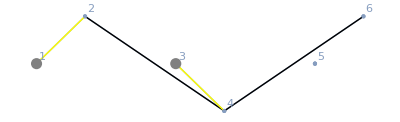

```mathematica
m=KLChainUnitCell[1,0.5,0.8,MeshCellLabel->{0->"Index"},"barColor"->Yellow]
```

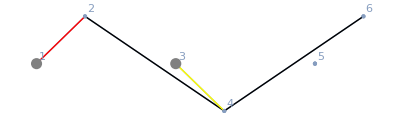

```mathematica
modifyMechanism[m,MeshCellStyle->{Line[{1,2}]->Red}]
```

```mathematica
displacementLength[m,{{2,4}}]
```

{1.23069}

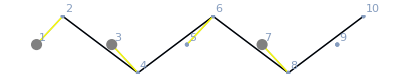

```mathematica
tesselateMechanism[m,{{2,0},{0,0}},{2,1}]
```

### examples

a 2D square linkage

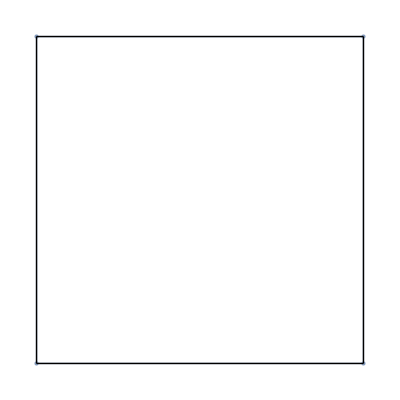

```mathematica
m=framework[{{0,0},{1,0},{1,1},{0,1}},{
rigidBar[{1,2}],rigidBar[{2,3}],rigidBar[{3,4}],rigidBar[{4,1}]
}
]
```

yoshimura cylindrical origami

```mathematica
?yoshimuraOrigami
```

```mathematica
yoshimuraOrigami[{3,4},1,1]
```

-Graphics3D-

## functions to manipulate mechanisms

### tools

#### componentPattern[]

```mathematica
componentPattern[x_Blank]:=If[Length[x]==0,{x,_,_},{x[[1]],_,_}]
componentPattern[r_Alternatives]:=componentPattern/@r
componentPattern[h_[r_Alternatives]]:=componentPattern[h/@r]
componentPattern[h_[n_List]]:=With[{numbers=Range[Length[n]]},{h,Alternatives@@Map[RotateRight[n,#]&,numbers],_}]
componentPattern[h_[n : Except[_Alternatives|_List]]]:={h,n,_}
```

#### renumberVerticesUnpacked[]

```mathematica
renumberVerticesUnpacked[{coordinates_?MatrixQ,mesh_List,components_List},reorderedVertices:{__Integer}]:=With[
{
	reorderingRules=Dispatch[Thread[reorderedVertices->Range[Length[reorderedVertices]]]]
},
	{
		coordinates[[reorderedVertices]],
		replaceUnpackedCells[mesh,reorderingRules],
		replaceUnpackedCells[components,reorderingRules]
	}
]/;Sort[reorderedVertices]==Range[Length[coordinates]]
```

#### deleteCellsUnpacked[]

```mathematica
deleteCellsUnpacked[{coordinates_?MatrixQ,mesh_List,components_List},deletedVertices:{__Integer}]:=
Module[
{
	remainingVertices=Complement[Range[Length[coordinates]],deletedVertices]
},
	{
		coordinates,
		Select[mesh,ContainsNone[Flatten[{#[[2]]}],deletedVertices]&],
		Select[components,ContainsNone[Flatten[{#[[2]]}],deletedVertices]&]
	}
]/;Max[deletedVertices]≤Length[coordinates]
```

#### deleteVerticesUnpacked[]

```mathematica
deleteVerticesUnpacked[{coordinates_,mesh_,components_},deletedVertices_]:=
With[
{
	remainingVertices=Complement[Range[Length[coordinates]],deletedVertices]
},
	({#[[ 1,Range[Length[remainingVertices]] ]],#[[2]],#[[3]]}&)[
		renumberVerticesUnpacked[deleteCellsUnpacked[{coordinates,mesh,components},deletedVertices],Join[remainingVertices,deletedVertices]]
	]
]

deleteVerticesUnpacked[vertices_]:=(deleteVerticesUnpacked[#,vertices]&)
```

#### listCells[]

```mathematica
listCells[{coordinates_,displayCells_,componentCells_},pattern_]:=
With[
{patt=componentPattern[pattern]},
{Cases[displayCells,pattern],Cases[componentCells,patt]}
]
```

```mathematica
mechanisms`Private`listCells[m["unpack"],_[{1,4}]]
```

{{},{{rigidBar,{4,1},{length→Automatic,stiffness→∞}}}}

#### gatherCells[]

```mathematica
gatherCells[{coordinates_,displayCells_,componentCells_}]:=
	GatherBy[Join[displayCells,componentCells],Sort[Flatten[{#[[2]]}]]&]
```

```mathematica
mechanisms`Private`gatherCells[m["unpack"]]
```

{{{Point,1,{}}},{{Point,2,{}}},{{Point,3,{}}},{{Point,4,{}}},{{Point,5,{}}},{{Point,6,{}}},{{Line,{4,6},{MeshCellStyle→GrayLevel[0]}},{rigidBar,{4,6},{length→Automatic,stiffness→∞}}},{{Line,{6,3},{MeshCellStyle→GrayLevel[0]}},{rigidBar,{6,3},{length→Automatic,stiffness→∞}}},{{Line,{3,4},{MeshCellStyle→GrayLevel[0]}},{rigidBar,{3,4},{length→Automatic,stiffness→∞}}},{{Line,{4,1},{MeshCellStyle→GrayLevel[0]}},{rigidBar,{4,1},{length→Automatic,stiffness→∞}}},{{Line,{1,6},{MeshCellStyle→GrayLevel[0]}},{rigidBar,{1,6},{length→Automatic,stiffness→∞}}},{{Line,{6,5},{MeshCellStyle→GrayLevel[0]}},{rigidBar,{6,5},{length→Automatic,stiffness→∞}}},{{Line,{5,3},{MeshCellStyle→GrayLevel[0]}},{rigidBar,{5,3},{length→Automatic,stiffness→∞}}},{{Line,{5,1},{MeshCellStyle→GrayLevel[0]}},{rigidBar,{5,1},{length→Automatic,stiffness→∞}}},{{Line,{1,2},{MeshCellStyle→GrayLevel[0]}},{rigidBar,{1,2},{length→Automatic,stiffness→∞}}},{{Line,{2,5},{MeshCellStyle→GrayLevel[0]}},{rigidBar,{2,5},{length→Automatic,stiffness→∞}}},{{Line,{2,3},{MeshCellStyle→GrayLevel[0]}},{rigidBar,{2,3},{length→Automatic,stiffness→∞}}},{{Polygon,{4,6,3},{}}},{{Polygon,{6,4,1},{}}},{{Polygon,{3,6,5},{}}},{{Polygon,{5,1,2},{}}},{{Polygon,{1,5,6},{}}},{{Polygon,{5,2,3},{}}}}

#### applyToCells[], removeCells[], removeData[]

```mathematica
mergeFunction[Line|Point|Polygon, added_, data_]:=Normal[ Merge[ Join[ data, FilterRules[Flatten[{added}],$meshRegionProperties] ], Last ] ]
mergeFunction[head_,added_,data_]:=Normal[Merge[ Join[ data, FilterRules[Flatten[{added}],Options[head]]], Last ] ]

applyToCells[{coordinates_,displayCells_,componentCells_},pattern_,do_]:=
Module[
{
x,
patt=componentPattern[pattern]
},With[
{
	replacementRule=(x:patt:>{ x[[1]], x[[2]], mergeFunction[ x[[1]], do, x[[3]] ] } )
},
	{coordinates,displayCells,componentCells}/.replacementRule
]]

applyToCells[pattern_,do_]:=(applyToCells[#,pattern,do]&)
```

```mathematica
removeCells[{coordinates_,displayCells_,componentCells_},pattern_]:=
With[{patt=componentPattern[pattern]},
	{coordinates,DeleteCases[displayCells,patt],DeleteCases[componentCells,patt]}
]
removeCells[pattern_]:=(removeCells[#,pattern]&)
```

```mathematica
removeData[{coordinates_,displayCells_,componentCells_},pattern_,data_]:=
Module[{x},With[{patt=componentPattern[pattern]},
With[{
rules=(x:patt:>{x[[1]],x[[2]],FilterRules[x[[3]],Except[data] ]}),
componentrules=(x:patt:>{x[[1]],x[[2]],mergeFunction[ x[[1]], Options[x[[1]]], FilterRules[x[[3]],Except[data] ] ]})
},
	{coordinates,displayCells/.rules,componentCells/.componentrules}
]]]

removeData[pattern_,data_]:=(removeData[#,pattern,data]&)
```

### connectivity functions and basic MeshRegion functions

#### listFaces[]

```mathematica
(* if here, the list of objects are not well-formed *)
listFaces::notv=="One or more vertices do not exist.";
```

```mathematica
listFaces[m:mechanismPattern]:=MeshCells[m["mesh"],2][[All,1]]

(*--from one or more vertices--*)
listFaces[m : mechanismPattern, vertex_Integer] /; MeshCellCount[m,0]>=vertex:=
With[{faces=MeshCells[m["mesh"],2][[All,1]]},
	orderFaces[rotateTo[#,vertex]& /@ Select[ faces, MemberQ[#,vertex]& ], vertex]
]

listFaces[m : mechanismPattern, vertices : {__Integer}]:= connectivity[m,"vertices"->"ordered faces"][[vertices]] /; Max[vertices]≤MeshCellCount[m,0]
listFaces[m : mechanismPattern, _Integer|{__Integer}]:="nothing" /; Message[listFaces::notv]

(*--from edges--*)
listFaces[mr : mechanismPattern, pairList_?(MatrixQ[#,IntegerQ]&)] /; Dimensions[pairList][[2]]==2:=
With[{faces=MeshCellIndex[mr["mesh"],Line/@pairList]},
	connectivity[mr["mesh"],"edges"->"ordered faces"][[ faces[[All,2]] ]]/;faces=!=$Failed
]

listFaces::notedge="One or more specified edges do not exist.";
listFaces[mr : mechanismPattern, _?MatrixQ]:="nothing"/;Message[listFaces::notedge]

listFaces::badlist="The input is not a list of vertices or list of edges.";
listFaces[mr : mechanismPattern, Except[_?MatrixQ]]:="nothing" /; Message[listFaces::badlist]
```

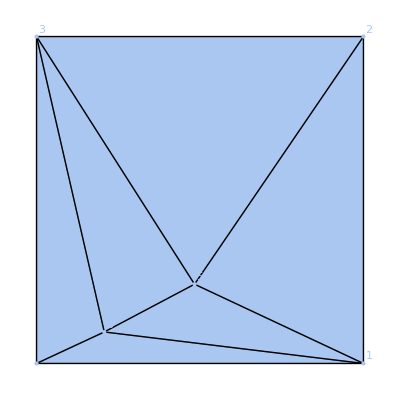

```mathematica
m=randomOrigami[2,MeshCellLabel->{0->"Index"}]
```

```mathematica
listFaces[m,{{2,4}}]
```

listFaces::notedge: One or more specified edges do not exist.

listFaces::badlist: The input is not a list of vertices or list of edges.

listFaces[-Graphics-,{{2,4}}]

```mathematica
listFaces[m,2]
```

{{2,3,5},{2,5,1}}

#### listEdges[]

```mathematica
listEdges[m : mechanismPattern]:=MeshCells[m["mesh"],1][[All,1]]

(*from vertex*)
listEdges[mr : mechanismPattern, v_Integer]:=With[{edges=MeshCells[mr["mesh"],1][[All,1]]},Cases[Join[edges,Reverse/@edges],{v,_}]]

listEdges[mr : mechanismPattern,{v__Integer}]:=With[{edges=MeshCells[mr["mesh"],1][[All,1]]},
	SortBy[GatherBy[Join[edges,Reverse/@edges],First],First@First@#&][[{v}]]
]
listEdges[v:{__Integer}]:=Partition[v,2,1,{1,1}]
(*from faces*)
listEdges[faces:{_?(VectorQ[#,IntegerQ]&)}]:=Partition[#,2,1,{1,1}]&/@faces
```

```mathematica
(* if here, the list of objects are not well-formed *)
listEdges::badlist="The heads of list are not all the same.";
listEdges[mr:_MeshRegion|_compiledMeshRegion,x_List]:="nothing" /; Message[listEdges::badlist]
listEdges[mr:_MeshRegion|_compiledMeshRegion,x_]:={}
```

#### listVertices[]

```mathematica
listVertices[mr : mechanismPattern]:=MeshCells[mr["mesh"],0][[All,1]]
listVertices[mr : mechanismPattern, vertex_Integer|Point[vertex_Integer]] /; 0<vertex≤MeshCellCount[mr,0]:=Last/@listFaces[mr,vertex]

listVertices::bounds="Vertex is not in the provided mechanism.";
listVertices[mr : mechanismPattern, _Integer|Point[_Integer]]:="nothing"/;Message[listVertices::bounds]
```

```mathematica
listVertices[randomOrigami[2],5]
```

{4,1,6,3}

#### interiorEdges[], interiorVertices[],boundaryEdges[],boundaryVertices[]

```mathematica
interiorEdges[m : mechanismPattern]:=interiorEdges[m["mesh"]]
interiorVertices[m : mechanismPattern]:=interiorVertices[m["mesh"]]
boundaryEdges[m : mechanismPattern]:=boundaryEdges[m["mesh"]]
boundaryVertices[m : mechanismPattern]:=boundaryVertices[m["mesh"]]
boundaryFaces[m : mechanismPattern]:=boundaryFaces[m["mesh"]]
```

#### connectivity[]

```mathematica
connectivity[m : mechanismPattern, Rule[s1_String,s2_String] ]:=connectivity[m["mesh"],s1->s2]
```

#### MeshCellCount[],MeshCoordinates[],Rationalize[],Precision[]

```mathematica
MeshCellCount[m_framework,r___]^:=MeshCellCount[m["mesh"],r]
MeshCellCount[m_origami,r___]^:=MeshCellCount[m["mesh"],r]
```

```mathematica
MeshCoordinates[m_framework]^:=MeshCoordinates[m["mesh"]]
MeshCoordinates[m_origami]^:=MeshCoordinates[m["mesh"]]
```

```mathematica
Rationalize[m_framework,dx___]^:=m["positions"->Rationalize[m["positions"],dx]]
Rationalize[m_origami,dx___]^:=m["positions"->Rationalize[m["positions"],dx]]
```

```mathematica
Precision[m_framework]^:=Precision[m["positions"]]
Precision[m_origami]^:=Precision[m["positions"]]
```

### Map[]

```mathematica
Map[f_, m_framework]^:=With[
{newPositions=f /@ m["positions"]},
	m[ "positions"->newPositions, "mesh"-> deformMesh[m["mesh"],newPositions] ]
]
```

```mathematica
Map[f_, m_origami]^:=With[
{newPositions=f /@ m["positions"]},
	m[ "positions" -> newPositions, "mesh" -> deformMesh[ m["mesh"], If[ displayDimension[m]==2, to2D[newPositions], newPositions ] ] ]
]
```

### deleteVertices[],deleteDanglingVertices[]

```mathematica
deleteVertices[m:mechanismPattern,{}]:=m
deleteVertices[m:mechanismPattern,verticesToDelete:{__Integer}]:=With[
{
	deletableVertices=DeleteDuplicates[verticesToDelete], (*not sure if this is necessary*)
	unpackedMechanism=m["unpack"]
},
	Head[m][deleteVerticesUnpacked[unpackedMechanism,deletableVertices]]
] /; Max[verticesToDelete]≤MeshCellCount[m,0]

deleteVertices::range="One or more vertices are out of range.";
deleteVertices::nov="Second argument should be a list of vertex indices to delete.";
deleteVertices[m:mechanismPattern,{__Integer}]:="nothing"/;Message[deleteVertices::range]
deleteVertices[m:mechanismPattern,_]:="nothing"/;Message[deleteVertices::nov]
```

```mathematica
deleteDanglingVertices[m_origami]:=deleteDanglingVertices[m,"faces"]
deleteDanglingVertices[m_framework]:=deleteDanglingVertices[m,"edges"]
deleteDanglingVertices[m:mechanismPattern,type:"faces"|"edges"]:=deleteDanglingVertices[m,type]

deleteDanglingVertices[m:mechanismPattern,"faces"]:=With[
{vertexSelector=Transpose[{Range[MeshCellCount[m,0]],Length/@connectivity[m["mesh"],"vertices"->"faces"]}]},
	deleteVertices[m,Select[vertexSelector,#[[2]]<1&][[All,1]]]
]

deleteDanglingVertices[m:mechanismPattern,"edges"]:=With[
{vertexSelector=Complement[Range[MeshCellCount[m,0]],connectivity[m["mesh"],"vertices"->"edges"][[All,1,1]]]},
	deleteVertices[m,vertexSelector]
]

deleteDanglingVertices::typ="Second argument should be either \"faces\" or \"edges\" to whether dangling vertices are indicated by a lack of faces or lack of edges.";
deleteDanglingVertices[m:mechanismPattern,_String]:="nothing"/;Message[deleteDanglingVertices::typ]
```

### deleteCells[],deleteData[]

```mathematica
deleteCells[m : mechanismPattern, cellPattern_]:=Head[m][removeCells[m["unpack"],cellPattern]]
deleteCells[cellPattern_][m : mechanismPattern]:=Head[m][removeCells[m["unpack"],cellPattern]]
```

```mathematica
deleteData[m : mechanismPattern, cellPattern_]:=Head[m][removeData[m["unpack"],cellPattern]]
deleteData[cellPattern_][m : mechanismPattern]:=Head[m][removeData[m["unpack"],cellPattern]]
```

### addCells[]

```mathematica
addCells[m : mechanismPattern, newCells_]:=
With[
{
newMechanism=Head[m][mechanismPositions[m],Flatten[{newCells}]]["unpack"],
unpackedMech=m["unpack"]
},
	Head[m][{newMechanism[[1]],Join[unpackedMech[[2]],newMechanism[[2]]],Join[unpackedMech[[3]],newMechanism[[3]]]}]
]
```

### mechanismComponents[]

```mathematica
mechanismComponents[m : mechanismPattern]:=mechanismComponents[m,_]
mechanismComponents[m : mechanismPattern, pattern_]:=repackMechanismCells[Cases[unpackCells[m["components"]],componentPattern[pattern]]]

mechanismComponents[m : mechanismPattern, Rule[cellPattern_,data:{__Rule}|_Rule]]:=Head[m][applyToCells[m["unpack"],cellPattern,data]]
mechanismComponents[m : mechanismPattern, r:__Rule]:=Head[m][Fold[applyToCells[#1,#2[[1]],#2[[2]]]&,m["unpack"],{r}]]
```

### modifyMechanism[]

```mathematica
modifyMechanism["Methods"]={MeshCellLabel,MeshCellStyle,"add","addComponent","style","label","shape"};
```

```mathematica
modifyMechanism::unknown="Unknown method `1`.";
```

#### MeshCellStyle,MeshCellLabel

```mathematica
modifyMechanism[m : mechanismPattern, MeshCellStyle->s_, r___]:=
	modifyMechanism[ m["mesh"->MeshRegion[m["mesh"], MeshCellStyle->s]], r]
```

```mathematica
modifyMechanism[m:mechanismPattern,MeshCellLabel->s_,r___]:=
	modifyMechanism[m["mesh"->MeshRegion[m["mesh"],MeshCellLabel->s]],r]
```

#### "addComponent"

```mathematica
modifyMechanism[m:mechanismPattern,"addComponent"->addList_,r___]:=modifyMechanism[
	m["components"->repackMechanismCells[Join[unpackCells[m["components"]],unpackCells[Flatten[{addList}]]]]]
,r]
```

#### "add"

```mathematica
modifyMechanism[m:mechanismPattern,"add"->addList_,r___]:=Module[{
unpackedm=m["unpack"],
newmech=Head[m][mechanismPositions[m],Flatten[{addList}]]["unpack"]
},
	modifyMechanism[
		Head[m][{unpackedm[[1]],Join[unpackedm[[2]],newmech[[2]]],Join[unpackedm[[3]],newmech[[3]]]}]
,r]]
```

#### “style”

```mathematica
modifyMechanism::stylecell="Cell `1` should be either Point, Line, or Polygon to change style.";

toMeshStyle[style : {Line,_,_}|{Point,_,_}|{Polygon,_,_}]:=style
toMeshStyle[{rigidBar,indices_,styles_}]:={Line,indices,styles}
toMeshStyle[{joint,indices_,styles_}]:={Point,indices,styles}
toMeshStyle[style : {_,_,_}]:=(Message[modifyMechanism::stylecell,style[[1]]]; style)

styleListParse[Rule[x_ , style_]]:={toMeshStyle[componentPattern[x]], style}
styleListParse[_]:={"donotmatchthis",Null}
```

```mathematica
modifyMechanism[m : mechanismPattern, "style"->styleList_, r___]:=
modifyMechanism[
	Module[{type, indices, stylespec},With[
	{
		data = {type : #[[1,1]],indices : #[[1,2]], stylespec_} :> {
			type, 
			indices, 
			Join[
				FilterRules[stylespec , {MeshCellLabel,MeshCellShapeFunction}], (*filter out MeshCellStyle*)
				{MeshCellStyle->#[[2]]}
			]
			}& /@ styleListParse /@ styleList,
		unpackedMechanism=m["unpack"]
	},
	Head[m][ { unpackedMechanism[[1]], unpackedMechanism[[2]] /. data, unpackedMechanism[[3]] } ]
	]]
,r]
```

#### “label”

```mathematica
modifyMechanism[m : mechanismPattern, "label"->styleList_, r___]:=
modifyMechanism[
	Module[{x,y,z},With[{
		data={x:#[[1,1]],y:#[[1,2]],z_}:>{x,y,Join[FilterRules[z,{MeshCellStyle,MeshCellShapeFunction}],{MeshCellLabel->#[[2]]}]}& /@ styleListParse /@ styleList
	},
	Head[m][m["unpack"]/.data]
	]]
,r]
```

#### “shape”

```mathematica
modifyMechanism[m:mechanismPattern,"shape"->styleList_,r___]:=modifyMechanism[
	Module[{x,y,z},With[{
		data={x:#[[1,1]],y:#[[1,2]],z_}:>{x,y,Join[FilterRules[z,{MeshCellStyle,MeshCellLabel}],{MeshCellShapeFunction->#[[2]]}]}&/@styleListParse/@styleList
	},
	Head[m][m["unpack"]/.data]
	]]
,r]
```

#### terminate the recursion

```mathematica
modifyMechanism[m:mechanismPattern,Rule[method_,data_],r___]:=(Message[modifyMechanism::unknown,method]; modifyMechanism[m,r])
```

```mathematica
modifyMechanism[m:mechanismPattern]:=m
```

### displaceVertices[]

```mathematica
displaceVertices::dim="Displacements are not the same dimension as the mechanism embedding dimension.";
displaceVertices::rules="Displacements should be in the form of vertex -> displacement.";

displacementRuleQ[Rule[_Integer,_?VectorQ]]:=True
displacementRuleQ[_]:=False
```

```mathematica
displacementRules[numVertices_, r: _?displacementRuleQ|{__?displacementRuleQ}]:=
With[{displacements=Range[numVertices]/.r},
	With[{dim=Max[Length/@displacements]},
		Replace[displacements,Rule[_Integer,ConstantArray[0,dim]],1]
]]
displacementRules[_,_]:="nothing"/;Message[displaceVertices::rules]
```

```mathematica
displaceVerticesInternal[m_,r_]:=
Module[{displacements=displacementRules[MeshCellCount[m,0],r]},
	m["positions"]+displacements /; MatrixQ[displacements]&&Dimensions[displacements][[2]]==embeddingDimension[m]
]
displaceVerticesInternal[_,r:_?displacementRuleQ|{__?displacementRuleQ}]:="nothing"/;Message[displaceVertices::dim]
```

```mathematica
displaceVertices[m : mechanismPattern, r_]:=
Module[{res=displaceVerticesInternal[m, r]},
	res /; Head[res]=!=displaceVerticesInternal
]
```

```mathematica
displaceVertices[randomOrigami[2],1->{0,0,0}]
```

{{0.707107,-0.707107,0},{0.707107,0.707107,0},{-0.707107,0.707107,0},{-0.707107,-0.707107,0},{0.696896,0.494029,0},{0.310793,-0.176844,0}}

### mechanismPositions[]

```mathematica
mechanismPositions[m_?mechanismQ]:=m["positions"]
```

```mathematica
mechanismPositions[Rule[m_framework,newPositions_?(MatrixQ[#,NumericQ]&)]]:=
	m[
		"positions"->newPositions,
		"mesh"->deformMesh[m["mesh"],newPositions]
	] /; Dimensions[newPositions]=={MeshCellCount[m,0],embeddingDimension[m]}

mechanismPositions::baddimmatch="Positions do not correspond to number of vertices or dimension of mechanism.";
mechanismPositions[Rule[m_framework,newPositions_?(MatrixQ[#,NumericQ]&)]]:="nothing"/;Message[mechanismPositions::baddimmatch]
```

```mathematica
mechanismPositions[Rule[m_origami,newPositions_?(MatrixQ[#,NumericQ]&)]]:=
	m[
		"positions"->to3D[newPositions],
		"mesh"->deformMesh[m["mesh"],newPositions]
	]/;Length[newPositions]==MeshCellCount[m,0]&&Not[displayDimension[m]==3&&Last[Dimensions[newPositions]]==2]

mechanismPositions::notmat="Positions are not numeric and of the same dimension.";				
mechanismPositions::badmatch="Positions do not correspond to number of vertices of origami.";
mechanismPositions::baddim="Origami structure is already manifestly in 3D. Positions must also be in 3D.";
mechanismPositions[Rule[m_origami,newPositions_?MatrixQ]]:="nothing"/;Which[
	Not[MatrixQ[newPositions,NumericQ]],
		Message[mechanismPositions::notmat]; False,
	Length[newPositions]!=MeshCellCount[m,0],
		Message[mechanismPositions::badmatch]; False,
	displayDimension[m]==3&&Last[Dimensions[newPositions]]==2,
		Message[mechanismPositions::baddim]; False,
	True,False
]
```

```mathematica
mechanismPositionsInternal[m_origami,r_]:=Module[
{displacements=displacementRules[MeshCellCount[m,0],r]},
	Which[
		Dimensions[displacements][[2]]==3,
			mechanismPositions[m->(m["positions"]+displacements)],
		Dimensions[displacements][[2]]==2 && displayDimension[m]==2,
			m[
				"positions"->(m["positions"]+to3D[displacements]),
				"mesh"->deformMesh[m["mesh"],MeshCoordinates[m["mesh"]]+displacements]
			],
		Dimensions[displacements][[2]]==2&&displayDimension[m]==3,
			Message[mechanismPositions::baddim]; $Failed,
		True,
			$Failed
	]
]
mechanismPositionsInternal[m_framework,r_]:=Module[{newPositions=Check[displaceVertices[m,r],$Failed]},
	If[newPositions===$Failed,$Failed,mechanismPositions[m->newPositions]]
]

mechanismPositions[Rule[m_?mechanismQ,r_]]:=Module[{res=mechanismPositionsInternal[m,r]}, res /; res=!=$Failed]
```

```mathematica
mechanismPositions::badpos="Second argument must be a list of positions or a list of displacement rules for vertices.";
mechanismPositions[Rule[m_?mechanismQ,_]]:="nothing"/;Message[mechanismPositions::badpos]
```

### joinMechanism[]

```mathematica
Options[joinMechanism]={"overlapPrecision"->10^(-12)};
```

```mathematica
joinMechanism[m__?mechanismQ, opt : OptionsPattern[]]:=Module[
{
startingIndices=Most@Accumulate[Join[{1},MeshCellCount[#,0]&/@{m}]],
unpackedMechanisms
},
	Head[{m}[[1]]]@Join[MapThread[Join,MapThread[#1["unpack",#2]&,{{m},startingIndices}]],opt]
]/;SameQ@@(Head/@{m})
```

```mathematica
joinMechanism::notsame="Cannot join different mechanism types together.";
joinMechanism[m__]:="nothing"/;Message[joinMechanism::notsame]
```

### tesselateMechanism[]

```mathematica
Options[tesselateMechanism]={"overlapPrecision"->10^(-6)};
```

```mathematica
tesselateMechanism[m:mechanismPattern,basis_?(VectorQ[#,NumericQ]&),n1_Integer,opt:OptionsPattern[]]:=
	tesselateMechanism[m,{basis,ConstantArray[0,Length[basis]]},{n1,1},opt]&&n1>0
```

```mathematica
tesselateMechanism[m:mechanismPattern,basis_?(MatrixQ[#,NumericQ]&),{n1_Integer,n2_Integer},opt:OptionsPattern[]]:=
Module[
{
	translatedMechanisms,
	newIndices=Flatten[Array[1+MeshCellCount[m,0] (#2-1+n2 (#1-1))&,{n1,n2}]],
	newCoordinates=Flatten[Array[ConstantArray[#1 basis[[1]]+#2 basis[[2]],MeshCellCount[m,0]]&,{n1,n2}],1]+ConstantArray[m["positions"],n1 n2]
},
	Head[m][Join[MapThread[Join,MapThread[#1["unpack",#2]&,{m["positions"->#]&/@newCoordinates,newIndices}]]],opt]

]/;Length[basis]==2&&n1>0&&n2>0
```

### embeddingDimension[],displayDimension[]

```mathematica
embeddingDimension[m : mechanismPattern]:=Last[Dimensions[m["positions"]]]
embeddingDimension[Rule[m : mechanismPattern, dim : 2|3]]:=m["positions"->PadRight[m["positions"],{Length[m["positions"]],dim}]]

embeddingDimension::dim="Dimension `1` must a positive integer that is either 2 or 3.";
embeddingDimension[Rule[m : mechanismPattern, dim_]]:="nothing" /; Message[embeddingDimension::dim,dim]
```

```mathematica
displayDimension[m : mechanismPattern]:=RegionEmbeddingDimension[m["mesh"]]
displayDimension[Rule[m : mechanismPattern, dim : 2|3]]:=m["mesh"->deformMesh[m["mesh"],PadRight[MeshCoordinates[m["mesh"]],{MeshCellCount[m,0],dim}]]]

displayDimension::dim="Dimension `1` must be a positive integer that is either 2 or 3.";
displayDimension[Rule[m : mechanismPattern, dim_]]:="nothing" /; Message[displayDimension::dim,dim]
```

### saveToFOLD[],loadFromFOLD[]

#### saveToFOLD[]

Save the mechanism using the .fold specification (https://github.com/edemaine/fold/blob/master/doc/spec.md)

```mathematica
incrementVertices[d_List]:=#+1&/@d
decrementVertices[d_List]:=#-1&/@d
```

```mathematica
saveToFOLD[m:mechanismPositions,filename_String]:=Export[{
	"file_spec"->1.1,
	"file_creator"->"Mathematica",
	"file_classes"->{"singleModel"},
	"frame_classes"->{"creasePattern"},
	"frame_attributes"->{
		Switch[displayDimension[m],2,"2D",3,"3D",_,Nothing],
		If[surfaceQ[m["mesh"]],"manifold",Nothing],
		If[orientedQ[m["mesh"]],"orientable","nonOrientable"]
	},
	"frame_unit"->"unit",
	"vertices_coords"->m["positions"],
	"edges_vertices"->decrementVertices/@listEdges[m],
	"faces_vertices"->decrementVertices/@listFaces[m]
},"JSON"]
```

#### loadFromFOLD[]

```mathematica
Options[loadFromFOLD]=Join[{"face"->(face[#]&)},Options[origami]];
```

```mathematica
loadFromFOLD[filename_String,opt:OptionsPattern[]]:=Module[
{
	inputData=Import[filename,"JSON"],
	coords,edges,faces
},
	If[inputData===$Failed,
		$Failed,

		coords="vertices_coords"/.inputData;
		edges="edges_vertices"/.inputData;
		faces="faces_vertices"/.inputData;
		origami[coords,Join[OptionValue["face"]/@incrementVertices/@faces],FilterRules[{opt},Options[origami]]]
	]
]
```

## mechanism geometry

### error messages

```mathematica
displacementVector::edges="Second argument should be a properly formed list of edges {{v1,v2},...}";
displacementVector::bounds="Some vertices are out-of-bounds.";

displacementLength::edges="Second argument should be a properly formed list of edges {{v1,v2},...}";
displacementLength::bounds="Some vertices are out-of-bounds.";

displacementLengthSquared::edges="Second argument should be a properly formed list of edges {{v1,v2},...}";
displacementLengthSquared::bounds="Some vertices are out-of-bounds.";

turningAngle::triples="Second argument should be a properly formed list of triples {{v1,v2,v3},...}";
turningAngle::bounds="Some vertices are out-of-bounds.";

normalVector::faces="Second argument should be a properly formed list of faces {{v1,v2,v3,...},...}";
normalVector::bounds="Some vertices are out-of-bounds.";
normalVector::norm="Option \"normalization\" must be True or False.";

planarAngle::bounds="Some vertices are out-of-bounds.";
planarAngle::triples="Last argument is not a list of three points defining angles.";
```

```mathematica
faceVolume::dim="Dimension of positions is not 3.";
faceVolume::base="Dimension of base point is not 3.";
faceVolume::faces="Faces must be a list of triangles.";
faceVolume::bounds="Some vertices are out of bounds.";

faceArea::faces="Faces must be a list of triangles.";
faceArea::bounds="Some vertices are out of bounds.";
```

```mathematica
foldAngle::bounds="Some vertices are out of bounds.";
foldAngle::edges="Last argument should be a list of edges of the form {{v1,v2},...}.";
foldAngle::quadruples="Last argument should be lists of 4 vertices defining a fold.";
foldAngle::pos="Positions do not match those of MeshRegion.";
foldAngle::dim="MeshRegion positions should be in 3D.";
foldAngle::notfold="One of the folds does not exist.";
```

```mathematica
gaussianCurvature::vertices="Last argument is not a list of vertices.";
gaussianCurvature::bounds="Some vertices are out of bounds.";
gaussianCurvature::dim="Dimension must be 3.";
gaussianCurvature::arg="The arguments do not match.";
gaussianCurvature::triples="The last argument must be a list of planar angles surrounding each vertex.";
```

### argument checkers

```mathematica
edgeListQ[e_]:=And[
	MatrixQ[e,IntegerQ],
	Last[Dimensions[e]]==2
	]
```

```mathematica
angleListQ[e_]:=And[
	MatrixQ[e,IntegerQ],
	Last[Dimensions[e]]==3
	]
```

```mathematica
ClearAll[faceListQ];
faceListQ[faces:{__?(VectorQ[#,IntegerQ]&)}]:=AllTrue[Length/@faces,#>2&]
faceListQ[_]:=False
```

```mathematica
triangulatedFaceListQ[faces_]:=And[
	MatrixQ[faces,IntegerQ],
	Last[Dimensions[faces]]==3
]
```

```mathematica
boundsQ[arg1_?MatrixQ,e_]:=Max[e]≤Length[arg1]
boundsQ[m_?mechanismQ,e_]:=Max[e]≤MeshCellCount[m["mesh"],0]
boundsQ[_,_]:=False
```

### displacementVector[]

```mathematica
displacementVector[positions_?vertexCoordinatesQ,edgelist_]:=displacementVectorInternal[positions,edgelist] /; 
	Which[
		Not[boundsQ[positions,edgelist]],
			Message[displacementVector::bounds]; False,
		Not[edgeListQ[edgelist]],
			Message[displacementVector::edges]; False,
		True,True
	]
displacementVector[m : mechanismPattern, edgelist_]:=displacementVectorInternal[m["positions"],edgelist] /; Which[
	Not[boundsQ[m,edgelist]],
		Message[displacementVector::bounds]; False,
	Not[edgeListQ[edgelist]],
		Message[displacementVector::edges]; False,
	True,True
]
displacementVector[m : mechanismPattern, positions_, edgelist_]:=displacementVectorInternal[positions,edgelist]
```

```mathematica
displacementVectorInternal[positions_,edgeList_]:=
With[{flippedEdgeList=Transpose[edgeList]},
	positions[[flippedEdgeList[[2]]]]-positions[[flippedEdgeList[[1]]]]
]
```

```mathematica
m=framework[{{0,0},{1,0},{1,1},{0,1}},{
rigidBar[{1,2}],rigidBar[{2,3}],rigidBar[{3,4}],rigidBar[{4,1}],
Polygon[{1,2,3,4}]
}
];
displacementVector[m,{{1,2}}]
```

{{1,0}}

### displacementLength[]

```mathematica
displacementLength[positions_?vertexCoordinatesQ,edgelist_]:=displacementLengthInternal[positions,edgelist] /; Which[
	Not[edgeListQ[edgelist]],
		Message[displacementLength::edges]; False,
	Not[boundsQ[positions,edgelist]],
		Message[displacementLength::bounds]; False,
	True, True
]

displacementLength[m : mechanismPattern ,edgelist_]:=displacementLengthInternal[m["positions"],edgelist] /; Which[
	Not[edgeListQ[edgelist]],
		Message[displacementLength::edges]; False,
	Not[boundsQ[m,edgelist]],
		Message[displacementLength::bounds]; False,
	True, True
]
displacementLength[m : mechanismPattern , positions_, edgelist_]:=displacementLength[positions,edgelist]
```

```mathematica
displacementLengthInternal[positions_?(MatrixQ[#,MachineRealQ]&), edgelist_]:=displacementLengthCompiled[Length[positions[[1]]]][positions,ToPackedArray[edgelist]]
displacementLengthInternal[positions_,edgelist_]:=displacementLengthAnalytic[positions,ToPackedArray[edgelist]]
```

#### internal code

```mathematica
displacementLengthCompiled[d_Integer]:=displacementLengthCompiled[d]=
Compile[
{{pos,_Real,2},{edges,_Integer,2}},
	Module[{i,j},
		Table[
			With[{
			index1=Compile`GetElement[edges,i,1],
			index2=Compile`GetElement[edges,i,2]
			},
			Sqrt[Sum[(Compile`GetElement[pos,index1,j]-Compile`GetElement[pos,index2,j])^2,{j,1,d}]]
			],
		{i,1,Length[edges]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
displacementLengthAnalytic[positions_,edgeList_]:=
	expandExpression[Sqrt[(# . #&)/@displacementVectorInternal[positions,edgeList]]]
```

### displacementLengthSquared[]

```mathematica
displacementLengthSquared[positions_?vertexCoordinatesQ,edgelist_]:=displacementLengthSquaredInternal[positions,edgelist] /; Which[
	Not[edgeListQ[edgelist]],
		Message[displacementLength::edges]; False,
	Not[boundsQ[positions,edgelist]],
		Message[displacementLength::bounds]; False,
	True, True
]

displacementLengthSquared[m : mechanismPattern ,edgelist_]:=displacementLengthSquaredInternal[m["positions"],edgelist] /; Which[
	Not[edgeListQ[edgelist]],
		Message[displacementLength::edges]; False,
	Not[boundsQ[m,edgelist]],
		Message[displacementLength::bounds]; False,
	True, True
]
displacementLengthSquared[m : mechanismPattern , positions_, edgelist_]:=displacementLengthSquared[positions,edgelist]
```

```mathematica
displacementLengthSquaredInternal[positions_?(MatrixQ[#,MachineRealQ]&), edgelist_]:=displacementLengthSquaredCompiled[Length[positions[[1]]]][positions,ToPackedArray[edgelist]]
displacementLengthSquaredInternal[positions_,edgelist_]:=displacementLengthSquaredAnalytic[positions,ToPackedArray[edgelist]]
```

#### internal

```mathematica
displacementLengthSquaredCompiled[d_Integer]:=displacementLengthSquaredCompiled[d]=
Compile[
{{pos,_Real,2},{edges,_Integer,2}},
	Module[{i,j},
		Table[
			With[{
			index1=Compile`GetElement[edges,i,1],
			index2=Compile`GetElement[edges,i,2]
			},
			Sum[(Compile`GetElement[pos,index1,j]-Compile`GetElement[pos,index2,j])^2,{j,1,d}]
			],
		{i,1,Length[edges]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
displacementLengthSquaredAnalytic[positions_,edgeList_]:=
	expandExpression[Map[# . # &,displacementVectorInternal[positions,edgeList]]]
```

### turningAngle[]

```mathematica
turningAngle[positions_?vertexCoordinatesQ,triplelist_]:=turningAngleInternal[positions,triplelist] /; Which[
	Not[angleListQ[triplelist]],
		Message[turningAngle::triples]; False,
	Not[boundsQ[positions,triplelist]],
		Message[turningAngle::bounds]; False,
	True,True
]
turningAngle[m : mechanismPattern,triplelist_]:=turningAngleInternal[m["positions"],triplelist] /; Which[
	Not[angleListQ[triplelist]],
		Message[turningAngle::triples]; False,
	Not[boundsQ[m,triplelist]],
		Message[turningAngle::bounds]; False,
	True,True
]
turningAngle[m : mechanismPattern, positions_,triplelist_]:=turningAngle[positions,triplelist]
```

```mathematica
turningAngleInternal[positions_?(MatrixQ[#,MachineRealQ]&), tripleList_]:=turningAngleCompiled[Length[positions[[1]]]][m["positions"],ToPackedArray[tripleList]]
turningAngleInternal[positions_,tripleList_]:=turningAngleAnalytic[Length[positions[[1]]],positions,ToPackedArray[tripleList]]
```

#### numeric

```mathematica
turningAngleCompiled[3]:=turningAngleCompiled[3]=
Compile[
{{pos,_Real,2},{triplets,_Integer,2}},
	Module[{i},
		With[{
			p1x=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1],
			p1y=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2],
			p1z=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3],
			p2x=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
			p2y=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
			p2z=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3]
		},
			ArcCos[(p1x p2x+p1y p2y+p1z p2z)/(Sqrt[p1x^2+p1y^2+p1z^2] Sqrt[p2x^2+p2y^2+p2z^2])]
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]

turningAngleCompiled[2]:=turningAngleCompiled[2]=
Compile[
{{pos,_Real,2},{triplets,_Integer,2}},
	Module[{i},
		Table[With[{
			p1x=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1],
			p1y=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2],
			p2x=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
			p2y=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2]
		},
			ArcTan[p1x p2x + p1y p2y,p1x p2y - p2x p1y]
		],{i,1,Length[triplets]}]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
{w1 v1+w2 v2,Cross[{w1,w2,0} ,{v1,v2,0}][[3]]}/(Sqrt[w1^2+w2^2] Sqrt[v1^2+v2^2])
```

{(v1 w1+v2 w2)/(√(v1^2+v2^2) √(w1^2+w2^2)),(v2 w1-v1 w2)/(√(v1^2+v2^2) √(w1^2+w2^2))}

#### analytic

```mathematica
(*
this funny construction here works better during expansions because of the branch cuts of ArcCos[]

The problem arises in Series[ArcCos[1-xx^2],{xx,0,2}] which requires the choice of a branch. This last part
hasn't been solved but at least the answer comes out faster. The rest of the branch cut issues
are handled automatically in expandExpression[], which does what it can to make imaginary components zero.

There should be a better way to handle this but this seems to work in most cases.
*)
turningAngleAnalytic[3,data_,tripleList_]:=
With[
{
	cosvectorAngle3D=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]},
			(x xx+y yy+z zz)/(Sqrt[x^2+y^2+z^2] Sqrt[xx^2+yy^2+zz^2])
		]
	]
},
	(expandExpression@With[{pts=data[[#]]},ArcCos[expandExpression@cosvectorAngle3D[pts[[2]]-pts[[1]],pts[[3]]-pts[[2]]]]])&/@tripleList
]
```

```mathematica
{w1 v1+w2 v2,Cross[{w1,w2,0} ,{v1,v2,0}][[3]]}/(Sqrt[w1^2+w2^2] Sqrt[v1^2+v2^2])
```

{(v1 w1+v2 w2)/(√(v1^2+v2^2) √(w1^2+w2^2)),(v2 w1-v1 w2)/(√(v1^2+v2^2) √(w1^2+w2^2))}

```mathematica
turningAngleAnalytic[2,data_,tripleList_]:=
With[
{
	vectorAngle2D=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],xx=p2[[1]],yy=p2[[2]]},
			ArcTan[x xx + y yy,x yy - xx y]	
		]
	]
},
	(expandExpression@With[{pts=data[[#]]},vectorAngle2D[pts[[2]]-pts[[1]],pts[[3]]-pts[[2]]]])&/@tripleList
]
```

```mathematica
?VectorAngle
```

```mathematica
VectorAngle[{x,y},{xx,yy}]
```

ArcCos[(x Conjugate[xx]+y Conjugate[yy])/(√(Abs[x]^2+Abs[y]^2) √(Abs[xx]^2+Abs[yy]^2))]

```mathematica
mechanisms`Private`turningAngleAnalytic[2,{{2,0},{1,0},{1,-1}},{{1,2,3}}]
```

{π/2}

```mathematica
mechanisms`Private`turningAngleCompiled[2][{{2.,0.},{1.,0.},{1.,-1.}},{{1,2,3}}]
```

{1.5708}

### normalVector[]

```mathematica
Options[normalVector]={"normalize"->True};

normalVector[pos_?vertexCoordinatesQ, faces_,OptionsPattern[]]:=normalVectorInternal[pos,faces,OptionValue["normalize"]] /; Which[
	Not[BooleanQ[OptionValue["normalize"]]],
		Message[normalVector::norm]; False,
	Not[faceListQ[faces]],
		Message[normalVector::faces]; False,
	Not[boundsQ[pos,faces]],
		Message[normalVector::bounds]; False,
	True, True
]
normalVector[m : mechanismPattern, faces_,OptionsPattern[]]:=normalVectorInternal[m["positions"],faces,OptionValue["normalize"]] /; Which[
	Not[BooleanQ[OptionValue["normalize"]]],
		Message[normalVector::norm]; False,
	Not[faceListQ[faces]],
		Message[normalVector::faces]; False,
	Not[boundsQ[m,faces]],
		Message[normalVector::bounds]; False,
	True, True
]
normalVector[m : mechanismPattern, pos_?vertexCoordinatesQ,faces_,opt : OptionsPattern[]]:=normalVector[pos,faces,opt]
```

```mathematica
normalVectorInternal[pos_?(MatrixQ[#,MachineRealQ]&),faces_,normalize_ : True]:=normalVectorCompiled[normalize,Length[pos[[1]]]][pos,ToPackedArray[faces]]
normalVectorInternal[pos_,faces_,normalize_ : True]:=normalVectorAnalytic[normalize,Length[pos[[1]]],pos,faces]
```

#### numerical

```mathematica
normalVectorCompiled[True,3]:=normalVectorCompiled[True,3]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				z=Compile`GetElement[pos,Compile`GetElement[faces,i,3],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				zz=Compile`GetElement[pos,Compile`GetElement[faces,i,1],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3]
			},
			{
				(-yy z+y zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
				(xx z-x zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
				(-xx y+x yy)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]
			}
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
normalVectorCompiled[False,3]:=normalVectorCompiled[False,3]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				z=Compile`GetElement[pos,Compile`GetElement[faces,i,3],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				zz=Compile`GetElement[pos,Compile`GetElement[faces,i,1],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3]
			},
			{
				(-yy z+y zz),
				(xx z-x zz),
				(-xx y+x yy)
			}
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
normalVectorCompiled[True,2]:=normalVectorCompiled[True,2]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2]
			},
				Sign[-xx y+x yy]
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
normalVectorCompiled[False,2]:=normalVectorCompiled[False,2]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2]
			},
				-xx y+x yy
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

#### analytic

```mathematica
normalVectorAnalytic[True (* normalized *),3, positions_, triples_]:=
With[
{
	data=positions,
	normalVector3D=Function[
		{p1,p2},
		With[
			{
			x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]
			},
			{
			(-yy z+y zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
			(xx z-x zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
			(-xx y+x yy)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]
			}
		]
	]
},
	With[{p=data[[#]]},expandExpression@normalVector3D[p[[3]]-p[[2]],p[[1]]-p[[2]]]]&/@triples
] 

normalVectorAnalytic[False (* normalized *),3, positions_, triples_]:=
With[
{
	data=positions,
	unnormalVector3D=Function[
		{p1,p2},
		With[
			{
			x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]
			},
			{
			-yy z+y zz,
			xx z-x zz,
			-xx y+x yy
			}
		]
	]
},
	With[{p=data[[#]]},expandExpression@unnormalVector3D[p[[3]]-p[[2]],p[[1]]-p[[2]]]]&/@triples
]
```

### planarAngle[]

```mathematica
planarAngle[pos_?vertexCoordinatesQ,triples_]:=planarAngleInternal[pos,triples] /; Which[
	Not[angleListQ[triples]],
		Message[planarAngle::triples]; False,
	Not[boundsQ[pos,triples]],
		Message[planarAngle::bounds]; False,
	True, True
]
planarAngle[m : mechanismPattern,triples_]:=planarAngleInternal[m["positions"],triples] /; Which[
	Not[angleListQ[triples]],
		Message[planarAngle::triples]; False,
	Not[boundsQ[m,triples]],
		Message[planarAngle::bounds]; False,
	True, True
]
planarAngle[m : mechanismPattern,pos_?vertexCoordinatesQ,triples_]:=planarAngle[pos,triples]
```

```mathematica
planarAngleInternal[pos_?(MatrixQ[#,MachineRealQ]&),triples_]:=planarAngleCompiled[Length[pos[[1]]]][pos,triples]
planarAngleInternal[pos_,triples_]:=planarAngleAnalytic[Length[pos[[1]]],pos,triples]
```

#### numeric

```mathematica
planarAngleCompiled[3]:=planarAngleCompiled[3]=
Compile[
{{pos,_Real,2},{triplets,_Integer,2}},Module[{i},
	Table[
		With[{
		x=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		y=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
		z=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3],
		xx=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		yy=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
		zz=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3]
		},
		ArcTan[x xx+y yy+z zz,Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]]
		],
	{i,1,Length[triplets]}
	]],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
planarAngleCompiled[2]:=planarAngleCompiled[2]=Compile[
{{pos,_Real,2},{triplets,_Real,2}},Module[{i},
	Table[With[{
		x=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		y=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
		xx=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		yy=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2]
	},
			ArcTan[x xx+y yy,(xx y-x yy)^2]
	],{i,1,Length[triplets]}
	]
],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

#### analytic

```mathematica
planarAngleAnalytic[3,positions_,tripleList_]:=
With[
{
	data=positions,
	angleFunc=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]},
			ArcTan[x xx+y yy+z zz,Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]]
		]
	]
},
	With[{pts=data[[#]]},expandExpression@angleFunc[pts[[1]]-pts[[2]],pts[[3]]-pts[[2]]]]&/@tripleList
]
```

```mathematica
planarAngleAnalytic[2,positions_,tripleList_]:=
With[
{
	data=positions,
	angleFunc=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],xx=p2[[1]],yy=p2[[2]]},
			ArcTan[x xx+y yy,(xx y-x yy)^2]
		]
	]
},
	With[{pts=data[[#]]},expandExpression@angleFunc[pts[[1]]-pts[[2]],pts[[3]]-pts[[2]]]]&/@tripleList
]
```

### foldAngle[]

```mathematica
(*list all the folds in all orientations as quickly as possible*)
possibleFoldsQ[m : mechanismPattern, indices_]:=
Module[{folds, edges=listEdges[m]},
	folds=Flatten[Select[Thread[{Transpose[{edges, Reverse[edges,{2}]}],connectivity[m,"edges"->"faces"]}],Length[Last[#]]==2&][[All,1]],1];
	ContainsOnly[indices,folds]
]
```

```mathematica
foldAngle[m : mechanismPattern,positions_,edgelist_]:=foldAngleInternal[m,positions,edgelist] /; Which[
	Not[edgeListQ[edgelist]], Message[foldAngle::edges]; False,
	Not[boundsQ[positions,edgelist]], Message[foldAngle::bounds]; False,
	embeddingDimension[m]≠3, Message[foldAngle::dim]; False,
	Dimensions[positions] ≠ {MeshCellCount[m,0],3}, Message[foldAngle::pos]; False,
	Not @ possibleFoldsQ[m, edgelist], Message[foldAngle::notfold]; False,
	True,True
]
foldAngle[m : mechanismPattern, edgelist_]:=foldAngleInternal[m,m["positions"],edgelist] /; Which[
	Not[edgeListQ[edgelist]], Message[foldAngle::edges]; False,
	Not[boundsQ[m,edgelist]], Message[foldAngle::bounds]; False,
	embeddingDimension[m]≠3, Message[foldAngle::dim]; False,
	Not @ possibleFoldsQ[m, edgelist],Message[foldAngle::notfold]; False,
	True,True
]
```

```mathematica
foldAngleInternal[m : mechanismPattern, positions_?(MatrixQ[#,MachineRealQ]&), edgelist_]:=foldAngleCompiled[][positions,listQuadruples[m["mesh"],edgelist]]
foldAngleInternal[m : mechanismPattern, positions_, edgelist_]:=foldAngleAnalytic[positions,listQuadruples[m["mesh"],edgelist]]
```

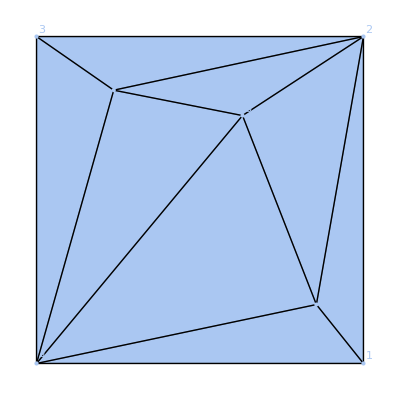

```mathematica
m
```

```mathematica
MeshCellIndex[m["mesh"],{Line[{6,5}],Line[{3,1}],Line[{7,6}]}]
```

$Failed

#### listQuadruples[]

```mathematica
(*does no argument checking*)
listQuadruples[m_MeshRegion,edgelist_]:=
With[
{
faces=connectivity[m,"edges"->"ordered faces"][[ MeshCellIndex[m,Line/@edgelist][[All,2]] ]]
},
	ToPackedArray[If[Length[#]==2,{#[[2,1]],#[[2,2]],#[[1,2]],Last@#[[2]]},{#[[1,1]],#[[1,2]],0,0}]&/@faces]
]
```

```mathematica
MeshCellIndex[m["mesh"],Line/@{{5,6}}][[All,2]]
```

{14}

```mathematica
connectivity[m,"edges"->"ordered faces"][[6]]
```

Part::partw: Part 6 of {{{1,2,3,4}},{{2,3,4,1}},{{3,4,1,2}},{{4,1,2,3}}} does not exist.

{{{1,2,3,4}},{{2,3,4,1}},{{3,4,1,2}},{{4,1,2,3}}}⟦6⟧

```mathematica
mechanisms`Private`listQuadruples[m["mesh"],{{5,6}}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::pkspec1: The expression Symbol[] cannot be used as a part specification.

Part::partw: Part 2 of {{{1,2,3,4}},{{2,3,4,1}},{{3,4,1,2}},{{4,1,2,3}}} does not exist.

Part::partw: Part 1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {Symbol[]⟦1,1⟧,Symbol[]⟦1,2⟧,0,0} cannot be used as a part specification.

{{1,2,3,4},{{{1,2,3,4}},{{2,3,4,1}},{{3,4,1,2}},{{4,1,2,3}}}⟦1,2⟧,0,0}⟦{Symbol[]⟦1,1⟧,Symbol[]⟦1,2⟧,0,0}⟧

#### numerical/compiled

```mathematica
foldAngleCompiled[]:=foldAngleCompiled[]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
Table[
	If[Compile`GetElement[faces,i,3]==0,
	0,
	With[
		{
		p1x=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1],
		p1y=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2],
		p1z=Compile`GetElement[pos,Compile`GetElement[faces,i,1],3],
		p2x=Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
		p2y=Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
		p2z=Compile`GetElement[pos,Compile`GetElement[faces,i,2],3],
		p3x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1],
		p3y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2],
		p3z=Compile`GetElement[pos,Compile`GetElement[faces,i,3],3],
		p4x=Compile`GetElement[pos,Compile`GetElement[faces,i,4],1],
		p4y=Compile`GetElement[pos,Compile`GetElement[faces,i,4],2],
		p4z=Compile`GetElement[pos,Compile`GetElement[faces,i,4],3]
		},
		ArcTan[(p1y (p2x-p3x)+p2y p3x-p2x p3y+p1x (-p2y+p3y)) (-p2y p4x+p1y (-p2x+p4x)+p1x (p2y-p4y)+p2x p4y)+(p1z (p2x-p3x)+p2z p3x-p2x p3z+p1x (-p2z+p3z)) (-p2z p4x+p1z (-p2x+p4x)+p1x (p2z-p4z)+p2x p4z)+(p1z (p2y-p3y)+p2z p3y-p2y p3z+p1y (-p2z+p3z)) (-p2z p4y+p1z (-p2y+p4y)+p1y (p2z-p4z)+p2y p4z),Sqrt[(p1x-p2x)^2+(p1y-p2y)^2+(p1z-p2z)^2] (-p1x p2z p3y+p1x p2y p3z+p2z p3y p4x-p2y p3z p4x+p1x p2z p4y-p2z p3x p4y-p1x p3z p4y+p2x p3z p4y+p1z (p2x p3y-p3y p4x+p2y (-p3x+p4x)-p2x p4y+p3x p4y)+(-p1x p2y+p2y p3x+p1x p3y-p2x p3y) p4z+p1y (p2z p3x-p2x p3z-p2z p4x+p3z p4x+p2x p4z-p3x p4z))]
	]],
	{i,1,Length[faces]}
],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

#### analytic

```mathematica
foldAngleAnalytic[positions_,quadrupleList_]:=
	With[
	{
	p1x=positions[[#[[1]],1]],p1y=positions[[#[[1]],2]],p1z=positions[[#[[1]],3]],
	p2x=positions[[#[[2]],1]],p2y=positions[[#[[2]],2]],p2z=positions[[#[[2]],3]],
	p3x=positions[[#[[3]],1]],p3y=positions[[#[[3]],2]],p3z=positions[[#[[3]],3]],
	p4x=positions[[#[[4]],1]],p4y=positions[[#[[4]],2]],p4z=positions[[#[[4]],3]]
	},
	expandExpression@ArcTan[(p1y (p2x-p3x)+p2y p3x-p2x p3y+p1x (-p2y+p3y)) (-p2y p4x+p1y (-p2x+p4x)+p1x (p2y-p4y)+p2x p4y)+(p1z (p2x-p3x)+p2z p3x-p2x p3z+p1x (-p2z+p3z)) (-p2z p4x+p1z (-p2x+p4x)+p1x (p2z-p4z)+p2x p4z)+(p1z (p2y-p3y)+p2z p3y-p2y p3z+p1y (-p2z+p3z)) (-p2z p4y+p1z (-p2y+p4y)+p1y (p2z-p4z)+p2y p4z),Sqrt[(p1x-p2x)^2+(p1y-p2y)^2+(p1z-p2z)^2] (-p1x p2z p3y+p1x p2y p3z+p2z p3y p4x-p2y p3z p4x+p1x p2z p4y-p2z p3x p4y-p1x p3z p4y+p2x p3z p4y+p1z (p2x p3y-p3y p4x+p2y (-p3x+p4x)-p2x p4y+p3x p4y)+(-p1x p2y+p2y p3x+p1x p3y-p2x p3y) p4z+p1y (p2z p3x-p2x p3z-p2z p4x+p3z p4x+p2x p4z-p3x p4z))]
	]&/@quadrupleList
```

### gaussianCurvature[]

```mathematica
gaussianCurvature[m : mechanismPattern, vertexlist_]:= gaussianCurvatureInternal[m,m["positions"],vertexlist] /; Which[
	Not[VectorQ[vertexlist,IntegerQ]], Message[gaussianCurvature::vertices]; False,
	Max[vertexlist]>MeshCellCount[m,0] || Min[vertexlist]<1, Message[gaussianCurvature::bounds]; False,
	embeddingDimension[m]<2, False,
	True, True
]

gaussianCurvature[m : mechanismPattern, pos_, vertexlist_]:=gaussianCurvatureInternal[m,pos,vertexlist] /; Which[
	Not[VectorQ[vertexlist,IntegerQ]], Message[gaussianCurvature::vertices]; False,
	Max[vertexlist]>MeshCellCount[m,0] || Min[vertexlist]<1, Message[gaussianCurvature::bounds]; False,
	Dimensions[pos]≠{MeshCellCount[m,0],embeddingDimension[m]},Message[gaussianCurvature::dim]; False,
	embeddingDimension[m]<2, False,
	True, True
]
```

```mathematica
gaussianCurvatureInternal[m : mechanismPattern, pos_,vertexlist_]:=ConstantArray[0,Length[vertexlist]] /; embeddingDimension[m]==2
gaussianCurvatureInternal[m : mechanismPattern, pos_?(MatrixQ[#,MachineRealQ]&),vertexlist_]:=
		gaussianCurvatureCompiled[][pos,
			ToPackedArray[PadRight[connectivity[m["mesh"],"vertices"->"ordered faces"]][[vertexlist]][[All,All,1;;3]]]
	]
gaussianCurvatureInternal[m : mechanismPattern, pos_,vertexlist_]:=
	gaussianCurvatureAnalytic[
		pos,
		ToPackedArray[
			Map[RotateRight,connectivity[m["mesh"],"vertices"->"ordered faces"][[vertexlist]],{2}][[All,All,1;;3]]
		]
	]
```

```mathematica
(*gaussianCurvature[pos_?(MatrixQ[#,MachineRealQ]&),triples:{__?(MatrixQ[#,IntegerQ]&)}]:=(
	gaussianCurvatureCompiled[][pos,ToPackedArray[PadRight[triples]]]
)/;And[
	Max[triples]<=Length[pos], (*vertices are all in bounds*)
	AllTrue[triples,Last[Dimensions[#]]==3&],
	Last[Dimensions[pos]]==3
	]

gaussianCurvature[pos_?MatrixQ,triples:{__?(MatrixQ[#,IntegerQ]&)}]:=(
	(2 Pi-Total[planarAngle[pos,#]])&/@triples
)/;And[
	Max[triples]<=Length[pos],
	AllTrue[triples,Last[Dimensions[#]]==3&],
	Last[Dimensions[pos]]==3
	]

gaussianCurvature[pos_?MatrixQ,triples_]:="nothing"/;Which[
	Head[triples]=!=List,
		Message[gaussianCurvature::triples]; False,
	Not[AllTrue[triples,Last[Dimensions[#]]==3&]],
		Message[gaussianCurvature::triples]; False,	
	Max[triples]>Length[pos],
		Message[gaussianCurvature::bounds]; False,
	Last[Dimensions[pos]]!=3,
		Message[gaussianCurvature::dim]; False,
	True,
		Message[gaussianCurvature::arg]; False
]*)
```

```mathematica
(*gaussianCurvature[m_?mechanismQ,vertexList_?(VectorQ[#,IntegerQ]&)]:=gaussianCurvature[m,mechanismPositions[m],vertexList]*)
```

```mathematica
(*(* MeshRegion, machine precision calculation*)
gaussianCurvature[m_?mechanismQ,pos_?(MatrixQ[#,MachineRealQ]&),vertexList_?(VectorQ[#,IntegerQ]&)]:=
	gaussianCurvatureCompiled[][
		pos,
		ToPackedArray[
			PadRight[connectivity[m["mesh"],"vertices"->"ordered faces"]][[vertexList]][[All,All,1;;3]]
		]
	]/; And[
		Max[vertexList]<=MeshCellCount[m["mesh"],0],
		Last[Dimensions[pos]]==3
		]*)
```

```mathematica
(*(*MeshRegion, analytic*)
gaussianCurvature[m_?mechanismQ,pos_?MatrixQ,vertexList_?(VectorQ[#,IntegerQ]&)]:=(
	gaussianCurvature[
		pos,
		ToPackedArray[
			Map[RotateRight,connectivity[m["mesh"],"vertices"->"ordered faces"][[vertexList]],{2}][[All,All,1;;3]]
		]
	]
)/; And[
	Max[vertexList]<=Length[pos],
	Last[Dimensions[pos]]==3
	]*)
```

```mathematica
(*gaussianCurvature[m_?mechanismQ,pos_,vertices_]:="nothing"/;Which[
	Not[VectorQ[vertices,IntegerQ]],
		Message[gaussianCurvature::vertices]; False,	
	Max[vertices]>Length[pos],
		Message[gaussianCurvature::bounds]; False,
	Last[Dimensions[pos]]!=3,
		Message[gaussianCurvature::dim]; False,
	embeddingDimension[m]!=3,
		Message[gaussianCurvature::dim]; False,
	True,
		Message[gaussianCurvature::arg]; False
]

gaussianCurvature[m_?mechanismQ,vertices_]:="nothing"/;Which[
	Not[VectorQ[vertices,IntegerQ]],
		Message[gaussianCurvature::vertices]; False,	
	Max[vertices]>MeshCellCount[m["mesh"],0],
		Message[gaussianCurvature::bounds]; False,
	embeddingDimension[m]!=3,
		Message[gaussianCurvature::dim]; False,
	True,
		Message[gaussianCurvature::arg]; False
]*)
```

#### numerical

```mathematica
gaussianCurvatureCompiled[]:=gaussianCurvatureCompiled[]=
Compile[{{pos,_Real,2},{triplets,_Integer,3}},
	Module[{i,j},Table[2 Pi-Sum[
		If[Compile`GetElement[triplets,j,i,1]==0,
			0,
			With[{
			x=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],1],
			y=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],2],
			z=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,3],3]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],3],
			xx=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,2],1]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],1],
			yy=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,2],2]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],2],
			zz=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,2],3]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],3]
			},
			ArcTan[x xx+y yy+z zz,Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]]
			]
		],
		{i,1,Length[Compile`GetElement[triplets,j]]}(* Sum *)
	],{j,1,Length[triplets]}] (* Table *)
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

#### analytical

```mathematica
gaussianCurvatureAnalytic[pos_,{triples__?(MatrixQ[#,IntegerQ]&)}]:=
	(expandExpression@(2 Pi-Total[planarAngle[pos,#]]))&/@{triples}
```

### examples

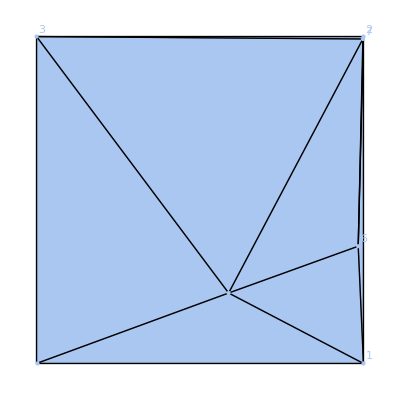

```mathematica
m=randomOrigami[3,MeshCellLabel->{0->"Index"}]
```

```mathematica
displacementLengthSquared[m,{{5,7}}]
displacementLength[m,{{4,7}}]
```

{1.5448}

{1.99082}

```mathematica
turningAngle[m,{{5,7,6}}]
planarAngle[m,{{5,7,6}}]

turningAngle[m,{{5,7,6}}]+planarAngle[m,{{5,7,6}}]
```

{2.67796}

{0.463635}

{3.14159}

```mathematica
normalVector[m,{{1,7,5}}]
```

{{0.,0.,1.}}

```mathematica
foldAngle[m,mechanismPositions[m],{{5,6}}]
foldAngle[m,{{5,6}}]
foldAngle[m,{{3,1}}]
```

{0.}

{0.}

foldAngle::notfold: One of the folds does not exist.

foldAngle[-Graphics-,{{3,1}}]

```mathematica
gaussianCurvature[m,{6}]
```

{0.}

### alignMechanism[]

```mathematica
Options[alignMechanism]=Join[Options[FindGeometricTransform],{"vertices"->All}];

alignMechanism[m1_?mechanismQ,m2_?mechanismQ,opt:OptionsPattern[]]:=
	mechanismPositions[m2->#[[2]]]&[alignMechanism[m1["positions"],m2["positions"]]]

alignMechanism[p1_?(MatrixQ[#,NumericQ]&),m2_?mechanismQ,opt:OptionsPattern[]]:=
	{#[[1]],mechanismPositions[m2->#[[2]]]}&[alignMechanism[p1,m2["positions"],opt][[2]]]

alignMechanism[p1_?(MatrixQ[#,NumericQ]&),p2_?(MatrixQ[#,NumericQ]&),opt:OptionsPattern[]]:=
Module[{points1,points2,alignment,transform},
	{points1,points2}=If[OptionValue["vertices"]===All,
		{p1,p2},
		{p1[[Flatten@OptionValue["vertices"]]],p2[[Flatten@OptionValue["vertices"]]]}
	];
	{alignment,transform}=FindGeometricTransform[points1,points2,Join[FilterRules[{opt},Options[FindGeometricTransform]],{TransformationClass->"Rigid"}]];
	{alignment,transform[p2]}
]
```

### congruentQ[]

```mathematica
congruentQ[tolerance:_?NumericQ:10^(-1)][pos1_?(MatrixQ[#,NumericQ]&),pos2_?(MatrixQ[#,NumericQ]&)]:=congruentQ[pos1,pos2,tolerance]

congruentQ[m1_?mechanismQ,m2_?mechanismQ,tolerance:_?NumericQ:10^(-1)]:=congruentQ[m1["positions"],m2["positions"],tolerance]
congruentQ[pos1_?(MatrixQ[#,NumericQ]&),pos2_?(MatrixQ[#,NumericQ]&),tolerance:_?NumericQ:10^(-1)]:=With[
{
(* a naive way to pick three equivalent points on each set of positions *)
points1=pos1,points2=pos2
},
	FindGeometricTransform[points1,points2,TransformationClass->"Rigid",Method->"Linear"][[1]]<tolerance
]
```

## rigidity and energy

### isometry tools

#### selectConstraints[]

This selects a set of components that should be treated as rigid constraints (for example, because of infinite stiffness).

```mathematica
selectConstraints[m_,positions_,components_List]:=selectConstraints[m,positions,#]&/@Flatten[components]
```

```mathematica
selectConstraints[m_,positions_,rigidBar[indices_,data_]]:=
With[{constraints=componentData["stiffness",m,positions,rigidBar[indices,data]]},
	rigidBar[Pick[indices,constraints,Infinity],Pick[data,constraints,Infinity]]
]

selectConstraints[m_,positions_,fold[indices_,data_]]:=
With[{constraints=componentData["torsionalStiffness",m,positions,fold[indices,data]]},
	fold[Pick[indices,constraints,Infinity],Pick[data,constraints,Infinity]]
]

selectConstraints[m_,positions_,joint[indices_,data_]]:=
With[{constraints=componentData["stiffness",m,positions,joint[indices,data]]},
	joint[Pick[indices,constraints,Infinity],Pick[data,constraints,Infinity]]
]

selectConstraints[m_,positions_,other_]:={}
```

#### linearMotions[]

A function to compute the linear motions of a mechanism given a rigidity matrix.

```mathematica
Options[linearMotions]=Options[NullSpace];
linearMotions[m_,rigidityMatrix_,opt:OptionsPattern[]]:=Module[
{dim=embeddingDimension[m],lin=NullSpace[rigidityMatrix,opt]},
	If[Length[lin]>0,
		Partition[Orthogonalize[lin],{1,dim}][[All,All,1]],
		{}
	]
]
```

### energy tools

#### analyticEnergyQ[]

Determine if an energy function is properly formed by seeing if it evaluates to a real number.

```mathematica
analyticEnergyQ[Automatic,positions_]:=True
analyticEnergyQ[energyExpression_,positions_]:=With[
{number=N[energyExpression/.Dispatch[dataRules[vertexPosition,positions]]]},
	Im[Chop[number]]==0&&NumericQ[number]&&Chop[Im[number]]==0
]
```

#### pinnedJoints[]

Return a list of vertexPositions that have been pinned to particular places in space. We can use this to avoid minimizing or operating on something that can’t move anyway.

```mathematica
pinnedJoints[m_,initialPositions_]:=
Module[
{
	constrainedVertices=selectConstraints[m,initialPositions,Cases[m["components"],_joint]],
	components,positions
},
	If[Length[constrainedVertices]>0,
		components=componentData["components",m,initialPositions,constrainedVertices[[1]]];
		positions=componentData["position",m,initialPositions,constrainedVertices[[1]]];
	
		Flatten @ MapThread[Thread[vertexPosition[#1,#2]->#3[[#4]]] &,{
			constrainedVertices[[1,1]],
			components,
			positions,
			components/.{"x"->1,"y"->2,"z"->3}
			}
		],
		
		{}
	]
]
```

```mathematica
m=randomOrigami[3];
```

```mathematica
m=modifyMechanism[randomOrigami[2],"add"->{Property[joint[1],{"components"->{"y","z"}}]}];
```

```mathematica
RepeatedTiming[mechanisms`Private`pinnedJoints[m,m["positions"]]]
```

{0.000051,{vertexPosition[1,y]→-0.707107,vertexPosition[1,z]→0}}

#### dynamicVariables[]

Returns a list of variables and their initial values in the form {{variable 1, value 1},{variable 2,value 2},...}

```mathematica
dynamicVariables[m_, pinnedVertices_,initialPositions_]:=
Cases[
	Transpose[{Flatten @ vertexPosition[m],Flatten @ initialPositions}]/.pinnedVertices,
	{_vertexPosition,_}
]
```

#### evaluateEnergy[]

```mathematica
evaluateEnergy[m : mechanismPattern, positions_?MatrixQ, energy: Except[_compiledMechanismEnergy]]:=
	energy /. Dispatch[dataRules[vertexPosition,positions]]
evaluateEnergy[m : mechanismPattern, positions_?VectorQ, energy: Except[_compiledMechanismEnergy]]:=
	energy /. Dispatch[Thread[Flatten[vertexPosition[m]]->positions]]
evaluateEnergy[m : mechanismPattern, positions_?MatrixQ, energy_?compiledMechanismEnergyQ]:=
	energy[[2]][Flatten[positions],energy["data"]]
evaluateEnergy[m : mechanismPattern, positions_?VectorQ, energy_?compiledMechanismEnergyQ]:=
	energy[[2]][positions,energy["data"]]
```

### constraintEquations[]

```mathematica
Options[constraintEquations]:={"output"->vertexDisplacement}
```

```mathematica
constraintEquations[m : mechanismPattern, positions_ : Automatic, order : 1|2|Infinity, OptionsPattern[]]:=
With[
{
actualPositions=If[ positions===Automatic, m["positions"], positions ],
output=OptionValue["output"]
},
	constraintEquationsInternal[m,actualPositions,order,m["components"],output] /; Which[
		Not[vertexCoordinatesQ[m,actualPositions]],
			Message[constraintEquations::pos]; False,
		Not[MatchQ[output,vertexPosition | vertexDisplacement]],
			Message[constraintEquations::output]; False,
		True, True
		]
]

constraintEquations::pos="Positions do not correspond to mechanism vertices.";
constraintEquations::output="Option \"output\" must be either vertexDisplacement or vertexPosition.";
```

```mathematica
(*legacy version in case we call it this way*)
constraintEquationsInternal[m_,actualPositions_,order_,components_]:=
	Flatten[componentConstraints[m,actualPositions,selectConstraints[m,actualPositions,#],order,vertexDisplacement]&/@components]


constraintEquationsInternal[m_,actualPositions_,order_,components_,output_]:=
	Flatten[componentConstraints[m,actualPositions,selectConstraints[m,actualPositions,#],order,output]&/@components]
```

#### rigidBar

```mathematica
componentConstraints[m_, positions_, rigidBar[indices_,data_], 1, vertexDisplacement]:=
	2 MapThread[#1 . #2&,{displacementVector[positions,indices],displacementVector[vertexDisplacement[m],indices]}]

componentConstraints[m_, positions_, rigidBar[indices_,data_], 1, vertexPosition]:=
	2 MapThread[#1 . #2&,{displacementVector[positions,indices],displacementVector[vertexPosition[m]-positions,indices]}]

componentConstraints[m_, positions_, rigidBar[indices_,data_], 2|Infinity, vertexDisplacement]:=
	displacementLengthSquared[positions+vertexDisplacement[m],indices]-componentData["length",m,positions,rigidBar[indices,data]]^2

componentConstraints[m_,positions_,rigidBar[indices_,data_],2|Infinity,vertexPosition]:=
	displacementLengthSquared[vertexPosition[m],indices]-componentData["length",m,positions,rigidBar[indices,data]]^2
```

#### fold

```mathematica
componentConstraints[m_,positions_,fold[indices_,data_],order:1|2,vertexDisplacement]:=Module[{eps},
	foldAngle[m,positions+infinitesimal[eps,order] vertexDisplacement[m],indices]/.infinitesimal[eps,order]->1
]/;Length[indices]>0
componentConstraints[m_,positions_,fold[indices_,data_],Infinity,vertexDisplacement]:=
	foldAngle[m,positions+vertexDisplacement[m],indices]/;Length[indices]>0
	
componentConstraints[m_,positions_,fold[indices_,data_],order:1|2,vertexPosition]:=Module[{eps},
	foldAngle[m,positions+infinitesimal[eps,order] (vertexPosition[m]-positions),indices]/.infinitesimal[eps,order]->1
]/;Length[indices]>0
componentConstraints[m_,positions_,fold[indices_,data_],Infinity,vertexPosition]:=
	foldAngle[m,vertexPosition[m],indices]/;Length[indices]>0

componentConstraints[m_,positions_,fold[{},{}],_,_]:={}
```

#### joint

```mathematica
componentConstraints[m_,positions_,joint[indices_,data_],1|2|Infinity,output_]:=
With[{
componentsToUse=Replace[
	componentData["components",m,positions,joint[indices,data]],
	All->All[embeddingDimension[m]],
	1]
},
	Flatten[MapThread[output[#1,#2]&,{indices,componentsToUse}]]
]
```

#### angleJoint

```mathematica
componentConstraints[m_,positions_,angleJoint[indices_,data_],order:1|2,vertexDisplacement]:=Module[{eps},
	turningAngle[positions+infinitesimal[eps,order] vertexDisplacement[m],indices]/.infinitesimal[eps,order]->1
]/;Length[indices]>0
componentConstraints[m_,positions_,angleJoint[indices_,data_],Infinity,vertexDisplacement]:=
	turningAngle[positions+vertexDisplacement[m],indices]/;Length[indices]>0

componentConstraints[m_,positions_,angleJoint[indices_,data_],order:1|2,vertexPosition]:=Module[{eps},
	turningAngle[positions+infinitesimal[eps,order] (vertexPosition[m]-positions),indices]/.infinitesimal[eps,order]->1
]/;Length[indices]>0
componentConstraints[m_,positions_,angleJoint[indices_,data_],Infinity,vertexPosition]:=
	turningAngle[vertexPosition[m],indices]/;Length[indices]>0

componentConstraints[m_,positions_,angleJoint[{},{}],_,_]:={}
```

#### other

```mathematica
componentConstraints[m_,positions_,_,_,_]:={}
```

#### documentation

```mathematica
?constraintEquations
```

Basic usage: Get a list of equations, valid to first order, second order, or infinite order for constraints.

```mathematica
constraintEquations[(m=randomOrigami[2]),1]
```

{2 (0.187302 (-vertexDisplacement[4,x]+vertexDisplacement[6,x])+1.07346 (-vertexDisplacement[4,y]+vertexDisplacement[6,y])),2 (-0.187302 (vertexDisplacement[3,x]-vertexDisplacement[6,x])+0.340756 (vertexDisplacement[3,y]-vertexDisplacement[6,y])),2 (0.-1.41421 (-vertexDisplacement[3,y]+vertexDisplacement[4,y])),2 (1.39602 (-vertexDisplacement[4,x]+vertexDisplacement[5,x])+0.631385 (-vertexDisplacement[4,y]+vertexDisplacement[5,y])),2 (-1.20872 (-vertexDisplacement[5,x]+vertexDisplacement[6,x])+0.442072 (-vertexDisplacement[5,y]+vertexDisplacement[6,y])),2 (1.22691 (vertexDisplacement[2,x]-vertexDisplacement[6,x])+0.340756 (vertexDisplacement[2,y]-vertexDisplacement[6,y])),2 (0.-1.41421 (-vertexDisplacement[2,x]+vertexDisplacement[3,x])),2 (0.0181902 (vertexDisplacement[1,x]-vertexDisplacement[5,x])-0.631385 (vertexDisplacement[1,y]-vertexDisplacement[5,y])),2 (0.+1.41421 (-vertexDisplacement[1,y]+vertexDisplacement[2,y])),2 (-0.0181902 (-vertexDisplacement[2,x]+vertexDisplacement[5,x])-0.782828 (-vertexDisplacement[2,y]+vertexDisplacement[5,y])),2 (0.+1.41421 (vertexDisplacement[1,x]-vertexDisplacement[4,x]))}

You can use the optional second argument to insert your own positions.

```mathematica
constraintEquations[m,Rationalize[mechanismPositions[m],1/100],1]
```

{2 (25/133 (-vertexDisplacement[4,x]+vertexDisplacement[6,x])+61/56 (-vertexDisplacement[4,y]+vertexDisplacement[6,y])),2 (-25/133 (vertexDisplacement[3,x]-vertexDisplacement[6,x])+19/56 (vertexDisplacement[3,y]-vertexDisplacement[6,y])),-20/7 (-vertexDisplacement[3,y]+vertexDisplacement[4,y]),2 (128/91 (-vertexDisplacement[4,x]+vertexDisplacement[5,x])+58/91 (-vertexDisplacement[4,y]+vertexDisplacement[5,y])),2 (-301/247 (-vertexDisplacement[5,x]+vertexDisplacement[6,x])+47/104 (-vertexDisplacement[5,y]+vertexDisplacement[6,y])),2 (165/133 (vertexDisplacement[2,x]-vertexDisplacement[6,x])+19/56 (vertexDisplacement[2,y]-vertexDisplacement[6,y])),-20/7 (-vertexDisplacement[2,x]+vertexDisplacement[3,x]),2 (2/91 (vertexDisplacement[1,x]-vertexDisplacement[5,x])-58/91 (vertexDisplacement[1,y]-vertexDisplacement[5,y])),20/7 (-vertexDisplacement[1,y]+vertexDisplacement[2,y]),2 (-2/91 (-vertexDisplacement[2,x]+vertexDisplacement[5,x])-72/91 (-vertexDisplacement[2,y]+vertexDisplacement[5,y])),20/7 (vertexDisplacement[1,x]-vertexDisplacement[4,x])}

At infinite order, the equations are still written in terms of the displacements rather than positions.

```mathematica
constraintEquations[m,Rationalize[mechanismPositions[m],1/100],Infinity]
```

{-(√1383281)/1064+(25/133-vertexDisplacement[4,x]+vertexDisplacement[6,x])^2+(61/56-vertexDisplacement[4,y]+vertexDisplacement[6,y])^2+(-vertexDisplacement[4,z]+vertexDisplacement[6,z])^2,-(√170321)/1064+(-25/133+vertexDisplacement[3,x]-vertexDisplacement[6,x])^2+(19/56+vertexDisplacement[3,y]-vertexDisplacement[6,y])^2+(vertexDisplacement[3,z]-vertexDisplacement[6,z])^2,-10/7+(-vertexDisplacement[3,x]+vertexDisplacement[4,x])^2+(-10/7-vertexDisplacement[3,y]+vertexDisplacement[4,y])^2+(-vertexDisplacement[3,z]+vertexDisplacement[4,z])^2,-(2 √4937)/91+(128/91-vertexDisplacement[4,x]+vertexDisplacement[5,x])^2+(58/91-vertexDisplacement[4,y]+vertexDisplacement[5,y])^2+(-vertexDisplacement[4,z]+vertexDisplacement[5,z])^2,-(√6595913)/1976+(-301/247-vertexDisplacement[5,x]+vertexDisplacement[6,x])^2+(47/104-vertexDisplacement[5,y]+vertexDisplacement[6,y])^2+(-vertexDisplacement[5,z]+vertexDisplacement[6,z])^2,-(√1872721)/1064+(165/133+vertexDisplacement[2,x]-vertexDisplacement[6,x])^2+(19/56+vertexDisplacement[2,y]-vertexDisplacement[6,y])^2+(vertexDisplacement[2,z]-vertexDisplacement[6,z])^2,-10/7+(-10/7-vertexDisplacement[2,x]+vertexDisplacement[3,x])^2+(-vertexDisplacement[2,y]+vertexDisplacement[3,y])^2+(-vertexDisplacement[2,z]+vertexDisplacement[3,z])^2,-(2 √842)/91+(2/91+vertexDisplacement[1,x]-vertexDisplacement[5,x])^2+(-58/91+vertexDisplacement[1,y]-vertexDisplacement[5,y])^2+(vertexDisplacement[1,z]-vertexDisplacement[5,z])^2,-10/7+(-vertexDisplacement[1,x]+vertexDisplacement[2,x])^2+(10/7-vertexDisplacement[1,y]+vertexDisplacement[2,y])^2+(-vertexDisplacement[1,z]+vertexDisplacement[2,z])^2,-(2 √1297)/91+(-2/91-vertexDisplacement[2,x]+vertexDisplacement[5,x])^2+(-72/91-vertexDisplacement[2,y]+vertexDisplacement[5,y])^2+(-vertexDisplacement[2,z]+vertexDisplacement[5,z])^2,-10/7+(10/7+vertexDisplacement[1,x]-vertexDisplacement[4,x])^2+(vertexDisplacement[1,y]-vertexDisplacement[4,y])^2+(vertexDisplacement[1,z]-vertexDisplacement[4,z])^2}

You can get the output in terms of vertex positions using option “output”.

```mathematica
Options[constraintEquations]
```

{output→vertexDisplacement}

```mathematica
FullSimplify[constraintEquations[m,Infinity,"output"->vertexPosition]]
```

{-1.08968+(vertexPosition[4,x]-vertexPosition[6,x])^2+(vertexPosition[4,y]-vertexPosition[6,y])^2+(vertexPosition[4,z]-vertexPosition[6,z])^2,-0.388841+(vertexPosition[3,x]-vertexPosition[6,x])^2+(vertexPosition[3,y]-vertexPosition[6,y])^2+(vertexPosition[3,z]-vertexPosition[6,z])^2,-1.41421+(vertexPosition[3,x]-vertexPosition[4,x])^2+(vertexPosition[3,y]-vertexPosition[4,y])^2+(vertexPosition[3,z]-vertexPosition[4,z])^2,-1.53216+(vertexPosition[4,x]-vertexPosition[5,x])^2+(vertexPosition[4,y]-vertexPosition[5,y])^2+(vertexPosition[4,z]-vertexPosition[5,z])^2,-1.28703+(vertexPosition[5,x]-vertexPosition[6,x])^2+(vertexPosition[5,y]-vertexPosition[6,y])^2+(vertexPosition[5,z]-vertexPosition[6,z])^2,-1.27335+(vertexPosition[2,x]-vertexPosition[6,x])^2+(vertexPosition[2,y]-vertexPosition[6,y])^2+(vertexPosition[2,z]-vertexPosition[6,z])^2,-1.41421+(vertexPosition[2,x]-vertexPosition[3,x])^2+(vertexPosition[2,y]-vertexPosition[3,y])^2+(vertexPosition[2,z]-vertexPosition[3,z])^2,-0.631647+(vertexPosition[1,x]-vertexPosition[5,x])^2+(vertexPosition[1,y]-vertexPosition[5,y])^2+(vertexPosition[1,z]-vertexPosition[5,z])^2,-1.41421+(vertexPosition[1,x]-vertexPosition[2,x])^2+(vertexPosition[1,y]-vertexPosition[2,y])^2+(vertexPosition[1,z]-vertexPosition[2,z])^2,-0.78304+(vertexPosition[2,x]-vertexPosition[5,x])^2+(vertexPosition[2,y]-vertexPosition[5,y])^2+(vertexPosition[2,z]-vertexPosition[5,z])^2,-1.41421+(vertexPosition[1,x]-vertexPosition[4,x])^2+(vertexPosition[1,y]-vertexPosition[4,y])^2+(vertexPosition[1,z]-vertexPosition[4,z])^2}

### constraintMatrix[]

```mathematica
Options[constraintMatrix]={"constraints"->None};
```

```mathematica
constraintMatrix[m : mechanismPattern, positions: Except[_Rule] : Automatic, OptionsPattern[]]:=
With[{
actualPositions=If[positions===Automatic,m["positions"],positions]
},
	constraintMatrixInternal[
		m,
		actualPositions,
		reduceConstraintToOrder[actualPositions,constraintVector[actualPositions,OptionValue["constraints"]],1],
		m["components"]
	] /; vertexCoordinatesQ[m,actualPositions]
]

constraintMatrix::vcoord="Vertex positions do not match mechanism.";
constraintMatrix[m : mechanismPattern, Except[_Rule|Automatic], OptionsPattern[]]:="nothing"/;Message[constraintMatrix::vcoord]
```

```mathematica
constraintMatrix::stressed="Mechanism is stressed. Constraint matrix may not be useful.";

constraintMatrixInternal[m_, positions_, linearConstraints_, componentList_]:=
With[
{constraintMatrices=CoefficientArrays[
	Flatten[Join[constraintEquationsInternal[m,positions,1,componentList,vertexDisplacement],linearConstraints]],
	Flatten[vertexDisplacement[m]]
	]
},
	If[constraintMatrices=={{}},
		{ConstantArray[0,MeshCellCount[m,0] embeddingDimension[m]]},

		If[numericCoordinatesQ[positions],
			If[PossibleZeroQ[constraintMatrices[[1]].constraintMatrices[[1]]],
				constraintMatrices[[2]],
				Message[constraintMatrix::stressed]; constraintMatrices[[2]]
			],

			constraintMatrices[[2]]
		]
	]
]
```

### compatibilityMatrix[]

```mathematica
compatibilityMatrix[m : mechanismPattern, positions_ : Automatic]:=
With[{
actualPositions=If[positions===Automatic,m["positions"],positions],
indices=Cases[m["components"],_rigidBar][[1,1]]
},
	compatibilityMatrixInternal[m,actualPositions, indices] /; vertexCoordinatesQ[m,actualPositions]
]

compatibilityMatrix::nop="Specified positions do not match mechanism.";
compatibilityMatrix[m:mechanismPattern, _]:="nothing"/;Message[compatibilityMatrix::nop]
```

```mathematica
blowupEdge[2,positionDifference_][edgeIndex_,{c1_,c2_}]:=
With[{pos=2 positionDifference[[edgeIndex]]},
{
	{edgeIndex, 1+2 (c1-1)}->pos[[1]],
	{edgeIndex, 1+2 (c2-1)}->-pos[[1]],
	{edgeIndex, 2+2 (c1-1)}->pos[[2]],
	{edgeIndex, 2+2 (c2-1)}->-pos[[2]]
}]

blowupEdge[3,positionDifference_][edgeIndex_,{c1_,c2_}]:=
With[{pos=2 positionDifference[[edgeIndex]]},
{
	{edgeIndex, 1+3 (c1-1)}->pos[[1]],
	{edgeIndex, 1+3 (c2-1)}->-pos[[1]],
	{edgeIndex, 2+3 (c1-1)}->pos[[2]],
	{edgeIndex, 2+3 (c2-1)}->-pos[[2]],
	{edgeIndex, 3+3 (c1-1)}->pos[[3]],
	{edgeIndex, 3+3 (c2-1)}->-pos[[3]]
}]

compatibilityMatrixInternal[m_, positions_, indices_]:=
With[{
	edgeIndices = Range[Length[indices]], 
	d = embeddingDimension[m], 
	positionDifference = (#[[1]]-#[[2]]&) @ ((positions[[#]]&) /@ Transpose[indices])},
	SparseArray[ Flatten[ MapThread[ blowupEdge[d, positionDifference], {edgeIndices, indices}], 1 ] ]
]
```

### selfStresses[]

```mathematica
Options[selfStresses]=Join[{"orthogonalize"->False},Options[NullSpace]];
```

```mathematica
selfStresses::orth="Option \"orthogonalize\" should be True or False.";
selfStresses::notnum="Positions are not valid for mechanism.";
```

```mathematica
selfStresses[m_?mechanismQ,opt:OptionsPattern[]]:=selfStressesInternal[m,m["positions"],OptionValue["orthogonalize"],FilterRules[{opt},Options[NullSpace]]]
selfStresses[m_?mechanismQ,Automatic,opt:OptionsPattern[]]:=selfStressesInternal[m,m["positions"],OptionValue["orthogonalize"],FilterRules[{opt},Options[NullSpace]]]
selfStresses[m_?mechanismQ,positions_?MatrixQ,opt:OptionsPattern[]]:=
	selfStressesInternal[m,positions,OptionValue["orthogonalize"],FilterRules[{opt},Options[NullSpace]]] /; Which[
		Not[numericCoordinatesQ[m,positions]],
			Message[selfStresses::notnum]; False,
		Not[BooleanQ[OptionValue["orthogonalize"]]],
			Message[selfStresses::orth]; False,
		True,True
	]
```

```mathematica
selfStressesInternal[m_,positions_,orthogonalize:True|False,nullspaceOptions_]:=
Module[{edges,cmat,ns,components},
	ns=NullSpace[
		Transpose[constraintMatrixInternal[m,positions,{},components=Cases[m["components"],_rigidBar]]],
		nullspaceOptions
	];

	components->#&/@ If[orthogonalize,Orthogonalize[ns],ns]
]
```

### fixVertices[]

```mathematica
fixVertices["eq", m : mechanismPattern, v1_Integer|{v1_Integer}]:=
	vertexDisplacement[v1,All[embeddingDimension[m]]] /; (0<v1≤MeshCellCount[m,0])

fixVertices["eq", m : mechanismPattern, {v1_Integer,v2_Integer}]:=With[
{
	vec=displacementVector[m,listEdges[m,v2]]
},
	Flatten[{
		vertexDisplacement[v1,All[2]],
		Orthogonalize[RotationMatrix[Pi/2] . # &/@ vec][[1]] . vertexDisplacement[v2,All[2]]
	}]
] /; embeddingDimension[m]==2 && (0<v1≤MeshCellCount[m,0]) && (0<v2≤MeshCellCount[m,0])
```

```mathematica
fixVertices[m_?mechanismQ,{v1_Integer,v2_Integer,v3_Integer}]:=
With[{coord=m["positions"]},With[{vert=Cross[coord[[v2]]-coord[[v1]],coord[[v3]]-coord[[v1]]]},
	First@Quiet[Solve[Flatten[{
	vertexDisplacement[v1,All[3]],
	(coord[[v3]]-coord[[v2]]).vertexDisplacement[v2,All[3]],
	vert . vertexDisplacement[v2,All[3]],
	vert . vertexDisplacement[v3,All[3]]
	}]==0,Flatten[vertexDisplacement[{v1,v2,v3},All[3]]]],Solve::svars]
]]/;embeddingDimension[m]==3
```

```mathematica
fixVertices[m_?mechanismQ,{v1_Integer,v2_Integer}]:=With[{coord=m["positions"]},
	First@Quiet[Solve[Flatten[{
	vertexDisplacement[v1,All[2]],
	(RotationMatrix[Pi/2] . (coord[[v2]]-coord[[v1]])).vertexDisplacement[v2,All[2]]
	}]==0,Flatten[vertexDisplacement[{v1,v2},All[2]]]],Solve::svars]
]/;embeddingDimension[m]==2
```

```mathematica
fixVertices[m_?mechanismQ,{v1_Integer}]:=With[{coord=m["positions"]},
	Thread[vertexDisplacement[v1,All[embeddingDimension[m]]]->0]
]
```

```mathematica
fixVertices::num="Number of vertices required to eliminate rigid body motions is `1`.";
fixVertices[m_?mechanismQ,x_]:="nothing"/;Message[fixVertices::num,Length[x]]
```

### infinitesimalMotions[]

```mathematica
Options[infinitesimalMotions]=Join[{"constraints"->None,"variables"->Automatic},Options[NullSpace]];
```

```mathematica
infinitesimalMotions[m : mechanismPattern, positions: Except[_Rule] : Automatic, opt:OptionsPattern[]]:=
With[{
	actualPositions=If[positions===Automatic,m["positions"],positions]
},
	Module[
		{res=infinitesimalMotionsInternal[m,actualPositions,OptionValue["constraints"],OptionValue["variables"],FilterRules[{opt},Options[NullSpace]]]},
		res /; res=!=$Failed
	 ] /; vertexCoordinatesQ[m,actualPositions]
]

infinitesimalMotions::failed="Failed to find an appropriate solution. Check the constraints.";
infinitesimalMotions::pos="Positions do not match those of mechanism.";
infinitesimalMotions[m : mechanismPattern, positions : Except[Automatic|_Rule], OptionsPattern[]]:="nothing"/;
	Which[
		Not[vertexCoordinatesQ[m,positions]],
			Message[infinitesimalMotions::pos]; False,
		True, False
	]
```

#### linearMotionsToDisplacementRules[]

```mathematica
infinitesimalMotions::var="Variables listed are not of the form vertexDisplacement[n,c].";
infinitesimalMotions::sing="Jacobian matrix is singular. Recovering using generic variables.";
infinitesimalMotions::jac="Jacobian matrix may not be invertible. Choosing different displacements may give better results.";
infinitesimalMotions::lin="Found `1` linear motions so `1` displacements are needed.";
```

```mathematica
linearMotionsToDisplacementRules[m_,linearMotions_,inputDisplacements_]:={} /; Length[linearMotions]==0

linearMotionsToDisplacementRules[m_,linearMotions_,inputDisplacements_List]:=
With[
(*preprocess arguments*)
{displacements=Flatten[{inputDisplacements}]},
Module[
{x,y,c,rules,jacobianMatrix,inverseJacobian,displacementIndices},
	displacementIndices=displacements/.vertexDisplacement[x_,y_]->{x,y}/.{"x"->1,"y"->2,"z"->3};
	jacobianMatrix=linearMotions[[All,Sequence@@#]]&/@displacementIndices;
	
	(*if inverting the jacobian fails entirely, we'll need to deal with that.*)
	inverseJacobian=Check[Inverse[jacobianMatrix],
		Message[infinitesimalMotions::sing];
		Return[linearMotionsToDisplacementRules[m,linearMotions,Automatic]],
		Inverse::sing
	];
	(*warn that the jacobian matrix is almost singular*)
	If[Abs[Det[jacobianMatrix]]<10^(-16),Message[infinitesimalMotions::jac]];

	rules=Thread[Array[c,Length[jacobianMatrix]]->inverseJacobian . Flatten[{displacements}]];
	Thread[Flatten[vertexDisplacement[m]]->Flatten[Array[c,Length[jacobianMatrix]] . linearMotions/.rules]]

]/; Length[linearMotions]==Length[displacements]&&MatchQ[displacements,{__vertexDisplacement}] ]

linearMotionsToDisplacementRules[m_,linearMotions_,Automatic]:=Module[{v=Unique[]},
	Thread[Flatten[vertexDisplacement[m]]->Flatten[Array[v,Length[linearMotions]] . linearMotions]]
]/;Length[linearMotions]>0

linearMotionsToDisplacementRules[m_,linearMotions_,c_Symbol]:=
	Thread[Flatten[vertexDisplacement[m]]->Flatten[Array[c,Length[linearMotions]] . linearMotions]]/;Length[linearMotions]>0
```

```mathematica
linearMotionsToDisplacementRules[m_,linearMotions_,displacements_]:=Which[
	Not[MatchQ[Flatten[{displacements}],{__vertexDisplacement}]],
		Message[infinitesimalMotions::var];
		$Failed,
	Length[linearMotions]≠Length[Flatten[{displacements}]],
		Message[infinitesimalMotions::lin,Length[linearMotions]];
		$Failed,
	True,
		$Failed
]
```

#### infinitesimalMotionsInternal[]

```mathematica
infinitesimalMotionsInternal[m_,positions_,inputConstraints_,v_,nullspaceOptions_]:=
Module[{matrix,dependencies,solution},
With[{
variables=Flatten[vertexDisplacement[m]],

(*collect all the constraints valid to 2nd order in the displacements *)
equations=Join[
	constraintEquationsInternal[m,positions,2,m["components"]],
	(*parseConstraints[2,m,inputConstraints][[1]]/.Dispatch[dataRules[vertexPosition,positions]]*)
	reduceConstraintToOrder[positions,constraintVector[positions,inputConstraints],2]/.Dispatch[dataRules[vertexPosition,positions]]
]
},
	(*linearize the equations*)
	matrix=CoefficientArrays[equations,variables];

	(*
	Find dependencies among the linear equations.

	When the constraints arise only from edge stretching, these dependences are the self-stresses.
	*)
	dependencies=Orthogonalize[NullSpace[Transpose[matrix[[2]]],nullspaceOptions]];

	(*the linear displacements that are allowed*)
	solution=linearMotionsToDisplacementRules[m,linearMotions[m,matrix[[2]],nullspaceOptions],v];

	Which[
		solution===$Failed, $Failed,

		Length[solution]>0,
			Expand[(*analytical processing that I prefer, but should not take a long time to perform*)
				{
				vertexDisplacement[m],
				If[Length[dependencies]>0,dependencies . equations,{}]
				}/.Dispatch[solution]
			],
		
		(*no solution but no errors either*)
		True,
			Message[infinitesimalMotions::failed];
			{{},{}}
	]
]]
```

### compiledMechanismEnergy[]

#### compiledMechanismEnergy[] data structure

```mathematica
compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction]["variables"]:=variables

Format[compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction]]:=
StringJoin[
	"compiledMechanismEnergy[",
	If[Length[variables]<10,
		ToString[variables],
		"{"<>ToString[First[variables]<>"..."<>Last[variables]<>"}"]
	],
	"]"
]
```

```mathematica
compiledMechanismEnergy[variables_?VectorQ,energy_CompiledFunction,gradient_CompiledFunction]["data"]:=variables

compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction]["energy"][pos_,data_]:=
	energy[pos,data]/;NumericQ[pos[[1]]]
compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction]["gradient"][pos_,data_]:=
	gradient[pos,data]/;NumericQ[pos[[1]]]

compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction][v_?(VectorQ[#,NumericQ]&)]:=compiledMechanismEnergy[v,energy,gradient]
```

#### compiledMechanismEnergyQ[], compiledNumericalMechanismEnergyQ[]

```mathematica
compiledMechanismEnergyQ[compiledMechanismEnergy[variables_,energy_CompiledFunction,gradient_CompiledFunction]]:=VectorQ[variables]
compiledMechanismEnergyQ[_]:=False

compiledNumericalMechanismEnergyQ[compiledMechanismEnergy[variables_,energy_CompiledFunction,gradient_CompiledFunction]]:=VectorQ[variables,NumericQ]
compiledNumericalMechanismEnergyQ[_]:=False
```

#### creator

```mathematica
Options[compiledMechanismEnergy]:={"constraints"->None,"additional"->0};
```

```mathematica
compiledMechanismEnergy[m : mechanismPattern, pos : Except[_Rule] : Automatic,opt:OptionsPattern[]]:=
With[{actualPositions=If[pos===Automatic,m["positions"],pos]},
Module[
{res=compiledMechanismEnergyInternal[m,actualPositions,OptionValue["constraints"],OptionValue["additional"]]},
	res/;res=!=$Failed
]/;vertexCoordinatesQ[m,actualPositions]
]

compiledMechanismEnergy::pos="Provided positions do not correspond to mechanism.";
compiledMechanismEnergy[m : mechanismPattern, pos : Except[_Rule|Automatic],opt:OptionsPattern[]]:="nothing"/;Message[compiledMechanismEnergy::pos]
```

```mathematica
compiledMechanismEnergyInternal[m_,positions_,constraints_,additional_]:=
Module[
{
	symbols,energy=mechanismEnergy[m,positions,"constraints"->constraints]+additional
},
	symbols=DeleteDuplicates@Select[Cases[energy,_Symbol,Infinity],Not[NumericQ[#]]&];

	Check[
		compiledMechanismEnergy[
			symbols,
			compileEnergy[m,energy,symbols,$compilationTarget],
			compileGradient[m,energy,symbols,$compilationTarget]
		],
		$Failed
	]
]
```

```mathematica
compileEnergy[m_,energy_,symbols_,compiler_]:=Module[
{
body,
variables=Flatten[vertexPosition[m]],
injector,c,
dataInjector,data
},
	injector=Dispatch@Thread[variables->(Hold[c[[#]]]&/@Range[Length@variables])];
	dataInjector=Dispatch@Thread[symbols->(Hold[data[[#]]]&/@Range[Length@symbols])];
	body=energy/.injector/.dataInjector;
	ReleaseHold[Hold[Compile][
		{{c,_Real,1},{data,_Real,1}},
		body,
		RuntimeOptions->{"EvaluateSymbolically"->False},
		CompilationTarget->compiler
	]]
]
```

```mathematica
compileGradient[m_,energy_,symbols_,compiler_]:=Module[
{
body,
variables=Flatten[vertexPosition[m]],
injector,c,
dataInjector,data
},
	injector=Dispatch@Thread[variables->(Hold[c[[#]]]&/@Range[Length@variables])];
	dataInjector=Dispatch@Thread[symbols->(Hold[data[[#]]]&/@Range[Length@symbols])];
	body=D[energy,{variables}]/.injector/.dataInjector;
	ReleaseHold[Hold[Compile][
		{{c,_Real,1},{data,_Real,1}},
		body,
		RuntimeOptions->{"EvaluateSymbolically"->False},
		CompilationTarget->compiler
	]]
]
```

### mechanismEnergy[]

```mathematica
Options[mechanismEnergy]={"constraints"->None};
```

```mathematica
$defaultStiffness[rigidBar]=1;
$defaultStiffness[fold]=10^(-4);
$defaultStiffness[joint]=10^(-4);
$defaultStiffness[angleJoint]=10^(-4);
$defaultStiffness["constraints"]=10^(-1);

$defaultStiffness::err="`1` does not have a default stiffness.";
$defaultStiffness[s_]:="nothing"/; Message[$defaultStiffness::err,s]
```

```mathematica
mechanismEnergy[m : mechanismPattern,positions: Except[_Rule] : Automatic,OptionsPattern[]]:=
With[
{
actualPositions=If[positions===Automatic,m["positions"],positions],
arbitraryPositions=vertexPosition[m]
},
	(
		Total[ Flatten[componentEnergy[m,actualPositions,arbitraryPositions,#]&/@m["components"] ]] +
			+ $defaultStiffness["constraints"] (# . #&)[constraintVector[actualPositions,OptionValue["constraints"]]]/2
	)/; vertexCoordinatesQ[m,actualPositions]
]

mechanismEnergy::pos="Positions do not correspond to mechanism vertices.";
mechanismEnergy[m : mechanismPattern, positions : Except[Automatic|_Rule],___]:="nothing"/;Message[mechanismEnergy::pos]
```

#### spring

```mathematica
componentEnergy[m_?mechanismQ,positions_?MatrixQ,arbitraryPositions_,spring[indices_,data_]]:=
With[{
lengths=componentData["length",m,positions,spring[indices,data]],
forces=componentData["force",m,positions,spring[indices,data]],
stiffnesses=componentData["stiffness",m,positions,spring[indices,data]]
},
	stiffnesses MapThread[#1[#2,#3]&,{forces,displacementLength[arbitraryPositions,indices],lengths}]
]
```

```mathematica
mechanisms`Private`componentEnergy[m0=randomOrigami[1],mechanismPositions[m0],vertexPosition[m0],spring[{{1,2},{2,3}},{{Automatic,1,"harmonic"},{Automatic,1,"harmonic"}}]]
```

{1/2 (-2.+√((-vertexPosition[1,x]+vertexPosition[2,x])^2+(-vertexPosition[1,y]+vertexPosition[2,y])^2+(-vertexPosition[1,z]+vertexPosition[2,z])^2))^2,1/2 (-2.+√((-vertexPosition[2,x]+vertexPosition[3,x])^2+(-vertexPosition[2,y]+vertexPosition[3,y])^2+(-vertexPosition[2,z]+vertexPosition[3,z])^2))^2}

#### rigidBar

```mathematica
componentEnergy[m_?mechanismQ,positions_?MatrixQ,arbitraryPositions_,rigidBar[indices_,data_]]:=
With[{
lengths=componentData["length",m,positions,rigidBar[indices,data]],
stiffnesses=componentData["stiffness",m,positions,rigidBar[indices,data]]/.Infinity->$defaultStiffness[rigidBar]
},
	stiffnesses (displacementLengthSquared[arbitraryPositions,indices]-lengths^2)^2/2
]
```

```mathematica
mechanisms`Private`componentEnergy[m0=randomOrigami[1],mechanismPositions[m0],vertexPosition[m0],rigidBar[{{1,2},{2,3}},{{Automatic,Infinity},{Automatic,Infinity}}]]
```

{1/2 (-2.+(-vertexPosition[1,x]+vertexPosition[2,x])^2+(-vertexPosition[1,y]+vertexPosition[2,y])^2+(-vertexPosition[1,z]+vertexPosition[2,z])^2)^2,1/2 (-2.+(-vertexPosition[2,x]+vertexPosition[3,x])^2+(-vertexPosition[2,y]+vertexPosition[3,y])^2+(-vertexPosition[2,z]+vertexPosition[3,z])^2)^2}

#### fold

```mathematica
componentEnergy[m_?mechanismQ,positions_?MatrixQ,arbitraryPositions_,fold[indices_,data_]]:=
With[{
angles=componentData["angle",m,positions,fold[indices,data]],
stiffnesses=componentData["torsionalStiffness",m,positions,fold[indices,data]]/.Infinity->$defaultStiffness[fold]
},
	stiffnesses (foldAngle[m,arbitraryPositions,indices]-angles)^2/2
]
```

```mathematica
mechanisms`Private`componentEnergy[m0=randomOrigami[1],mechanismPositions[m0],vertexPosition[m0],fold[{{1,5}},{{Automatic,Infinity}}]]
```

{1/20000((0.+ArcTan[(-vertexPosition[1,y] vertexPosition[2,x]+vertexPosition[1,x] vertexPosition[2,y]+(vertexPosition[1,y]-vertexPosition[2,y]) vertexPosition[5,x]+(-vertexPosition[1,x]+vertexPosition[2,x]) vertexPosition[5,y]) (vertexPosition[1,y] vertexPosition[4,x]-vertexPosition[1,x] vertexPosition[4,y]+(-vertexPosition[1,y]+vertexPosition[4,y]) vertexPosition[5,x]+(vertexPosition[1,x]-vertexPosition[4,x]) vertexPosition[5,y])+(-vertexPosition[1,z] vertexPosition[2,x]+vertexPosition[1,x] vertexPosition[2,z]+(vertexPosition[1,z]-vertexPosition[2,z]) vertexPosition[5,x]+(-vertexPosition[1,x]+vertexPosition[2,x]) vertexPosition[5,z]) (vertexPosition[1,z] vertexPosition[4,x]-vertexPosition[1,x] vertexPosition[4,z]+(-vertexPosition[1,z]+vertexPosition[4,z]) vertexPosition[5,x]+(vertexPosition[1,x]-vertexPosition[4,x]) vertexPosition[5,z])+(-vertexPosition[1,z] vertexPosition[2,y]+vertexPosition[1,y] vertexPosition[2,z]+(vertexPosition[1,z]-vertexPosition[2,z]) vertexPosition[5,y]+(-vertexPosition[1,y]+vertexPosition[2,y]) vertexPosition[5,z]) (vertexPosition[1,z] vertexPosition[4,y]-vertexPosition[1,y] vertexPosition[4,z]+(-vertexPosition[1,z]+vertexPosition[4,z]) vertexPosition[5,y]+(vertexPosition[1,y]-vertexPosition[4,y]) vertexPosition[5,z]),(-vertexPosition[1,z] vertexPosition[2,y] vertexPosition[4,x]+vertexPosition[1,z] vertexPosition[2,x] vertexPosition[4,y]-vertexPosition[1,y] vertexPosition[2,x] vertexPosition[4,z]+vertexPosition[1,x] vertexPosition[2,y] vertexPosition[4,z]+vertexPosition[1,z] vertexPosition[2,y] vertexPosition[5,x]-vertexPosition[1,z] vertexPosition[4,y] vertexPosition[5,x]+vertexPosition[1,y] vertexPosition[4,z] vertexPosition[5,x]-vertexPosition[2,y] vertexPosition[4,z] vertexPosition[5,x]+vertexPosition[2,z] (vertexPosition[1,y] vertexPosition[4,x]-vertexPosition[1,x] vertexPosition[4,y]-vertexPosition[1,y] vertexPosition[5,x]+vertexPosition[4,y] vertexPosition[5,x])+(-vertexPosition[1,z] vertexPosition[2,x]+vertexPosition[1,x] vertexPosition[2,z]+vertexPosition[1,z] vertexPosition[4,x]-vertexPosition[2,z] vertexPosition[4,x]-vertexPosition[1,x] vertexPosition[4,z]+vertexPosition[2,x] vertexPosition[4,z]) vertexPosition[5,y]+(-vertexPosition[1,x] vertexPosition[2,y]+vertexPosition[1,y] (vertexPosition[2,x]-vertexPosition[4,x])+vertexPosition[2,y] vertexPosition[4,x]+vertexPosition[1,x] vertexPosition[4,y]-vertexPosition[2,x] vertexPosition[4,y]) vertexPosition[5,z]) √((-vertexPosition[1,x]+vertexPosition[5,x])^2+(-vertexPosition[1,y]+vertexPosition[5,y])^2+(-vertexPosition[1,z]+vertexPosition[5,z])^2)]))^2}

#### joint

```mathematica
componentEnergy[m_?mechanismQ, positions_?MatrixQ, arbitraryPositions_, joint[indices_,data_]]:=Module[
{allStiffnesses=componentData["stiffness",m,positions,joint[indices,data]], stiffnessRule},
	stiffnessRule= Not[MatchQ[#,Infinity]]&/@allStiffnesses;
	If[Count[stiffnessRule,True]>0,
		With[{
			newIndices = Pick[ indices, stiffnessRule ],
			position = Pick[componentData["position",m,positions,joint[indices,data]],stiffnessRule],
			components = Flatten[{#}]& /@ (Pick[componentData["components",m,positions,joint[indices,data]],stiffnessRule] /.{"x"->1,"y"->2,"z"->3}),
			stiffnesses = Pick[allStiffnesses,stiffnessRule]
		},
			stiffnesses MapThread[
				Flatten[ #2[[#1]] ] . Flatten[ #2[[#1]] ]&,
				{ components,  arbitraryPositions[[newIndices]] - position } 
			]
		],
	0
	]
]
```

#### angleJoint

```mathematica
componentEnergy[m_?mechanismQ,positions_?MatrixQ,arbitraryPositions_,angleJoint[indices_,data_]]:=
With[
{
angles=componentData["angle",m,positions,angleJoint[indices,data]],
stiffnesses=componentData["angularStiffness",m,positions,angleJoint[indices,data]] /. Infinity->$defaultStiffness[angleJoint]
},
	stiffnesses (turningAngle[arbitraryPositions,indices]-angles)^2/2
]
```

#### else

```mathematica
componentEnergy[m_?mechanismQ,positions_?MatrixQ,arbitraryPositions_,_]:={0}
```

#### documentation

```mathematica
?mechanismEnergy
```

```mathematica
mechanismEnergy[(m=singleVertex[{Pi/4,Pi/4,3Pi/4,3Pi/4}])]
```

1/2 (-1+(-vertexPosition[1,x]+vertexPosition[2,x])^2+(-vertexPosition[1,y]+vertexPosition[2,y])^2+(-vertexPosition[1,z]+vertexPosition[2,z])^2)^2+1/2 (-1+(-vertexPosition[1,x]+vertexPosition[3,x])^2+(-vertexPosition[1,y]+vertexPosition[3,y])^2+(-vertexPosition[1,z]+vertexPosition[3,z])^2)^2+1/2 (-1/2-(1-1/(√2))^2+(-vertexPosition[2,x]+vertexPosition[3,x])^2+(-vertexPosition[2,y]+vertexPosition[3,y])^2+(-vertexPosition[2,z]+vertexPosition[3,z])^2)^2+1/2 (-1+(-vertexPosition[1,x]+vertexPosition[4,x])^2+(-vertexPosition[1,y]+vertexPosition[4,y])^2+(-vertexPosition[1,z]+vertexPosition[4,z])^2)^2+1/2 (-1/2-(-1-1/(√2))^2+(-vertexPosition[3,x]+vertexPosition[4,x])^2+(-vertexPosition[3,y]+vertexPosition[4,y])^2+(-vertexPosition[3,z]+vertexPosition[4,z])^2)^2+1/2 (-1/2-(-1+1/(√2))^2+(vertexPosition[2,x]-vertexPosition[5,x])^2+(vertexPosition[2,y]-vertexPosition[5,y])^2+(vertexPosition[2,z]-vertexPosition[5,z])^2)^2+1/2 (-1+(-vertexPosition[1,x]+vertexPosition[5,x])^2+(-vertexPosition[1,y]+vertexPosition[5,y])^2+(-vertexPosition[1,z]+vertexPosition[5,z])^2)^2+1/2 (-1/2-(1+1/(√2))^2+(-vertexPosition[4,x]+vertexPosition[5,x])^2+(-vertexPosition[4,y]+vertexPosition[5,y])^2+(-vertexPosition[4,z]+vertexPosition[5,z])^2)^2

Constraints

Use “constraints” to add additional constraints to the energy functional. These will be incorporated by adding terms of the form (1/2) constraint . constraint to the energy.

```mathematica
mechanismEnergy[m,"constraints"->(vertexDisplacement[1,"z"]==0)]
```

1/20 vertexPosition[1,z]^2+1/2 (-1+(-vertexPosition[1,x]+vertexPosition[2,x])^2+(-vertexPosition[1,y]+vertexPosition[2,y])^2+(-vertexPosition[1,z]+vertexPosition[2,z])^2)^2+1/2 (-1+(-vertexPosition[1,x]+vertexPosition[3,x])^2+(-vertexPosition[1,y]+vertexPosition[3,y])^2+(-vertexPosition[1,z]+vertexPosition[3,z])^2)^2+1/2 (-1/2-(1-1/(√2))^2+(-vertexPosition[2,x]+vertexPosition[3,x])^2+(-vertexPosition[2,y]+vertexPosition[3,y])^2+(-vertexPosition[2,z]+vertexPosition[3,z])^2)^2+1/2 (-1+(-vertexPosition[1,x]+vertexPosition[4,x])^2+(-vertexPosition[1,y]+vertexPosition[4,y])^2+(-vertexPosition[1,z]+vertexPosition[4,z])^2)^2+1/2 (-1/2-(-1-1/(√2))^2+(-vertexPosition[3,x]+vertexPosition[4,x])^2+(-vertexPosition[3,y]+vertexPosition[4,y])^2+(-vertexPosition[3,z]+vertexPosition[4,z])^2)^2+1/2 (-1/2-(-1+1/(√2))^2+(vertexPosition[2,x]-vertexPosition[5,x])^2+(vertexPosition[2,y]-vertexPosition[5,y])^2+(vertexPosition[2,z]-vertexPosition[5,z])^2)^2+1/2 (-1+(-vertexPosition[1,x]+vertexPosition[5,x])^2+(-vertexPosition[1,y]+vertexPosition[5,y])^2+(-vertexPosition[1,z]+vertexPosition[5,z])^2)^2+1/2 (-1/2-(1+1/(√2))^2+(-vertexPosition[4,x]+vertexPosition[5,x])^2+(-vertexPosition[4,y]+vertexPosition[5,y])^2+(-vertexPosition[4,z]+vertexPosition[5,z])^2)^2

The default stiffness used by mechanismEnergy[] for the constraint stiffnesses can be found by

```mathematica
$defaultStiffness["constraints"]
```

1/10

You can reset this value explicitly as a global variable. You can use more complex equations as constraints as well.

```mathematica
mechanismEnergy[m,"constraints"->(vertexPosition[1,All[3]] . vertexPosition[1,All[3]]==1)]
```

1/20 (-1+vertexPosition[1,x]^2+vertexPosition[1,y]^2+vertexPosition[1,z]^2)^2+1/2 (-1+(-vertexPosition[1,x]+vertexPosition[2,x])^2+(-vertexPosition[1,y]+vertexPosition[2,y])^2+(-vertexPosition[1,z]+vertexPosition[2,z])^2)^2+1/2 (-1+(-vertexPosition[1,x]+vertexPosition[3,x])^2+(-vertexPosition[1,y]+vertexPosition[3,y])^2+(-vertexPosition[1,z]+vertexPosition[3,z])^2)^2+1/2 (-1/2-(1-1/(√2))^2+(-vertexPosition[2,x]+vertexPosition[3,x])^2+(-vertexPosition[2,y]+vertexPosition[3,y])^2+(-vertexPosition[2,z]+vertexPosition[3,z])^2)^2+1/2 (-1+(-vertexPosition[1,x]+vertexPosition[4,x])^2+(-vertexPosition[1,y]+vertexPosition[4,y])^2+(-vertexPosition[1,z]+vertexPosition[4,z])^2)^2+1/2 (-1/2-(-1-1/(√2))^2+(-vertexPosition[3,x]+vertexPosition[4,x])^2+(-vertexPosition[3,y]+vertexPosition[4,y])^2+(-vertexPosition[3,z]+vertexPosition[4,z])^2)^2+1/2 (-1/2-(-1+1/(√2))^2+(vertexPosition[2,x]-vertexPosition[5,x])^2+(vertexPosition[2,y]-vertexPosition[5,y])^2+(vertexPosition[2,z]-vertexPosition[5,z])^2)^2+1/2 (-1+(-vertexPosition[1,x]+vertexPosition[5,x])^2+(-vertexPosition[1,y]+vertexPosition[5,y])^2+(-vertexPosition[1,z]+vertexPosition[5,z])^2)^2+1/2 (-1/2-(1+1/(√2))^2+(-vertexPosition[4,x]+vertexPosition[5,x])^2+(-vertexPosition[4,y]+vertexPosition[5,y])^2+(-vertexPosition[4,z]+vertexPosition[5,z])^2)^2

### minimizeEnergy[]

```mathematica
Options[minimizeEnergy]=Join[{"initial"->Automatic},Options[mechanismEnergy],Options[FindMinimum]];
SetAttributes[minimizeEnergy,HoldRest];
```

```mathematica
minimizeEnergy[m : mechanismPattern, energy : Except[_Rule] : Automatic,opt:OptionsPattern[]]:=
With[
{
	initialPosition=If[OptionValue["initial"]===Automatic,m["positions"],OptionValue["initial"]],
	energyFunction=If[energy===Automatic,mechanismEnergy[m, FilterRules[{opt},Options[mechanismEnergy]]], energy]
},
	Module[
	{res=minimizeEnergyInternal[
		m,
		energyFunction,
		initialPosition,
		FilterRules[{opt},Options[FindMinimum]]
		]
	},
	res/;Head[res]=!=minimizeEnergyInternal&&res=!=$Failed
	]/; numericCoordinatesQ[m , initialPosition]
]
```

```mathematica
minimizeEnergy::badinitial="Initial conditions are not well-formed numeric positions matching the mechanism.";
minimizeEnergy::data="Data for compiled function not a vector of numerical values.";
minimizeEnergy::energy="Energy is not numerical at initial condition.";
```

#### minimizeEnergyInternal[]

compiledMechanismEnergy

```mathematica
minimizeEnergyInternal[m_,energy_?compiledNumericalMechanismEnergyQ,initialPositions_,minimizationOptions_]:=
Module[{output,constraints=pinnedJoints[m,initialPositions]},
With[
{
initial=Sequence@@dynamicVariables[m,constraints,initialPositions],(* {variable 1, value 1},{variable 2, value 2}, ... *)
variables=Flatten[vertexPosition[m]]/.Dispatch[constraints],
options=Sequence@@minimizationOptions,
data=energy["data"]
},
	output=FindMinimum[energy["energy"][variables,data],initial,Gradient:>energy["gradient"][variables,data],options];
	If[MatchQ[output[[2]],{__Rule}],
		{output[[1]],vertexPosition[m]/.Dispatch[output[[2]]]/.constraints},
		$Failed
	]
]]

minimizeEnergyInternal[m_,_?compiledMechanismEnergyQ,__]:="nothing" /; Message[minimizeEnergy::data]
```

analytical energy expression

```mathematica
minimizeEnergyInternal[m_,energyExpression_,initialPositions_,minimizationOptions_]:=
Module[{output,initial},With[
{
constraints=pinnedJoints[m,initialPositions],
options=Sequence@@minimizationOptions
},
	(*construct the variables for FindMinimum*)
	initial=Sequence@@dynamicVariables[m,constraints,initialPositions];

	output=FindMinimum@@{energyExpression/.Dispatch[constraints],initial,options};
	If[MatchQ[output[[2]],{__Rule}],
		{output[[1]],vertexPosition[m]/.Dispatch[output[[2]]]/.constraints},
		$Failed
	]
]] /; analyticEnergyQ[energyExpression,initialPositions]

minimizeEnergyInternal[__]:="nothing" /; Message[minimizeEnergy::energy]
```

#### examples

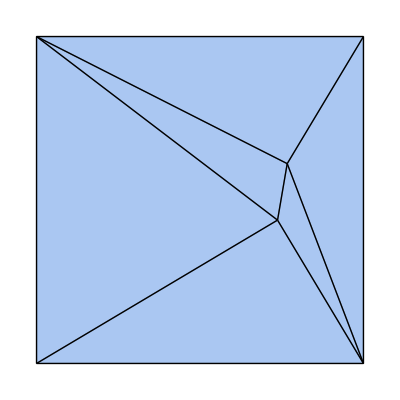

```mathematica
m=Module[{m0=randomOrigami[2],foldindex},
foldindex=First[SelectFirst[Thread[#->Length/@listFaces[m0,#]&[listEdges[m0]]],#[[2]]==2&]];
modifyMechanism[m0,"addComponent"->{Property[fold[foldindex],{"angle"->Pi/2}]}]
]
```

```mathematica
mechanisms`Private`minimizeEnergyArgumentsQ[m,mechanismEnergy[m],Automatic]
```

True

```mathematica
mechanisms`Private`analyticEnergyQ[mechanismEnergy[m],m["positions"]]
```

True

```mathematica
minimizeEnergy[m,MaxIterations->10^4]
```

{1.14593×10^-18,{{0.506472,-0.50326,0.473054},{0.647911,0.69279,-0.268202},{-0.567495,0.53981,0.438469},{-0.661162,-0.656446,-0.309995},{0.411565,-0.118845,-0.131803},{0.375459,0.116277,-0.201523}}}

```mathematica
{timing,{en,config}}=With[{t=mechanismEnergy[m]},Timing[minimizeEnergy[m,t,MaxIterations->10^4]]]
```

{0.01933,{1.14593×10^-18,{{0.506472,-0.50326,0.473054},{0.647911,0.69279,-0.268202},{-0.567495,0.53981,0.438469},{-0.661162,-0.656446,-0.309995},{0.411565,-0.118845,-0.131803},{0.375459,0.116277,-0.201523}}}}

```mathematica
plotMechanism[m,config]
```

-Graphics3D-

```mathematica
{timing,{en,config}}=With[{t=compiledMechanismEnergy[m]},Timing[minimizeEnergy[m,t,MaxIterations->10^4]]]
```

{0.012651,{7.52239×10^-19,{{0.506471,-0.503261,0.473054},{0.647913,0.692789,-0.268201},{-0.567494,0.539812,0.438469},{-0.661163,-0.656444,-0.309995},{0.411565,-0.118846,-0.131804},{0.375459,0.116276,-0.201522}}}}

```mathematica
plotMechanism[m,config]
```

-Graphics3D-

```mathematica
m2=modifyMechanism[m,"add"->{Property[joint[1],"position"->{0,0,0}]}];
```

```mathematica
mechanisms`Private`pinnedJoints[m2,m2["positions"]]
```

{vertexPosition[1,x]→0,vertexPosition[1,y]→0,vertexPosition[1,z]→0}

```mathematica
With[{t=mechanismEnergy[m2]},Timing[minimizeEnergy[m2,t,MaxIterations->10^4]]]
```

{0.021353,{1.6078×10^-20,{{0,0,0},{-0.00139356,1.28176,0.597571},{-0.196026,0.188013,1.47269},{-1.27424,-0.102314,0.604845},{-0.348553,0.588484,0.234163},{-0.327067,0.762594,0.409293}}}}

### repeatedMinimizeEnergy[]

```mathematica
Options[repeatedMinimizeEnergy]=Join[{"MaxEnergy"->Infinity},Options[randomDisplacements],Options[minimizeEnergy]];
SetAttributes[repeatedMinimizeEnergy,HoldRest];
```

```mathematica
repeatedMinimizeEnergy::numneg="Number of repetitions should be a positive integer.";
repeatedMinimizeEnergy::energy="Energy is not numerical at initial condition.";
repeatedMinimizeEnergy::max="Option \"MaxEnergy\" does not have a valid value.";
repeatedMinimizeEnergy::pos="Initial positions are not numerical and valid.";
repeatedMinimizeEnergy::cvmit="Excluding `1` non-convergent results.";
repeatedMinimizeEnergy::comp="Compiled energy has non-numerical data.";
```

```mathematica
repeatedMinimizeEnergy[m:mechanismPattern,energy_:Automatic,num_Integer,opt:OptionsPattern[]]:=With[
{
	initialPosition=If[OptionValue["initial"]===Automatic,m["positions"],OptionValue["initial"]],
	energyFunction=If[energy===Automatic,mechanismEnergy[m,FilterRules[{opt},Options[mechanismEnergy]]],energy]
},
	Module[{res=repeatedMinimizeEnergyInternal[
		m,
		initialPosition,
		energyFunction[m,energy,FilterRules[{opt},Options[mechanismEnergy]]],
		num,
		OptionValue["MaxEnergy"],
		FilterRules[{opt},Options[randomDisplacements]],
		FilterRules[{opt},Options[FindMinimum]]
	]},
		res/;Head[res]=!=repeatedMinimizeEnergyInternal
	]/;repeatedMinimizeEnergyArgumentsQ[m,energyFunction,initialPosition,num,OptionValue["MaxEnergy"]]
]
```

```mathematica
repeatedMinimizeEnergyArgumentsQ[m_,energy_,initial_,num_,maxenergy_]:=Which[
	Not[IntegerQ[num]&&num>0],
		Message[repeatedMinimizeEnergy::numneg]; False,
	Not[maxenergy===Infinity||(NumericQ[maxenergy]&&maxenergy>0)],
		Message[repeatedMinimizeEnergy::max]; False,
	Not[numericCoordinatesQ[m,initial]],
		Message[repeatedMinimizeEnergy::pos]; False,
	compiledMechanismEnergyQ[energy]&&Not[compiledNumericalMechanismEnergyQ[energy]],
		Message[minimizeEnergy::data]; False,
	Not[compiledMechanismEnergyQ[energy]]&&Not[analyticEnergyQ[energy,m["positions"]]],
		Message[minimizeEnergy::energy]; False,

	True, True
]
```

```mathematica
repeatedMinimizeEnergyInternal[m_,positions_,energy_,num_,maxenergy_,randomOptions_,minimizationOptions_]:=
Module[{output,ctr=0},
	output=Select[
		Array[
			Check[
				minimizeEnergyInternal[m,energy,positions+randomDisplacements[m,randomOptions],minimizationOptions],
				ctr++;
				{Infinity,$Failed},
				FindMinimum::cvmit
			]&,
			num
		],
		(*use only values below the maximum specified energy*)
		First[#]<maxenergy&
	];
	If[ctr>0,Message[repeatedMinimizeEnergy::cvmit,ctr]];
	If[Length[output]>0,
		Transpose[{output[[All,1]],Join[{output[[1,2]]},Last[alignMechanism[output[[1,2]],#]]&/@output[[2;;All,2]]]}],
		{}
	]
]
```

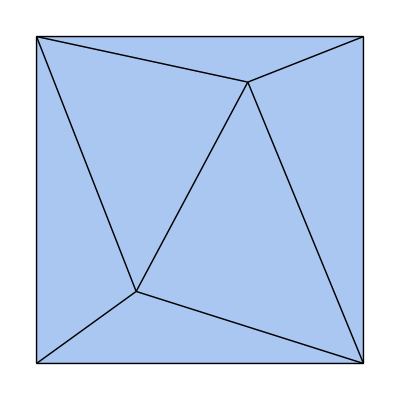

```mathematica
m=Module[{m0=randomOrigami[2],foldindex},
foldindex=First[SelectFirst[Thread[#->Length/@listFaces[m0,#]&[listEdges[m0]]],#[[2]]==2&]];
modifyMechanism[m0,"addComponent"->{Property[fold[foldindex],{"angle"->Pi/2}]}]
]
```

```mathematica
repeatedMinimizeEnergy[m,mechanismEnergy[m],2,MaxIterations->1000]
```

{{3.24059×10^-18,{{0.539721,-0.525571,-0.532489},{0.550707,0.528355,0.410442},{-0.449464,0.532385,-0.589379},{-0.361499,-0.317729,0.537373},{-0.323546,-0.469317,0.0290665},{0.0646627,0.467295,0.188813}}},{2.27698×10^-19,{{0.524248,-0.541232,-0.554706},{0.485954,0.462811,0.317464},{-0.344632,0.638497,-0.438852},{-0.489237,-0.447026,0.353956},{-0.147185,-0.290803,0.2823},{0.0962652,0.499283,0.23419}}}}

### tallyRepeatedMinimizeEnergy[]

```mathematica
Options[tallyRepeatedMinimizeEnergy]=Options[repeatedMinimizeEnergy];

tallyRepeatedMinimizeEnergy[m:mechanismPattern,num_Integer,tol:_?NumericQ:10^(-6),opt:OptionsPattern[]]:=Module[{
res=repeatedMinimizeEnergy[m,num,opt]},
	tallyRepeatedMinimizeEnergyOutput[res,tol]/;Head[res]=!=repeatedMinimizeEnergy
]
tallyRepeatedMinimizeEnergy[m:mechanismPattern,energy_,num_Integer,tol:_?NumericQ:10^(-6),opt:OptionsPattern[]]:=Module[{
res=repeatedMinimizeEnergy[m,energy,num,opt]},
	tallyRepeatedMinimizeEnergyOutput[res,tol]/;Head[res]=!=repeatedMinimizeEnergy
]

tallyRepeatedMinimizeEnergyOutput[{},_]:={}
tallyRepeatedMinimizeEnergyOutput[res_,tol_]:=With[{output=Transpose[res]},
	{Max[output[[1]]],Tally[output[[2]],Flatten[#1-#2].Flatten[#1-#2]<tol^2&]}
]
```

### findMinimalTrajectory[]

```mathematica
Options[findMinimalTrajectory]={
	"additional"->0,
	"constraints"->None,
	Method->{"ElasticBand", MaxIterations->10^5}
};
```

```mathematica
findMinimalTrajectory["Methods"]={{"ElasticBand", Join[{"stiffness"->10^(-4)},"Options[FindMinimum]"]}};

findMinimalTrajectory[ m : mechanismPattern, start_, end_, steps_, opt : OptionsPattern[] ]:=
Module[{method = Flatten[{OptionValue[Method]}], res},
	res = Switch[First[method],
		"ElasticBand",
			findMinimalTrajectoryElasticBand[m, start, end, steps, mechanismEnergy[m, "constraints"->OptionValue["constraints"]]+OptionValue["additional"], Sequence @@ Rest[method] ],
		_,
			Message[findMinimalTrajectory::meth];
			$Failed
	];
	
	res /; res =!= $Failed
]

findMinimalTrajectory::method="`1` is not a recognized method. Only \"ElasticBand\" is currently recognized.";
```

```mathematica
findMinimalTrajectory::ebstiff="Stiffness in \"ElasticBand\" method must be a positive numerical value.";
findMinimalTrajectory::ebstart="Start positions are not numeric coordinates corresponding to mechanism.";
findMinimalTrajectory::ebend="End positions are not numeric coordinates corresponding to mechanism.";
findMinimalTrajectory::steps="Number of steps should be a positive integer.";

ClearAll[findMinimalTrajectoryElasticBand];
Options[findMinimalTrajectoryElasticBand]=Join[{"stiffness"->10^(-4)},Options[FindMinimum]];

findMinimalTrajectoryElasticBand[m_, startPositions_,endPositions_, steps_, energy_, opt : OptionsPattern[]]:=
Module[{
stiffness = OptionValue["stiffness"],
fixedVertices = pinnedJoints[m, startPositions], variable, internalVariables, partialEnergy, newVariables, potentialEnergy, initialConditions,
minimizationOptions = FilterRules[{opt},Options[FindMinimum]], solution
},

	Which[
		Not[ NumericQ[stiffness] && stiffness > 0 ],
			Message[findMinimalTrajectory::ebstiff]; Return[$Failed],
		Not @ numericCoordinatesQ[m, startPositions],
			Message[findMinimalTrajectory::ebstart]; Return[$Failed],
		Not @ numericCoordinatesQ[m, endPositions],
			Message[findMinimalTrajectory::ebend]; Return[$Failed],
		Not[ IntegerQ[steps] && steps>0 ],
			Message[findMinimalTrajectory::steps]; Return[$Failed]
	];

	internalVariables= Join[
		{dataRules[vertexPosition,startPositions]},
		Flatten[MapThread[ #1 -> #2&, {vertexPosition[m], #}, 2],2]& /@ Array[variable, {steps, MeshCellCount[m,0],embeddingDimension[m]}],
		{dataRules[vertexPosition,endPositions]}
	];

	newVariables = Flatten[vertexPosition[m] /. fixedVertices] /. internalVariables;

	partialEnergy = energy /. fixedVertices;

	potentialEnergy = Total @ Flatten @ {
	(*local equations*)
	(partialEnergy /. # &) /@ internalVariables,

	(*elastic band equations*)
	(stiffness (#[[2]]-#[[1]]) . (#[[2]]-#[[1]])&) /@ Partition[newVariables, 2, 1]
	};

	initialConditions = DeleteCases[ 
		Transpose @ {Flatten[ Drop[ Rest @ newVariables, -1] ], Flatten[startPositions + (endPositions - startPositions)/(steps+1) #& /@ Range[steps] ]},
		{_?NumericQ, _}
	];

	solution = FindMinimum @@ {potentialEnergy, initialConditions, minimizationOptions };
	If[Head[solution] =!= FindMinimum, Partition[#,embeddingDimension[m]]& /@ (newVariables /. solution[[2]]), $Failed]
]
```

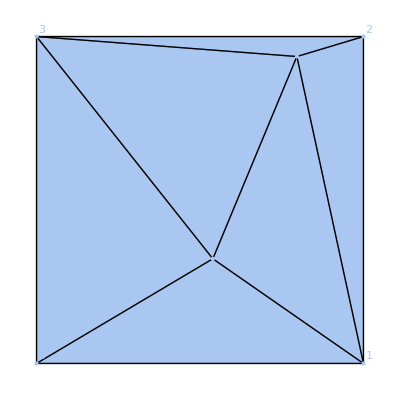

```mathematica
m=randomOrigami[2,MeshCellLabel->{0->"Index"}]
```

```mathematica
m2=addCells[m,{Property[fold[{5,6}],"angle"->Pi/2]}]
```

-Graphics3D-

```mathematica
end=minimizeEnergy[m2,MaxIterations->1000][[2]]
```

{{0.508342,-0.554704,0.463762},{0.67902,0.657952,-0.243581},{-0.552272,0.545529,0.442919},{-0.670142,-0.643939,-0.312907},{0.123664,-0.274354,-0.170995},{0.386088,0.635952,-0.179198}}

```mathematica
ClearAll[findMinimalTrajectory]
```

```mathematica
ListAnimate[plotMechanism[m2, findMinimalTrajectory[m2, m2["positions"], end, 10]]]
```

### dynamicalSystem[], dynamicalSystemEquations[]

```mathematica
Options[dynamicalSystemEquations]={
	"constraints"->None, (*a list of constraints*)
	"mass"->1,
	"drag"->0,
	"additional"->0 (*additional terms to add to the energy*)
};

Options[dynamicalSystem]=Join[
	Options[dynamicalSystemEquations],
	Options[NDSolve]
];
```

#### dynamicalSystemEquations[]

```mathematica
dynamicalSystemEquations::drag="Option \"drag\" cannot be parsed.";
dynamicalSystemEquations::mass="Option \"mass\" cannot be parsed.";
dynamicalSystemEquations::pos="Not a valid set of positions.";
dynamicalSystemEquations::var="Variables should be of the form {variable, time}.";
```

```mathematica
validEquationsParamQ[value_?NumericQ]:=value ≥ 0
validEquationsParamQ[value : Except[_List]]:=Not[NumericQ[value]]
validEquationsParamQ[_]:=False

expandEquationDrags[m_, drags_?validEquationsParamQ]:=ConstantArray[drags, MeshCellCount[m,0] ]
expandEquationDrags[m_, drags : {__?validEquationsParamQ}]:=drags /; Length[drags]==MeshCellCount[m,0]
expandEquationDrags[m_, None]:=ConstantArray[0, MeshCellCount[m,0] ]
expandEquationDrags[m_, _]:=(Message[dynamicalSystemEquations::drag]; $Failed)

expandEquationMasses[m_, masses_?validEquationsParamQ]:=ConstantArray[masses, MeshCellCount[m,0] ]
expandEquationMasses[m_, masses : {__?validEquationsParamQ}]:=masses /; Length[masses]==MeshCellCount[m,0]
expandEquationMasses[m_, None | 0]:=None
expandEquationMasses[m_, _]:=(Message[dynamicalSystemEquations::mass]; $Failed)

evaluateEquationPositions[m_, Automatic]:=m["positions"]
evaluateEquationPositions[m_, positions_]:=positions /; vertexPositionsQ[m,positions]
evaluateEquationPositions[m_, _]:=(Message[dynamicalSystemEquations::pos]; $Failed)
```

```mathematica
dynamicalSystemEquations[m : mechanismPattern, initialPositions_ : Automatic, {variableName_Symbol, timeVariable_Symbol}, opt : OptionsPattern[] ]:=
Module[{
energy = mechanismEnergy[m, "constraints" -> OptionValue["constraints"]] + OptionValue["additional"],
positions = evaluateEquationPositions[m,initialPositions],
drags = expandEquationDrags[m, OptionValue["drag"]],
masses = expandEquationMasses[m, OptionValue["mass"]]
},
	With[{res=dynamicalSystemEquationsInternal[m, positions, variableName, timeVariable, masses, drags, energy ]},
		res /; res =!= $Failed
	] /; drags =!= $Failed && masses =!= $Failed && positions =!= $Failed && variableName =!= timeVariable
]

dynamicalSystemEquations[m : mechanismPattern, initialPositions_ : Automatic, {_,_}, OptionsPattern[]]:="nothing" /; Message[dynamicalSystemEquations::vars]
dynamicalSystemEquations[m : mechanismPattern, initialPositions_ : Automatic, Except[_List] , OptionsPattern[]]:="nothing" /; Message[dynamicalSystemEquations::vars]
```

#### dynamicalSystem[]

```mathematica
dynamicalSystem::drag="Option \"drag\" cannot be parsed.";
dynamicalSystem::mass="Option \"mass\" cannot be parsed.";
dynamicalSystem::timespec="The last argument should be of the form {time variable, start time, end time} with start and end times being numerical and the time variable being a Symbol.";
```

```mathematica
validDynamicalParamQ[value_]:=NumericQ[value] && value ≥ 0

expandDynamicalDrags[m_, drags_?validDynamicalParamQ]:=ConstantArray[drags, MeshCellCount[m,0] ]
expandDynamicalDrags[m_, drags : {__?validDynamicalParamQ}]:=drags /; Length[drags]==MeshCellCount[m,0]
expandDynamicalDrags[m_, None]:=ConstantArray[0, MeshCellCount[m,0] ]
expandDynamicalDrags[m_, _]:=(Message[dynamicalSystem::drag]; $Failed)

ClearAll[expandDynamicalMasses];
expandDynamicalMasses[m_, None | 0]:= None
expandDynamicalMasses[m_, masses_?validDynamicalParamQ]:= ConstantArray[masses, MeshCellCount[m,0] ]
expandDynamicalMasses[m_, masses : {__?validDynamicalParamQ}]:= masses /; Length[masses] == MeshCellCount[m,0]
expandDynamicalMasses[m_, _]:=(Message[dynamicalSystem::mass]; $Failed)
```

```mathematica
parseInitialConditions[m_, positions : _?MatrixQ | Automatic]:={parsePositions[m, positions], parseVelocities[m, None]}
parseInitialConditions[m_, {positions : _?MatrixQ | Automatic, velocities_?MatrixQ}]:={parsePositions[m, positions], parseVelocities[m, velocities]}
parseInitialConditions[m_, _]:=$Failed

parsePositions[m_, Automatic]:=m["positions"]
parsePositions[m_, positions_?MatrixQ]:=positions /; numericCoordinatesQ[m,positions]
parsePositions[m_, positions_?MatrixQ]:=$Failed

parseVelocities[m_, velocities_]:= velocities /; numericCoordinatesQ[m, velocities]
parseVelocities[m_, None]:= ConstantArray[0, {MeshCellCount[m,0], embeddingDimension[m]}]
```

```mathematica
dynamicalSystem[m : mechanismPattern, initialConditions_ : Automatic, {time_Symbol, start_?NumericQ, end_?NumericQ}, opt : OptionsPattern[] ]:=
Module[{
energy = mechanismEnergy[m, "constraints" -> OptionValue["constraints"]] + OptionValue["additional"],
parsedInitialConditions = parseInitialConditions[m, initialConditions],
drags = expandDynamicalDrags[m, OptionValue["drag"]],
masses = expandDynamicalMasses[m, OptionValue["mass"]]
},
	With[{res=dynamicalSystemInternal[m, masses, drags, parsedInitialConditions, energy, {time, start, end}, FilterRules[{opt}, Options[NDSolve]] ]},
		res /; res =!= $Failed
	] /; drags =!= $Failed && masses =!= $Failed && parsedInitialConditions =!= $Failed
]

dynamicalSystem[m : mechanismPattern, _ : Automatic, {_,_,_} ]:="nothing" /; Message[dynamicalSystem::timespec]
dynamicalSystem[m : mechanismPattern, _ : Automatic, Except[_List] ]:="nothing" /; Message[dynamicalSystem::timespec]
```

#### dynamicalSystemEquationsInternal[], dynamicalSystemInternal[]

```mathematica
dynamicalSystemEquationsInternal[m_, initialPositions_, v_, timeVariable_, masses_, drags_, energy_]:=
Module[{pinnedVertices = Dispatch[ pinnedJoints[ m, initialPositions ] ], variables, gradient, equationSystem, i, j, t},
	variables=vertexPosition[m] /. pinnedVertices /. vertexPosition[i_, j_] :> v[i, j][t];
	gradient=Partition[ D[ energy, { Flatten[ vertexPosition[m] ] }], embeddingDimension[m] ] /. pinnedVertices /. vertexPosition[i_, j_] :> v[i, j][t];
	
	equationSystem = Flatten[
		If[masses === None, ConstantArray[0, Dimensions[initialPositions] ], DiagonalMatrix[ masses ] . D[ variables, {t, 2} ] ] 
			+ DiagonalMatrix[ drags ] . D[ variables, {t, 1} ] + gradient
	] /. t->timeVariable;

	(*we need to explicitly eliminate the equations that are predetermined by the pinned vertices or there will be too many equations*)
	Pick[ equationSystem, Not[ NumericQ[#] ]& /@ Flatten[variables] ]
]
```

```mathematica
dynamicalSystemInternal[m_, masses_, drags_, {initialPositions_, initialVelocities_}, energy_, {timeVariable_, start_, end_}, opt_]:=
Module[{equations, v, variables, processedVariables, solution, i, j, pinnedVertices = Dispatch[ pinnedJoints[ m, initialPositions ] ]},
	(*list only the non-pinned variables*)
	variables = Flatten[ vertexPosition[m] /. pinnedVertices /. vertexPosition[i_, j_] :> v[i, j][timeVariable] ];

	equations = Flatten[{
		(*the dynamical system equations*)
		dynamicalSystemEquationsInternal[m, initialPositions, v, timeVariable, masses, drags, energy],

		(*initial positions*)
		Select[ Flatten[ (variables /. timeVariable->0) - Flatten[initialPositions]], Not[ NumericQ[ # ] ]& ],

		(*initial velocities if needed*)
		If[masses === None,
			{},
			Select[ (( D[ variables, timeVariable ] /. timeVariable->0 ) - Flatten[initialVelocities]), Not[ NumericQ[ # ] ]& ]
		]
	}];
	
	solution = NDSolve[ Thread[ equations == 0 ],  Select[ variables, Not[ NumericQ[#] ] & ], {timeVariable, start, end }, opt ];

	(*did NDSolve return a list of rules?*)
	If[MatchQ[solution,{{__Rule}}],
		vertexPosition[m] /. pinnedVertices /. vertexPosition[i_, j_] :> v[i, j][timeVariable] /. solution[[1]],
		$Failed
	]
]
```

### isometricTrajectory[]

```mathematica
Options[isometricTrajectory]={
"stepsize"->1/10,
"initial"->Automatic,
"stepOptions"->{MaxIterations->10^4},
Method->"Minimization",
Tolerance->10^(-8),
"constraints"->None,
"compile"->Automatic
};
```

```mathematica
isometricTrajectory::const="Constraints contain symbolic variables.";
isometricTrajectory::ener="Energy contains symbolic variables.";
isometricTrajectory::dir="Initial direction is not numerical or is not compatible with mechanism.";
isometricTrajectory::pos="Initial positions are not numerical or are not compatible with mechanism.";
isometricTrajectory::steps="Number of steps is not a positive integer.";
isometricTrajectory::stepsize="Option \"stepsize\" should be a positive, real number.";
isometricTrajectory::compile="Option \"compile\" should be a Boolean, Automatic, or a numerical compiledMechanismEnergy[].";
isometricTrajectory::meth="Method function `1` is not valid.";
isometricTrajectory::stfunc="Step function `1` is not valid.";
isometricTrajectory::meth="Method `1` is not recognized.";
```

#### isometricTrajectory[] wrapper

```mathematica
isometricTrajectory[m : mechanismPattern, initialDirection_, steps_, opt : OptionsPattern[]]:=
With[{positions=If[OptionValue["initial"]===Automatic,m["positions"],OptionValue["initial"]]},
With[{constraints=constraintVector[positions,If[OptionValue["constraints"]===None,{},OptionValue["constraints"]]]},
	isometricTrajectoryInternal[
		m,
		{positions,initialDirection},
		{steps,OptionValue["stepsize"]},
		{OptionValue["compile"],constraints},
		{OptionValue[Method],OptionValue[Tolerance],OptionValue["stepOptions"]}
	] /; Which[ (*argument checking*)
		Not[IntegerQ[steps] && steps>0], Message[isometricTrajectory::steps]; False,
		Not[NumericQ[OptionValue["stepsize"]]&&OptionValue["stepsize"]>0], Message[isometricTrajectory::stepsize]; False,
		Not[numericCoordinatesQ[m,positions+initialDirection]], Message[isometricTrajectory::dir]; False,
		Not[BooleanQ[OptionValue["compile"]]||OptionValue["compile"]===Automatic||compiledNumericalMechanismEnergyQ[OptionValue["compile"]]||analyticEnergyQ[OptionValue["compile"],positions]],
			 Message[isometricTrajectory::compile]; False,
		Not[MatchQ[OptionValue[Method],"Minimization"|"RandomWalk"|None]],
			Message[isometricTrajectory::meth,OptionValue[Method]]; False,
		True, True
]

] /; Which[Not[numericCoordinatesQ[m,positions]], Message[isometricTrajectory::pos]; False, True,True]
]
```

#### isometricTrajectoryInternal[]

```mathematica
isometricTrajectoryInternal[m_, {initialPositions_,initialDirection_},{steps_,stepsize_},{energy_,constraintVec_},{method_,tolerance_,stepOptions_}]:=
Module[{energyTemp,out},With[
{
variables=Flatten[vertexDisplacement[m]],
blankPositions=Flatten[vertexPosition[m]],
positions=Flatten[initialPositions],
initialDirectionNormalized=Normalize[Flatten[initialDirection]],

(*figure out the constraints we want to use at 1st order and at infinite order*)
firstOrderConstraints=Join[
	constraintEquationsInternal[m,vertexPosition[m],1,m["components"]],
	reduceConstraintToOrder[vertexPosition[m],constraintVec,1]
	],
fullConstraints=Join[
	constraintEquationsInternal[m,initialPositions,Infinity,m["components"],vertexPosition],
	constraintVec
]},
With[
{
(*this function will find the numerical 1st order constraint matrix*)
constraintMatFunction=(CoefficientArrays[firstOrderConstraints/.Dispatch[Thread[blankPositions->#]],variables][[2]]&),

(*figure out the energy we want to use*)
constraintEnergy=Which[
	energy===Automatic, fullConstraints . fullConstraints,
	energy===False, fullConstraints . fullConstraints,
	energy===True, compiledMechanismEnergy[{},
		compileEnergy[m,fullConstraints . fullConstraints,{},$compilationTarget],
		compileGradient[m,fullConstraints . fullConstraints,{},$compilationTarget]],
	True, energy (*user may be passing an energy*)
	]
},
	ArrayReshape[#,{Length[#],MeshCellCount[m,0],embeddingDimension[m]}]&[ FoldList[
		(*take one step*)
		(
		energyTemp=evaluateEnergy[m,#1[[1]],constraintEnergy];
		isometricTrajectoryStep[
			{method,stepsize,tolerance},
			m,
			#1, (*the latest position and step direction*)
			{constraintMatFunction[#1[[1]]],constraintEnergy}, (* {the matrix of linear constraints, an energy associated with the constraints} *)
			variables,
			stepOptions]
		)&,
		{positions,initialDirectionNormalized},
		Range[steps]
	][[All,1]] ]

]]]
```

#### isometricTrajectoryStep[]

```mathematica
isometricTrajectoryStep[{"Minimization",stepsize_,tolerance_},m_,{positions_,lastDirection_},{constraintMat_,constraintEnergy_},var_,stepOptions_]:=
Module[{
	nullspaceBasis=Orthogonalize[NullSpace[constraintMat,FilterRules[stepOptions,Options[NullSpace]]]],
	newDirection,
	trialStep
},
	newDirection=If[Length[nullspaceBasis]>0,
		Normalize[Transpose[nullspaceBasis] . nullspaceBasis . lastDirection],

		Message[isometricTrajectory::dirns,positions];
		ConstantArray[0,Length[positions]]
	];
	trialStep=positions+ stepsize newDirection;
	{
	If[ evaluateEnergy[m, trialStep, constraintEnergy] > tolerance,
		Flatten[minimizeEnergyInternal[m,constraintEnergy, Partition[positions+stepsize newDirection,embeddingDimension[m]], FilterRules[stepOptions,Options[FindMinimum]]][[2]]],
		trialStep
	],
	newDirection
	}
]
```

```mathematica
isometricTrajectoryStep[{"RandomWalk",stepsize_,tolerance_},m_,{positions_,lastDirection_},{constraintMat_,constraintEnergy_},var_,stepOptions_]:=
Module[{
nullspaceBasis=Orthogonalize[NullSpace[constraintMat,FilterRules[stepOptions,Options[NullSpace]]]],
newDirection,trialStep
},
	newDirection=If[Length[nullspaceBasis]>0,
		Normalize[RandomReal[{-stepsize,stepsize},Length[nullspaceBasis]] . nullspaceBasis],

		Message[isometricTrajectory::dirns,positions];
		ConstantArray[0,Length[positions]]
	];
	trialStep=positions+ stepsize newDirection;
	{
	If[ evaluateEnergy[m, trialStep, constraintEnergy] > tolerance,
		Flatten[minimizeEnergyInternal[m,constraintEnergy, Partition[positions+stepsize newDirection,embeddingDimension[m]], FilterRules[stepOptions,Options[FindMinimum]]][[2]]],
		trialStep
	],
	newDirection
	}
]
```

```mathematica
isometricTrajectoryStep[{None,stepsize_,tolerance_},m_,{positions_,lastDirection_},{constraintMat_,constraintEnergy_},var_,stepOptions_]:=
Module[{
	nullspaceBasis=Orthogonalize[NullSpace[constraintMat,FilterRules[stepOptions,Options[NullSpace]]]],
	newDirection
},
	newDirection=If[Length[nullspaceBasis]>0,
		Normalize[Transpose[nullspaceBasis] . nullspaceBasis . lastDirection],

		Message[isometricTrajectory::dirns,positions];
		ConstantArray[0,Length[positions]]
	];
	{positions+stepsize newDirection,newDirection}
]
```

#### example

```mathematica
m=mechanismPositions[(m0=randomOrigami[1])->displaceVertices[m0,Thread[Range[5,5+2]->({0,0,#}&/@RandomReal[{-0.2,0.2},3])]]]
im=Chop[infinitesimalMotions[m,"constraints"->{ vertexDisplacement[1,All[3]],vertexDisplacement[2,{"x","z"}],vertexDisplacement[3,"z"]},"variables"->c]]
```

-Graphics3D-

{{{0,0,0},{0,0,0},{0,0.11257 c[1],0},{0,0.11257 c[1],0.985312 c[1]},{-0.0260035 c[1],0,0.0560433 c[1]}},{}}

```mathematica
initialDir=D[im[[1]],c[1]];
```

```mathematica
c=compiledMechanismEnergy[m,"constraints"->( {vertexDisplacement[1,All[3]],vertexDisplacement[2,{"x","z"}],vertexDisplacement[3,"z"]})];
```

```mathematica
Timing[test=isometricTrajectory[m,initialDir,300,Tolerance->10^(-3),
"stepsize"->0.01,"compile"->c,"constraints"->{vertexDisplacement[1,All[3]],vertexDisplacement[2,{"x","z"}],vertexDisplacement[3,"z"]}];]
```

{0.113099,Null}

```mathematica
ListAnimate[plotMechanism[m,test]]
```

```mathematica
With[{c=compiledMechanismEnergy[m,"constraints"->( {vertexDisplacement[1,All[3]],vertexDisplacement[2,{"x","z"}],vertexDisplacement[3,"z"]})]},mechanisms`Private`evaluateEnergy[m,#,c]&/@test]
```

{1.58023×10^-31,1.33961×10^-8,5.37079×10^-8,1.2112×10^-7,2.15814×10^-7,3.37971×10^-7,4.8777×10^-7,6.65388×10^-7,8.71×10^-7,1.10478×10^-6,1.3669×10^-6,1.65752×10^-6,1.97682×10^-6,2.32495×10^-6,2.70208×10^-6,3.10838×10^-6,3.54399×10^-6,4.00908×10^-6,4.50378×10^-6,5.02827×10^-6,5.58268×10^-6,6.16715×10^-6,6.78184×10^-6,7.42687×10^-6,8.10239×10^-6,8.80853×10^-6,9.54543×10^-6,0.0000103132,0.000011112,0.0000119419,0.000012803,0.0000136956,0.0000146196,0.0000155752,0.0000165625,0.0000175815,0.0000186325,0.0000197155,0.0000208306,0.0000219779,0.0000231575,0.0000243695,0.0000256139,0.0000268908,0.0000282003,0.0000295425,0.0000309175,0.0000323253,0.0000337659,0.0000352395,0.0000367461,0.0000382858,0.0000398586,0.0000414645,0.0000431036,0.0000447759,0.0000464815,0.0000482205,0.0000499927,0.0000517983,0.0000536373,0.0000555097,0.0000574155,0.0000593548,0.0000613274,0.0000633335,0.0000653731,0.0000674461,0.0000695525,0.0000716923,0.0000738655,0.0000760721,0.0000783121,0.0000805853,0.0000828918,0.0000852316,0.0000876046,0.0000900107,0.00009245,0.0000949222,0.0000974275,0.0000999656,0.000102537,0.00010514,0.000107777,0.000110446,0.000113147,0.000115881,0.000118647,0.000121445,0.000124275,0.000127137,0.000130031,0.000132956,0.000135913,0.000138901,0.00014192,0.00014497,0.000148051,0.000151162,0.000154304,0.000157475,0.000160677,0.000163908,0.000167169,0.000170458,0.000173777,0.000177124,0.0001805,0.000183903,0.000187334,0.000190793,0.000194279,0.000197791,0.000201329,0.000204894,0.000208484,0.000212099,0.000215739,0.000219404,0.000223092,0.000226804,0.000230538,0.000234295,0.000238074,0.000241875,0.000245696,0.000249538,0.0002534,0.000257281,0.00026118,0.000265098,0.000269033,0.000272985,0.000276954,0.000280937,0.000284936,0.000288949,0.000292976,0.000297015,0.000301067,0.00030513,0.000309204,0.000313288,0.000317381,0.000321482,0.000325592,0.000329708,0.000333831,0.000337959,0.000342092,0.000346229,0.000350369,0.000354512,0.000358656,0.000362802,0.000366947,0.000371093,0.000375237,0.000379379,0.000383519,0.000387655,0.000391788,0.000395916,0.000400039,0.000404156,0.000408266,0.00041237,0.000416466,0.000420554,0.000424634,0.000428704,0.000432766,0.000436817,0.000440858,0.000444888,0.000448907,0.000452915,0.000456911,0.000460896,0.000464868,0.000468828,0.000472775,0.00047671,0.000480631,0.00048454,0.000488436,0.000492319,0.000496189,0.000500046,0.00050389,0.000507721,0.000511539,0.000515345,0.000519137,0.000522917,0.000526685,0.000530441,0.000534184,0.000537916,0.000541636,0.000545345,0.000549043,0.00055273,0.000556407,0.000560073,0.00056373,0.000567377,0.000571014,0.000574643,0.000578263,0.000581874,0.000585478,0.000589074,0.000592663,0.000596245,0.000599821,0.00060339,0.000606954,0.000610512,0.000614066,0.000617614,0.000621159,0.000624699,0.000628236,0.00063177,0.000635301,0.000638829,0.000642356,0.00064588,0.000649404,0.000652926,0.000656448,0.00065997,0.000663491,0.000667013,0.000670536,0.00067406,0.000677585,0.000681112,0.000684641,0.000688173,0.000691707,0.000695244,0.000698785,0.000702329,0.000705877,0.00070943,0.000712987,0.000716549,0.000720116,0.000723688,0.000727267,0.000730851,0.000734441,0.000738038,0.000741642,0.000745253,0.000748871,0.000752497,0.000756131,0.000759772,0.000763422,0.000767081,0.000770749,0.000774425,0.000778111,0.000781807,0.000785512,0.000789227,0.000792953,0.000796689,0.000800435,0.000804193,0.000807962,0.000811742,0.000815534,0.000819338,0.000823154,0.000826982,0.000830823,0.000834676,0.000838543,0.000842423,0.000846316,0.000850223,0.000854143,0.000858078,0.000862028,0.000865992,0.00086997,0.000873964,0.000877974,0.000881998,0.000886039,0.000890096,0.000894169,0.000898259,0.000902366,0.00090649,0.000910632}

```mathematica
With[{c=mechanismEnergy[m,"constraints"->( {vertexDisplacement[1,All[3]],vertexDisplacement[2,{"x","z"}],vertexDisplacement[3,"z"]})]},mechanisms`Private`evaluateEnergy[m,#,c]&/@test]
```

{1.42519×10^-31,1.33961×10^-8,5.37079×10^-8,1.2112×10^-7,2.15814×10^-7,3.37971×10^-7,4.8777×10^-7,6.65388×10^-7,8.71×10^-7,1.10478×10^-6,1.3669×10^-6,1.65752×10^-6,1.97682×10^-6,2.32495×10^-6,2.70208×10^-6,3.10838×10^-6,3.54399×10^-6,4.00908×10^-6,4.50378×10^-6,5.02827×10^-6,5.58268×10^-6,6.16715×10^-6,6.78184×10^-6,7.42687×10^-6,8.10239×10^-6,8.80853×10^-6,9.54543×10^-6,0.0000103132,0.000011112,0.0000119419,0.000012803,0.0000136956,0.0000146196,0.0000155752,0.0000165625,0.0000175815,0.0000186325,0.0000197155,0.0000208306,0.0000219779,0.0000231575,0.0000243695,0.0000256139,0.0000268908,0.0000282003,0.0000295425,0.0000309175,0.0000323253,0.0000337659,0.0000352395,0.0000367461,0.0000382858,0.0000398586,0.0000414645,0.0000431036,0.0000447759,0.0000464815,0.0000482205,0.0000499927,0.0000517983,0.0000536373,0.0000555097,0.0000574155,0.0000593548,0.0000613274,0.0000633335,0.0000653731,0.0000674461,0.0000695525,0.0000716923,0.0000738655,0.0000760721,0.0000783121,0.0000805853,0.0000828918,0.0000852316,0.0000876046,0.0000900107,0.00009245,0.0000949222,0.0000974275,0.0000999656,0.000102537,0.00010514,0.000107777,0.000110446,0.000113147,0.000115881,0.000118647,0.000121445,0.000124275,0.000127137,0.000130031,0.000132956,0.000135913,0.000138901,0.00014192,0.00014497,0.000148051,0.000151162,0.000154304,0.000157475,0.000160677,0.000163908,0.000167169,0.000170458,0.000173777,0.000177124,0.0001805,0.000183903,0.000187334,0.000190793,0.000194279,0.000197791,0.000201329,0.000204894,0.000208484,0.000212099,0.000215739,0.000219404,0.000223092,0.000226804,0.000230538,0.000234295,0.000238074,0.000241875,0.000245696,0.000249538,0.0002534,0.000257281,0.00026118,0.000265098,0.000269033,0.000272985,0.000276954,0.000280937,0.000284936,0.000288949,0.000292976,0.000297015,0.000301067,0.00030513,0.000309204,0.000313288,0.000317381,0.000321482,0.000325592,0.000329708,0.000333831,0.000337959,0.000342092,0.000346229,0.000350369,0.000354512,0.000358656,0.000362802,0.000366947,0.000371093,0.000375237,0.000379379,0.000383519,0.000387655,0.000391788,0.000395916,0.000400039,0.000404156,0.000408266,0.00041237,0.000416466,0.000420554,0.000424634,0.000428704,0.000432766,0.000436817,0.000440858,0.000444888,0.000448907,0.000452915,0.000456911,0.000460896,0.000464868,0.000468828,0.000472775,0.00047671,0.000480631,0.00048454,0.000488436,0.000492319,0.000496189,0.000500046,0.00050389,0.000507721,0.000511539,0.000515345,0.000519137,0.000522917,0.000526685,0.000530441,0.000534184,0.000537916,0.000541636,0.000545345,0.000549043,0.00055273,0.000556407,0.000560073,0.00056373,0.000567377,0.000571014,0.000574643,0.000578263,0.000581874,0.000585478,0.000589074,0.000592663,0.000596245,0.000599821,0.00060339,0.000606954,0.000610512,0.000614066,0.000617614,0.000621159,0.000624699,0.000628236,0.00063177,0.000635301,0.000638829,0.000642356,0.00064588,0.000649404,0.000652926,0.000656448,0.00065997,0.000663491,0.000667013,0.000670536,0.00067406,0.000677585,0.000681112,0.000684641,0.000688173,0.000691707,0.000695244,0.000698785,0.000702329,0.000705877,0.00070943,0.000712987,0.000716549,0.000720116,0.000723688,0.000727267,0.000730851,0.000734441,0.000738038,0.000741642,0.000745253,0.000748871,0.000752497,0.000756131,0.000759772,0.000763422,0.000767081,0.000770749,0.000774425,0.000778111,0.000781807,0.000785512,0.000789227,0.000792953,0.000796689,0.000800435,0.000804193,0.000807962,0.000811742,0.000815534,0.000819338,0.000823154,0.000826982,0.000830823,0.000834676,0.000838543,0.000842423,0.000846316,0.000850223,0.000854143,0.000858078,0.000862028,0.000865992,0.00086997,0.000873964,0.000877974,0.000881998,0.000886039,0.000890096,0.000894169,0.000898259,0.000902366,0.00090649,0.000910632}

```mathematica
Timing[test=isometricTrajectory[m,initialDir,300,Tolerance->10^(-3),Method->"RandomWalk",
"stepsize"->0.01,"compile"->c,"constraints"->{vertexDisplacement[1,All[3]],vertexDisplacement[2,{"x","z"}],vertexDisplacement[3,"z"]}];]
```

{0.122154,Null}

```mathematica
ListAnimate[plotMechanism[m,test]]
```

## graphics

### toMeshRegion[]

```mathematica
Options[toMeshRegion]=Options[MeshRegion];

toMeshRegion[m : mechanismPattern,positions: Except[_Rule] : Automatic,opt:OptionsPattern[]]:=
With[{pos=If[positions===Automatic,m["positions"],positions]},
	MeshRegion[
		pos,
		meshCells[m["mesh"]],
		Join[Method->{"CoplanarityTolerance"->100},opt]
	] /; numericCoordinatesQ[m,pos]
]

toMeshRegion::pos="Positions are not numeric or do not correspond to mechanism.";
toMeshRegion[m : mechanisnPattern,pos : Except[_Rule|Automatic] ,OptionsPattern[]]:="nothing"/;Message[toMeshRegion::pos]
```

```mathematica
?toMeshRegion
```

### mechanismPrimitives[]

```mathematica
applyDefaultStyle[{Automatic,x_Polygon}]:={LightBlue,x}
applyDefaultStyle[{Automatic,x_Line}]:={Black,x}
applyDefaultStyle[{Automatic,x_Point}]:={Black,x}
applyDefaultStyle[{x:Except[Automatic],y_}]:={x,y}
```

```mathematica
mechanismPrimitives[m : mechanismPattern, positions : Except[_Rule] : Automatic,cellspec_:All]:=
With[{
	pos=If[positions===Automatic,m["positions"],positions]
},
	With[
	{
	properties=PropertyValue[{m["mesh"],Flatten[MeshCells[m["mesh"],cellspec]]},MeshCellStyle],
	primitives=Flatten[MeshPrimitives[mechanismPositions[m->pos]["mesh"],cellspec]]
	},
	applyDefaultStyle/@Transpose[{properties,primitives}]
	] /; numericCoordinatesQ[m,pos]
]
```

```mathematica
mechanismPrimitives::pos="Positions are not numeric or do not correspond to provided mechanism.";

mechanismPrimitives[m:mechanismPattern,__]:="nothing"/;Message[mechanismPrimitives::pos]
```

```mathematica
?mechanismPrimitives
```

```mathematica
Show @@ Graphics3D/@mechanismPrimitives[m=randomOrigami[3]]
```

-Graphics3D-

### toGraphics[]

```mathematica
Options[toGraphics]=Options[Show];

toGraphics[m : mechanismPattern,positions: Except[_Rule] : Automatic,cellspec: _Integer|All : All, opt:OptionsPattern[]]:=
With[{
	pos=If[positions===Automatic,m["positions"],positions]
},
	Show[
		If[embeddingDimension[m]==3,Graphics3D,Graphics]/@mechanismPrimitives[m,pos,cellspec],
		opt
	]/;numericCoordinatesQ[m,pos]
]

toGraphics::pos="Positions are not valid or do not correspond to mechanism.";
toGraphics::cellspec="Cell specification is not an integer.";

toGraphics[m : mechanismPattern, Except[_Rule|Automatic], ___]:="nothing" /; Message[toGraphics::pos]
toGraphics[m : mechanismPattern, _, Except[ _Rule|All|_Integer ], ___]:="nothing" /; Message[toGraphics::cellspec]
```

```mathematica
Show[toGraphics[m=randomOrigami[3]],Boxed->False]
```

-Graphics3D-

### plotDisplacement[]

```mathematica
Options[plotDisplacement]=Join[{"scale"->1},Options[Show]];
```

```mathematica
plotDisplacement[m : mechanismPattern , displacement_?(MatrixQ[#,NumericQ]&), opt:OptionsPattern[]]:=
With[{
	scale=Last@BoundingRegion[m["positions"],If[embeddingDimension[m]==2,"MinDisk","MinBall"]],
	graphics=If[embeddingDimension[m]==2,Graphics,Graphics3D]
},
	Show[
		MapThread[graphics[{
			Red,
			Arrow[{#1,#1+OptionValue["scale"] scale #2}]
		}]&,{m["positions"],displacement}],
		FilterRules[{opt},Options[Show]]
	]
] /; Dimensions[displacement]=={MeshCellCount[m,0],embeddingDimension[m]}
```

### plotTension[]

```mathematica
doublearrow[{start_,end_},{max_,min_},data_]:=With[
{displacement=(end-start)/2,center=(start+end)/2,scale=data/(max-min),dim=If[Length[start]==3,Graphics3D,Graphics]},
	dim[{
		If[Sign[data]>0,Blue,Red],
		Thickness[0.0075],
		Arrowheads[Sign[data] {-0.1,0.1}],
		Arrow[{center-scale displacement,center+scale displacement}]}
	]
]

arrow[{start_,end_},{max_,min_},data_]:=With[
{displacement=(end-start)/2,center=(start+end)/2,scale=2 data/(max-min),dim=If[Length[start]==3,Graphics3D,Graphics]},
	dim[{
		If[Sign[data]>0,Blue,Red],
		Thickness[0.0075],
		Arrowheads[{0.1}],
		Arrow[{center-9 scale displacement/10,center+9 scale displacement/10}]}
	]
]
```

```mathematica
Options[plotTension]=Options[Show];
plotTension[m : mechanismPattern, Rule[edges_?(MatrixQ[#,IntegerQ]&),data_?(VectorQ[#,NumericQ]&)],opt:OptionsPattern[]]:=
With[
{
pos=PadRight[m["positions"],{Length[m["positions"]],displayDimension[m]}],
dataMax=Max[data],dataMin=Min[data]
},
	Show[
		m["mesh"],
		MapThread[doublearrow[pos[[#1]],{dataMax,dataMin},#2]&,{edges,data}],
		opt
	]
]
```

### plotMechanism[]

```mathematica
Options[plotMechanism]=Options[Show];
```

```mathematica
plotMechanism[m : mechanismPattern, pos: _?MatrixQ|Automatic : Automatic, opt : OptionsPattern[]]:=
Module[{
	positions=If[pos===Automatic,m["positions"],pos],
	boundingRegion,boundingBoxRatios,size
},
	boundingRegion=Transpose[List@@Quiet[
		BoundingRegion[positions,If[embeddingDimension[m]==2,"MinRectangle","MinCuboid"]],
		BoundingRegion::degbr]];
	size=ConstantArray[{-#,#}, Length[boundingRegion] ] &[ Max[#[[2]]-#[[1]]&/@boundingRegion]/10 ];

	boundingBoxRatios=#[[2]]-#[[1]]&/@(boundingRegion+size);
	
	Show[
		mechanismPositions[m->positions]["mesh"],
		Join[{opt},{PlotRange->(boundingRegion+size),BoxRatios->boundingBoxRatios}]
	] /; numericCoordinatesQ[m, positions]
]
```

```mathematica
(*a list of positions in 2D*)
plotMechanism[m : mechanismPattern, positions_?(ArrayQ[#,_,NumericQ]&),opt:OptionsPattern[]]:=Module[
{
	boundingRegion=Transpose[List@@Quiet[BoundingRegion[Flatten[positions,1],"MinRectangle"],BoundingRegion::degbr]],
	plotRegion,boundingBoxRatios
},
	plotRegion=boundingRegion + ConstantArray[{-#,#}, Length[boundingRegion] ] &[ Max[#[[2]]-#[[1]]&/@boundingRegion]/10 ];
	boundingBoxRatios=#[[2]]-#[[1]]&/@plotRegion;

	Show[
		mechanismPositions[m->#]["mesh"],
		Join[{opt},{PlotRange->plotRegion,BoxRatios->boundingBoxRatios}]
	]&/@positions
]/; Drop[Dimensions[positions],1]=={MeshCellCount[m,0],2} && embeddingDimension[m]==2
```

```mathematica
(*a list of positions in 3D*)
plotMechanism[m_?mechanismQ,positions_?(ArrayQ[#,_,NumericQ]&),opt:OptionsPattern[]]:=Module[
{
	boundingRegion=Transpose[List@@Quiet[BoundingRegion[Flatten[positions,1],"MinCuboid"],BoundingRegion::degbr]],
	plotRegion,boundingBoxRatios
},
	plotRegion=boundingRegion + ConstantArray[{-#,#}, Length[boundingRegion] ] &[ Max[#[[2]]-#[[1]]&/@boundingRegion]/10 ];
	boundingBoxRatios=(#[[2]]-#[[1]])& /@ plotRegion;

	Show[
		mechanismPositions[m->#]["mesh"],
		Join[{opt},{PlotRange->plotRegion, BoxRatios->boundingBoxRatios}]
	]&/@positions
]/; Drop[Dimensions[positions],1]=={MeshCellCount[m,0],3} && embeddingDimension[m]==3
```

```mathematica
plotMechanism::pos="Positions are either not numerical or do not correspond to provided mechanism.";

plotMechanism[m : mechanismPattern, Except[_Rule|Automatic], OptionsPattern[]]:="nothing"/;Message[plotMechanism::pos]
```

```mathematica
m=mechanismPositions[(m0=randomOrigami[2])->displaceVertices[m0,Thread[Range[5,5+2]->({0,0,#}&/@RandomReal[{-0.2,0.2},3])]]]
im=Chop[infinitesimalMotions[m,"constraints"->{vertexDisplacement[1,All[3]],vertexDisplacement[2,{"x","z"}],vertexDisplacement[3,"z"]},"variables"->c]];
initialDir=D[im[[1]],c[1]];
Timing[test=isometricTrajectory[m,initialDir,50,"constraints"->{vertexDisplacement[1,All[3]]}];]
```

-Graphics3D-

{0.269269,Null}

```mathematica
Transpose[List@@BoundingRegion[Flatten[test,1],"MinCuboid"]]
```

{{-0.707107,1.2764},{-0.707107,0.709485},{-0.185783,1.2705}}

```mathematica
Show[plotMechanism[m,test]]
```

-Graphics3D-

### angleMarker[], angleText[]

```mathematica
angleText[m : mechanismPattern, {v1_Integer,v2_Integer,v3_Integer}, label_ : "",distance : _?NumericQ : 0]:=With[
{
	angleLocation=m["positions"][[v2,1;;displayDimension[m]]],
	vectors=-displacementVector[m["positions"],{{v3,v2},{v1,v2}}][[All,1;;displayDimension[m]]]
},
	Text[label,angleLocation + (distance+0.12) Mean[vectors]]
]
```

```mathematica
angleMarker[m : mechanismPattern, {v1_Integer,v2_Integer,v3_Integer}, radius : _?NumericQ : 1/10]:=With[
{
	(*project the vectors making this angle to the xy-plane*)
	angleLocation=m["positions"][[v2,1;;2]],
	vectors=displacementVector[m["positions"],{{v2,v1},{v2,v3}}][[All,1;;2]]
},
	Circle[angleLocation,
		Abs[radius] Sqrt[Min[vectors[[1]] . vectors[[1]],vectors[[2]] . vectors[[2]]]],
		(If[Pi+#[[2]]<Pi+#[[1]],{0,2Pi}+#,#]&)[ArcTan@@@vectors]
	]
] /; displayDimension[m]==2 && Max[{v1,v2,v3}]≤MeshCellCount[m,0] && Min[{v1,v2,v3}]>0
```

```mathematica
(*Code borrowed from https://mathematica.stackexchange.com/questions/10957/an-efficient-circular-arc-primitive-for-graphics3d*)
ClearAll[splineCircle2];
splineCircle[m_List, r_, angles_List: {0., 2. π}] := 
 Module[{seg, ϕ, start, end, pts, w, k, pihalf},
   pihalf = 0.5 π;
   {start, end} = Mod[N[angles], 2. π];
   If[end <= start, end += 2. π];
   seg = Quotient[N[end - start], pihalf];
   ϕ = Mod[N[end - start], pihalf];
   If[seg == 4, seg = 3; ϕ = pihalf];
   With[{
     cseg = Cos[pihalf seg], sseg = Sin[pihalf seg],
     cϕ = Cos[ϕ], sϕ = Sin[ϕ], 
     tϕ = Tan[0.5 ϕ],
     rcs = r Cos[start], rss = r Sin[start]
     },
    pts = Join[
       Take[{{1., 0.}, {1., 1.}, {0., 1.}, {-1., 1.}, {-1., 0.}, {-1., -1.}, {0., -1.}}, 2 seg + 1],
       {{cseg - sseg tϕ, sseg + cseg tϕ}, {cseg cϕ - sseg sϕ, cϕ sseg + cseg sϕ}}
       ].{{rcs, rss}, {-rss, rcs}}
    ];
   pts = ConstantArray[m, Length[pts]] + 
     If[Length[m] == 2, 
      pts, 
      Join[pts, ConstantArray[{0.}, Length[pts]], 2]
     ];
   w = With[{c = 1./Sqrt[2.]}, 
     Join[Take[{1., c, 1., c, 1., c, 1.}, 2 seg + 1], {Cos[0.5 ϕ], 1.}]
     ];
   k = Join[{0, 0, 0}, Riffle[#, #] &@Range[seg + 1], {seg + 1}];
   BSplineCurve[pts, SplineDegree -> 2, SplineKnots -> k, SplineWeights -> w]
   ] /; Length[m] == 2 || Length[m] == 3
 
Options[circleFromPoints] = {arc -> False};

circleFromPoints[m : {q1_, q2_, q3_}, OptionsPattern[]] :=
Module[{c, r, ϕ1, ϕ2, p1, p2, p3, h, 
        rot = Quiet[RotationMatrix[{{0, 0, 1}, Cross[#1 - #2, #3 - #2]}],RotationMatrix::spln] &},
  {p1, p2, p3} = {q1, q2, q3}.rot[q1, q2, q3];
  h = p1[[3]];
  {p1, p2, p3} = {p1, p2, p3}[[All, ;; 2]];
  {c, r} = List @@ Circumsphere[{p1, p2, p3}];
  ϕ1 = ArcTan @@ (p3 - c);
  ϕ2 = ArcTan @@ (p1 - c);
  c = Append[c, h];
  If[OptionValue[arc] // TrueQ,
    MapAt[Function[{p}, rot[q1, q2, q3].p] /@ # &, splineCircle[c, r, {ϕ1, ϕ2}], {1}],
    MapAt[Function[{p}, rot[q1, q2, q3].p] /@ # &, splineCircle[c, r], {1}]
  ]
] /; MatrixQ[m, NumericQ] && Dimensions[m] == {3, 3}
```

```mathematica
angleMarker[m : mechanismPattern, {v1_Integer,v2_Integer,v3_Integer}, radius : _?NumericQ : 1/10]:=With[
{
	angleLocation=m["positions"][[v2]],
	(*project the vectors making this angle to the xy-plane*)
	vectors=displacementVector[m["positions"],{{v2,v1},{v2,v3}}]
},
	circleFromPoints[{angleLocation+radius vectors[[1]],angleLocation+radius (vectors[[1]]+vectors[[2]])/Sqrt[2],angleLocation+radius vectors[[2]]},arc ->True]
] /; displayDimension[m]==3 && Max[{v1,v2,v3}]≤MeshCellCount[m,0] && Min[{v1,v2,v3}]>0
```

```mathematica
angleMarker::bounds="Vertices are out of bounds.";
angleMarker[m : mechanismPattern, {v1_Integer,v2_Integer,v3_Integer}]:="nothing"/;Message[angleMarker::bounds]
angleMarker[m : mechanismPattern, {v1_Integer,v2_Integer,v3_Integer},_]:="nothing"/;Message[angleMarker::bounds]
angleMarker[m : mechanismPattern, {v1_Integer,v2_Integer,v3_Integer},_,_?NumericQ]:="nothing"/;Message[angleMarker::bounds]
```

## periodicity tools-EXPERIMENTAL

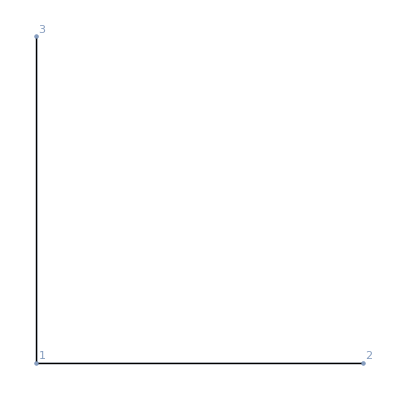

```mathematica
unitCell=framework[
{{0,0},{1,0},{0,1}},
{
rigidBar[{1,#}]&/@Range[2,3]
},

MeshCellLabel->{0->"Index"}
]
```

```mathematica
displacements=Flatten[Thread/@{
vertexDisplacement[2,All[2]]->zx vertexDisplacement[1,All[2]],
vertexDisplacement[3,All[2]]->zy vertexDisplacement[1,All[2]]
}];
```

```mathematica
eq=constraintEquations[unitCell,1]//.displacements
```

{2 (-vertexDisplacement[1,x]+zx vertexDisplacement[1,x]),2 (-vertexDisplacement[1,y]+zy vertexDisplacement[1,y])}

```mathematica
MatrixForm[CoefficientArrays[eq,vertexDisplacement[1,All[2]]][[2]]]
```

(-2+2 zx | 0
0 | -2+2 zy)

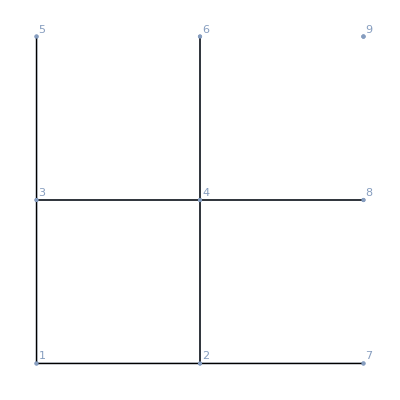

```mathematica
m=tesselateMechanism[framework[
{{0,0},{1,0},{0,1},{1,1}},
{
rigidBar[{1,#}]&/@Range[2,3]
},

MeshCellLabel->{0->"Index"}
]
,{{1,0},{0,1}},{2,2}]
```

```mathematica
positions=Flatten[{
vertexPosition[9,All[2]]-vertexPosition[5,All[2]]-(vertexPosition[7,All[2]]-vertexPosition[1,All[2]]),
vertexPosition[8,All[2]]-vertexPosition[3,All[2]]-(vertexPosition[7,All[2]]-vertexPosition[1,All[2]]),

vertexPosition[5,All[2]]-vertexPosition[1,All[2]]-(vertexPosition[9,All[2]]-vertexPosition[7,All[2]]),
vertexPosition[6,All[2]]-vertexPosition[2,All[2]]-(vertexPosition[9,All[2]]-vertexPosition[7,All[2]])
}];
Length[positions]
```

8

```mathematica
Solve[positions==0,{vertexPosition[9,"x"],vertexPosition[9,"y"],vertexPosition[8,"x"],vertexPosition[8,"y"],vertexPosition[5,"x"],vertexPosition[5,"y"],vertexPosition[6,"x"],vertexPosition[6,"y"]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{vertexPosition[8,x]→-vertexPosition[1,x]+vertexPosition[3,x]+vertexPosition[7,x],vertexPosition[8,y]→-vertexPosition[1,y]+vertexPosition[3,y]+vertexPosition[7,y],vertexPosition[5,x]→vertexPosition[1,x]-vertexPosition[7,x]+vertexPosition[9,x],vertexPosition[5,y]→vertexPosition[1,y]-vertexPosition[7,y]+vertexPosition[9,y],vertexPosition[6,x]→vertexPosition[2,x]-vertexPosition[7,x]+vertexPosition[9,x],vertexPosition[6,y]→vertexPosition[2,y]-vertexPosition[7,y]+vertexPosition[9,y]}}

```mathematica
Simplify[mechanismEnergy[m]//.First@Solve[positions==0,{vertexPosition[9,"x"],vertexPosition[9,"y"],vertexPosition[8,"x"],vertexPosition[8,"y"],vertexPosition[5,"x"],vertexPosition[5,"y"],vertexPosition[6,"x"],vertexPosition[6,"y"]}]
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

1/2 ((-1+(vertexPosition[1,x]-vertexPosition[2,x])^2+(vertexPosition[1,y]-vertexPosition[2,y])^2)^2+(-1+(vertexPosition[1,x]-vertexPosition[3,x])^2+(vertexPosition[1,y]-vertexPosition[3,y])^2)^2+(-1+(vertexPosition[2,x]-vertexPosition[4,x])^2+(vertexPosition[2,y]-vertexPosition[4,y])^2)^2+(-1+(vertexPosition[3,x]-vertexPosition[4,x])^2+(vertexPosition[3,y]-vertexPosition[4,y])^2)^2+(-1+(vertexPosition[2,x]-vertexPosition[7,x])^2+(vertexPosition[2,y]-vertexPosition[7,y])^2)^2+(-1+(vertexPosition[1,x]-vertexPosition[3,x]+vertexPosition[4,x]-vertexPosition[7,x])^2+(vertexPosition[1,y]-vertexPosition[3,y]+vertexPosition[4,y]-vertexPosition[7,y])^2)^2+(-1+(vertexPosition[1,x]-vertexPosition[3,x]-vertexPosition[7,x]+vertexPosition[9,x])^2+(vertexPosition[1,y]-vertexPosition[3,y]-vertexPosition[7,y]+vertexPosition[9,y])^2)^2+(-1+(vertexPosition[2,x]-vertexPosition[4,x]-vertexPosition[7,x]+vertexPosition[9,x])^2+(vertexPosition[2,y]-vertexPosition[4,y]-vertexPosition[7,y]+vertexPosition[9,y])^2)^2)

### data structure for periodic mechanisms

#### periodicData[]

The periodicData[] structure contains three pieces of information - the number of vertices, the names of the transformations, and a list of vertex equivalencies.

```mathematica
periodicData[numberOfVertices_Integer,transformations_,data_]["Methods"]:={"transformations","data"}
periodicData[numberOfVertices_Integer,transformations_,data_]["transformations"]:=transformations
periodicData[numberOfVertices_Integer,transformations_,data_]["data"]:=data

Format[periodicData[numberOfVertices_Integer,transformations_,data_]]:=periodicData[transformations]
```

```mathematica
pd=periodicData[{1},{{f1,#+{1,0}&},{f2,#+{0,1}&}},{}]
```

periodicData[{1},{{f1,#1+{1,0}&},{f2,#1+{0,1}&}},{}]

```mathematica
mechanismPositions[m]
```

{{0,0},{1,0},{-1,0},{0,1},{0,-1}}

```mathematica
pd["transformations"]
```

{{f1,#1+{1,0}&},{f2,#1+{0,1}&}}

### periodicData[]

#### identificationRules[]

```mathematica
mapQ[{f_,map:_Function}]:=True
maoQ[_]:=False

identificationRules[m_?mechanismQ,f__?mapQ]:=Module[{x},With[
{
	labels={f}[[All,1]],
	maps={f}[[All,2]],
	pos=mechanismPositions[m],dim=embeddingDimension[m],
	ruleFunction=Function[{x},#[[1]]->x[#[[2]]]& ],
	vertices=listVertices[m]
},
	periodicData[
		Length[vertices],
		labels,
		vertices//. Flatten[MapThread[
			ruleFunction[#1]/@overlappingVertices[pos,#2/@pos]&,
			{labels,maps}
		]]
	]
]]
```

#### convertToUnitCells[]

```mathematica
convertToUnitCells[periodicData[numberOfVertices_Integer,transformations_,data_]]:=Module[{n,d},With[
{
startingData=data/.n_Integer:>{n,{0,0}}
},
	startingData//.{
		transformations[[1]][{n_Integer,d_}]:>{n,d+{1,0}},
		transformations[[2]][{n_Integer,d_}]:>{n,d+{0,1}}
	}
]]
```

#### periodicEquivalenceClasses[]

```mathematica
periodicEquivalenceClasses[m_?mechanismQ,pd_periodicData,elements:{__?(VectorQ[#,IntegerQ]&)}]:=
With[{unitCellRules=listVertices[m]->convertToUnitCells[pd]},
	GatherBy[
		SortBy[#,First]&/@(elements/.Dispatch[Thread[unitCellRules]]),
		{
		First/@#,
		#[[2]]-#[[1]]
		}&
	]/.Dispatch[Thread[Reverse[unitCellRules]]]
]
```

```mathematica
periodicEquivalenceClasses[m_?mechanismQ,pd_periodicData,elements:{__Integer}]:=
With[{unitCellRules=listVertices[m]->convertToUnitCells[pd]},
	Map[
		First,
		GatherBy[Thread[unitCellRules],#[[2,1]]&],
		{2}
	]
]
```

#### periodicityRules[]

```mathematica
(*
	whenever vertex1 and vertex2 are related by a transformation, periodicityRules[mechanism, periodic data, function1, {functionX, functionY}] returns
	
		function[vertex1] -> functionX and functionY applied to function[vertex2] the appropriate number of times
		
e.g.
	Thread[periodicityRules[m0,pd,{#&,{#,0,0}}&,{#+{0,1,0}&,#+{0,0,1}&}]]
	
	returns vertex1 -> {vertex2, nx,ny} where {nx,ny} are the unit cell indices.
	
	Thread/@Thread[periodicityRules[m0,pd,{vertexPosition[#,All[3]]&,vertexPosition[#,All[3]]&},{#+l[[1]]&,#+l[[2]]&}]]
	
	returns the rules related vertexPositions to each other by the periodic lattice vectors
*)
```

```mathematica
periodicityRules[m_?mechanismQ,periodicData[numberOfVertices_Integer,transformations_,data_],{rule1_Function,rule2_Function},map:{__Function}]:=
	Module[{n},With[{
		mapRules=Thread[transformations->map],
		index1=rule1/@Range[numberOfVertices],
		index2=data /. n_Integer :> rule2[n]
	},
		Thread[index1 -> index2 /. mapRules]
	]]/;Length[map]==Length[transformations]
```

### periodicCompatibilityMatrix[]

```mathematica
periodicCompatibilityMatrix[m_?mechanismQ,positions_?MatrixQ,complex_?VectorQ,opt:OptionsPattern[]]:=
Module[{mats},With[
{
periodRules=periodicityRules[m,positions,complex],
linearConstraintEquations=constraintEquations[m,positions,1],
variables=findVariables[m,complex]
},
	mats=CoefficientArrays[linearConstraintEquations//.periodRules,variables];
	If[PossibleZeroQ[mats[[1]].mats[[1]]],mats[[2]],Message[compatibilityMatrix::stressed]; mats[[2]]]
]]
```

## origami functions

### flatOrigamiQ[]

```mathematica
Options[flatOrigamiQ]={ZeroTest->Automatic,Precision->Infinity};
```

```mathematica
flatOrigamiQ::precision="Precision is not a positive real number or Infinity.";
flatOrigamiQ::zerotest="ZeroTest function must return True or False.";
```

```mathematica
computePrecision[m_,Infinity]:=Precision[m]
computePrecision[m_,precision_?NumericQ]:=Min[Precision[m],precision]/;precision>0
computePrecision[m_,_]:=$Failed
```

```mathematica
computeZeroTestFunction[Automatic,Infinity]:=PossibleZeroQ
computeZeroTestFunction[Automatic,precision:_?NumericQ|MachinePrecision]:=(Abs[#]<=10^(-precision+1)&)
computeZeroTestFunction[f_,_]:=f
```

```mathematica
flatOrigamiQ[m_origami,OptionsPattern[]]:=Module[{
	actualPrecision=computePrecision[m,OptionValue[Precision]],zerotestFunction,res
},
	zerotestFunction=computeZeroTestFunction[OptionValue[ZeroTest],actualPrecision];

	res=flatOrigamiInternalQ[m,actualPrecision,zerotestFunction];
	res/;Which[
		Head[res]=!=flatOrigamiInternalQ,
			True,
		Not[BooleanQ[zerotestFunction[0]]],
			Message[flatOrigamiQ::zerotest]; False,
		actualPrecision===$Failed,
			Message[flatOrigamiQ::precision]; False,
		True,False
	]
]
```

```mathematica
flatOrigamiInternalQ[m_,precision:_?NumericQ|Infinity,zerotestFunction_?(BooleanQ[#[0]]&)]:=
	AllTrue[gaussianCurvature[N[m,precision],interiorVertices[m]],zerotestFunction]
```

### kawasakiQ[]

```mathematica
Options[kawasakiQ]={
	ZeroTest->PossibleZeroQ,
	WorkingPrecision->Infinity
};
```

```mathematica
kawasakiQ[m_origami,opt:OptionsPattern[]]:=
With[
{
	v=interiorVertices[m],
	mNum=N[m,OptionValue[WorkingPrecision]]
},
	If[flatOrigamiQ[m,opt],
		And@@(OptionValue[ZeroTest][kawasakiAlternatingSum[mNum,#]]&/@v),
		False
	]
]/;(
	((NumericQ[OptionValue[WorkingPrecision]]&&OptionValue[WorkingPrecision]>0)||
	OptionValue[WorkingPrecision]===Infinity)&&
	BooleanQ[OptionValue[ZeroTest][0]]
)
```

```mathematica
kawasakiAlternatingSum[m_,v_Integer]:=
With[
{
	faces=RotateRight[#,1]&/@listFaces[m,v]
},
	If[OddQ[Length[faces]],
		1,
		Total[DiagonalMatrix[(-1)^# &/@Range[Length[faces]]] . planarAngle[m,faces]]
	]
]
```

```mathematica
kawasakiQ::workingprecision="Working precesion must be a real value larger than 0.";
kawasakiQ::zerotest="Zero test does not return True or False.";

kawasakiQ[m_origami,opt:OptionsPattern[]]:="nothing"/;Which[
	Not[(NumericQ[OptionValue[WorkingPrecision]]&&OptionValue[WorkingPrecision]>0)||OptionValue[WorkingPrecision]===Infinity],
		Message[kawasakiQ::workingprecision];
		False,
	Not[BooleanQ[OptionValue[ZeroTest][0]]],
		Message[kawasakiQ::zerotest];
		False,
	True,False
]
```

### randomOrigami[]

```mathematica
Options[randomOrigami]=Join[
	Options[origami],
	{
	Precision->MachinePrecision,
	MaxIterations->20,
	"minimumFolds"->4,
	"boundary"->CirclePoints[4]
	}
];
```

```mathematica
randomOrigami[numberOfVertices_Integer,opt:OptionsPattern[]]:=
Module[
{
ctr=1,
meshTry=randomMesh[numberOfVertices,OptionValue[Precision],OptionValue["boundary"]]
},
	While[
		Not[validMeshQ[numberOfVertices,meshTry,OptionValue["minimumFolds"],Length[OptionValue["boundary"]]]]&&
			ctr<=OptionValue[MaxIterations],
		meshTry=randomMesh[numberOfVertices,OptionValue[Precision],OptionValue["boundary"]];
		ctr++
	];
	If[ctr>OptionValue[MaxIterations],Message[randomOrigami::max,ctr-1]];

	origami[
		N[First[meshTry],OptionValue[Precision]],
		MeshCells[meshTry[[2]],2]/.Polygon->face,
		FilterRules[{opt},Options[origami]]
	]

]/;(
	numberOfVertices>0&&
	(IntegerQ[OptionValue["minimumFolds"]]&&OptionValue["minimumFolds"]>0)&&
	(IntegerQ[OptionValue[MaxIterations]]&&OptionValue[MaxIterations]>0)&&
	MatrixQ[OptionValue["boundary"],NumericQ]&&
	(NumericQ[OptionValue[Precision]]&&OptionValue[Precision]>0)
)
```

#### error checking

```mathematica
randomOrigami::max="Maximum number of iterations reached at `1` without finding a suitable random origami.";
randomOrigami::vnum="Number of vertices should be at least 1.";
randomOrigami::mfold="Minimum number of folds must be a position integer.";
randomOrigami::miter="Maximum number of iterations must be a position integer.";
randomOrigami::bound="Boundary points are not valid.";
randomOrigami::prec="Number of digits of precision must be a positive, integer.";

randomOrigami[n_,OptionsPattern[]]:="nothing"/;Which[
	Not[IntegerQ[n]&&n>0],Message[randomOrigami::vnum]; False,
	Not[IntegerQ[OptionValue["minimumFolds"]]&&OptionValue["minimumFolds"]>0],Message[randomOrigami::mfold]; False,
	Not[IntegerQ[OptionValue[MaxIterations]]&&OptionValue[MaxIterations]>0],Message[randomOrigami::mfold]; False,
	Not[MatrixQ[OptionValue["boundary"],NumericQ]], Message[randomOrigami::bound]; False,
	Not[(NumericQ[OptionValue[Precision]]&&OptionValue[Precision]>0)],Message[randomOrigami::prec]; False,
	True,False
]
```

#### randomMesh[]

```mathematica
randomMesh[numberOfVertices_,precision_,boundary_]:=Module[{points},
	points=Join[
		boundary,
		Select[
			RandomVariate[
				UniformDistribution[RegionBounds[Polygon[boundary]]],
				numberOfVertices,
				WorkingPrecision->precision
			],
			RegionMember[Polygon[boundary]]
		]
	];
	{points,DelaunayMesh[points]}
]
```

#### validMeshQ[]

```mathematica
validMeshQ[numberOfVertices_,{points_,mesh_},minimumFolds_,boundarySize_]:=
	AllTrue[
		Length/@Drop[connectivity[mesh,"vertices"->"edges"],boundarySize],
		#>=minimumFolds&
	]&&Length[points]-boundarySize==numberOfVertices
```

### foldMatrix[]

```mathematica
foldMatrix[m_origami]:=foldMatrixInternal[m,m["positions"],interiorEdges[m]]
foldMatrix[m_origami,positions_]:=foldMatrixInternal[m,m["positions"],interiorEdges[m]]/;vertexCoordinatesQ[m,positions]
foldMatrix[m_origami,positions_,indices_?edgeListQ]:=foldMatrixInternal[m,positions,indices]/;vertexCoordinatesQ[m,positions]
```

```mathematica
foldMatrixInternal[m_,positions_,indices_?(MatrixQ[#,IntegerQ]&)]:= With[
{displacements=vertexDisplacement[m]},
	D[foldAngle[m,positions+displacements,indices],{Flatten[displacements]}]/.Dispatch[Thread[Flatten[displacements]->0]]
]
```

```mathematica
foldMatrix[m=miuraOri[Pi/4,MeshCellLabel->{0->"Index"}],m["positions"],{{4,5}}]
```

{{0,0,2,0,0,0,0,0,0,0,0,-8,0,0,4,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
foldMatrix::notorig="Mechanism is not origami.";
foldMatrix::pos="Positions do not correspond to the mechanism provided.";
foldMatrix::indices="Indices provided do not correspond to a list of edges.";

foldMatrix[m_]:="nothing"/;Message[foldMatrix::notorig]
foldMatrix[m_,positions_]:="nothing"/;Which[
	Head[m]=!=origami,Message[foldMatrix::notorig],
	Not[vertexCoordinatesQ[m,positions]],Message[foldMatrix::pos],
	True,False
]
foldMatrix[m_,positions_,indices_]:="nothing"/;Which[
	Head[m]=!=origami,Message[foldMatrix::notorig],
	Not[vertexCoordinatesQ[m,positions]],Message[foldMatrix::pos],
	Last[Dimensions[indices]]!=2,Message[foldMatrix::indices],
	True,False
]
```

### angularFoldMatrix[]

```mathematica
angularFoldMatrix[m_origami,vertex_Integer]:=angularFoldMatrix[m,m["positions"],vertex]
angularFoldMatrix[m_origami,positions_?MatrixQ,vertex_Integer]:=Module[
{vertices=listVertices[m,vertex],foldLengths,angles,heights},
	foldLengths=displacementLength[m["positions"],{#,vertex}&/@vertices];
	heights=Thread[vertexDisplacement[vertices,"z"]->foldLengths Array[angles,Length[vertices]]];
	Last@CoefficientArrays[
		-foldMatrixInternal[m,positions,{#,vertex}&/@vertices] . Flatten[vertexDisplacement[m,All[3]]]/.heights/.vertexDisplacement[_,_]->0,
		Array[angles,Length[vertices]]
	]
]/;MemberQ[interiorVertices[m],vertex]
```

```mathematica
angularFoldMatrix::notintv="Vertex should be an interior vertex.";
angularFoldMatrix::orig="Mechanism is not origami.";
angularFoldMatrix::pos="Positions do not correspond to the mechanism provided.";

angularFoldMatrix[m_origami,_]:="nothing"/;Message[angularFoldMatrix::notintv]
angularFoldMatrix[m_,positions_,v_]:="nothing"/;Which[
	Head[m]=!=origami,Message[angularFoldMatrix::orig],
	Not[vertexCoordinatesQ[m,positions]],Message[angularFoldMatrix::pos],
	Not[IntegerQ[v]]||Not[MemberQ[interiorVertices[m],v]],Message[angularFoldMatrix::notintv],
	True,False
]
```

```mathematica
m=randomOrigami[4,MeshCellLabel->{0->"Index"}];
```

```mathematica
fiveFoldVertex=First@SelectFirst[#->listVertices[m,#]&/@{5,6,7,8},Length[Last[#]]>4&]
```

6

```mathematica
Eigenvalues[angularFoldMatrix[m,mechanismPositions[m],fiveFoldVertex]]
```

{4.95544,2.12678,-1.75979,8.46247×10^-16,-3.99124×10^-17}

```mathematica
angularFoldMatrix[m,mechanismPositions[m],fiveFoldVertex]//MatrixForm
```

(2.68704 | -1.09345 | 0 | 0 | -2.4574
-1.09345 | 0.559059 | -1.00679 | 0 | 0
0 | -1.00679 | 0.55052 | -1.09003 | 0
0 | 0 | -1.09003 | -0.142573 | -1.1542
-2.4574 | 0 | 0 | -1.1542 | 1.66838)

### toOrigami[]

```mathematica
toOrigami::notsurface="Input does not seem to be origami compatible because it is not a valid surface.";
```

```mathematica
surfaceQ[mr_]:=MeshRegionQ[mr]&&(And@@(Length[#]≤2&/@mechanisms`Private`connectivity[mr,"edges"->"faces"]))
toOrigami[mr_?surfaceQ]:=origami[MeshCoordinates[mr],MeshCells[mr,2]/.Polygon->face]

toOrigami[mr_framework]:=Module[{test},
	Check[
		test=toOrigami[mr["mesh"]];
		test["positions"->mr["positions"]],
		Message[toOrigami::notsurface];
		$Failed
	]
]
```

```mathematica
toOrigami[mr_MeshRegion]:="nothing" /; Message[toOrigami::notsurface]
```

## linkage functions

### toFramework[]

```mathematica
Options[toFramework]=Options[framework];

toFramework[mr_MeshRegion,opt:OptionsPattern[]]:=framework[
	MeshCoordinates[mr],
	meshCells[mr]/.Line->rigidBar,
	opt
]

toFramework[{g_Graph,data___},opt:OptionsPattern[]]:=framework[
	GraphEmbedding[g,data],
	rigidBar[List@@#]&/@EdgeList[g],
	opt
]

toFramework[g_Graph,opt:OptionsPattern[]]:=framework[
	GraphEmbedding[g],
	rigidBar[List@@#]&/@EdgeList[g],
	opt
]
```

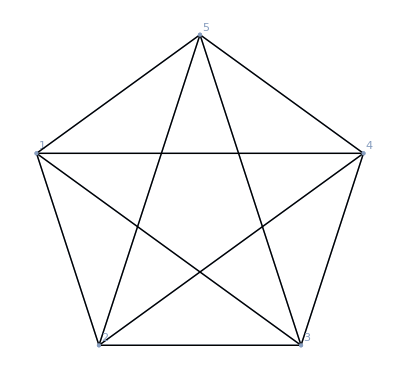

```mathematica
toFramework[CompleteGraph[5],MeshCellLabel->{0->"Index"}]
```

### HennebergOperation[]

```mathematica
Options[HennebergOperation]:={
	WorkingPrecision->MachinePrecision,
	"boundary"->Automatic
};

HennebergOperation::boundary="Option \"boundary\" is not a list of boundary coordinates or a value 2D region from which to select additional vertices.";
HennebergOperation::precision="The requested precision is not a positive real number.";
HennebergOperation::dim="Mechanism must be embedded in 2D for the current version.";
HennebergOperation::type="Second argument is a list of either 1 or 2 specifying which Henneberg moves type should be taken in each step.";
HennebergOperation::mech="Mechanism must be a framework[].";

HennebergOperation[m_framework, listOfMoves : {Alternatives[1,2]..}, OptionsPattern[]]:=With[
{
mUnpacked=m["unpack"],
boundary=Which[
	OptionValue["boundary"]===Automatic,BoundingRegion[m["positions"],"MinDisk"],
	MatrixQ[OptionValue["boundary"],NumericQ]&&Dimensions[OptionValue["boundary"]][[2]]>2, Polygon[OptionValue["boundary"]],
	RegionQ[OptionValue["boundary"]]&&RegionDimension[OptionValue["boundary"]]==2,OptionValue["boundary"],
	True, (Message[HennebergOperation::boundary]; $Failed)
	],
precision=If[NumericQ[OptionValue[WorkingPrecision]]&&OptionValue[WorkingPrecision]>0,OptionValue[WorkingPrecision],Message[HennebergOperation::precision]; $Failed]
},
	Head[m][Fold[HennebergOperationInternal[#1,#2,boundary,precision]&,mUnpacked,listOfMoves]] /; embeddingDimension[m]==2&&boundary=!=$Failed&&precision=!=$Failed
]
HennebergOperation[m_framework?(embeddingDimension[#]!=2&), _,OptionsPattern[]]:="nothing"/;Message[HennebergOperation::dim]
HennebergOperation[m_framework, Except[{Alternatives[1,2]..}],OptionsPattern[]]:="nothing"/;Message[HennebergOperation::type]
HennebergOperation[m_origami, _,OptionsPattern[]]:="nothing"/;Message[HennebergOperation::mech]

HennebergOperationInternal[{coordinates_,displayCells_,componentCells_}, 1,boundary_,precision_]:=
With[
{(*choose a new vertex location*)
	newVertex=SelectFirst[
			RandomVariate[
				UniformDistribution[RegionBounds[boundary]],
				20,
				WorkingPrecision->precision
			],
			RegionMember[boundary]
		],
	(*choose two random vertices*)
	initialVertices=RandomSample[Range[Length[coordinates]],2]
},
	{
		Join[coordinates,{newVertex}],
		Join[displayCells,{
			{Line,{initialVertices[[1]],Length[coordinates]+1},{MeshCellStyle->Black}},
			{Line,{initialVertices[[2]],Length[coordinates]+1},{MeshCellStyle->Black}}
		}],
		Join[componentCells,{
			{rigidBar,{initialVertices[[1]],Length[coordinates]+1},Options[rigidBar]},
			{rigidBar,{initialVertices[[2]],Length[coordinates]+1},Options[rigidBar]}
		}]
	}
]

HennebergOperationInternal[{coordinates_,displayCells_,componentCells_},2, boundary_,precision_]:=
Module[
{
	v,
	edge=RandomChoice[Cases[componentCells,{rigidBar,_,_}]][[2]],
	t=RandomReal[{0,1}]
},
	v=RandomChoice[Complement[Range[Length[coordinates]],edge]];
	{
	(*add vertex somewhere along the chosen edge*)
	Join[coordinates,{ coordinates[[ edge[[1]] ]] + (coordinates[[ edge[[2]] ]] - coordinates[[ edge[[1]] ]]) t  }],

	Join[
		DeleteCases[displayCells,{_,edge|Reverse[edge],_}],
		{
		{Line,{edge[[1]],Length[coordinates]+1},{MeshCellStyle->{Black}}},
		{Line,{Length[coordinates]+1,edge[[2]]},{MeshCellStyle->{Black}}},
		{Line,{Length[coordinates]+1,v},{MeshCellStyle->{Black}}}
		}
	],

	Join[
		DeleteCases[componentCells,{_,edge|Reverse[edge],_}],
		{
		{rigidBar,{edge[[1]],Length[coordinates]+1},Options[rigidBar]},
		{rigidBar,{Length[coordinates]+1,edge[[2]]},Options[rigidBar]},
		{rigidBar,{Length[coordinates]+1,v},Options[rigidBar]}
		}
	]
	}
]
```

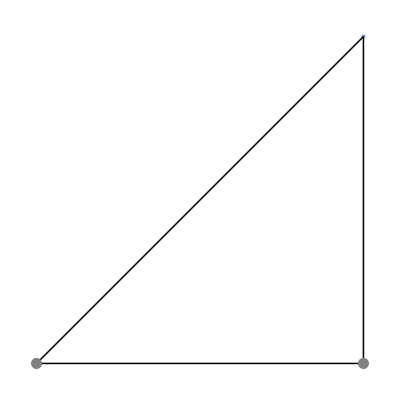

```mathematica
m=framework[{{0,0},{1,0},{1,1}},{rigidBar[{1,2}],rigidBar[{2,3}],rigidBar[{3,1}],joint[1],joint[2]}]
```

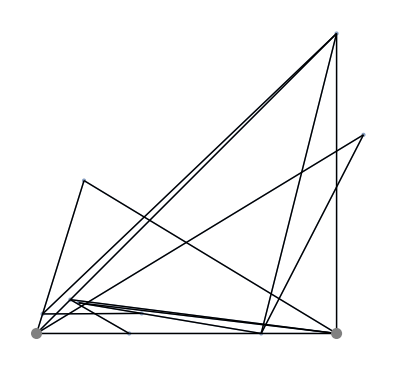

```mathematica
m2=HennebergOperation[m,{1,2,2,1,1,2,2,2}]
```

```mathematica
constraintMatrix[m2]
```

SparseArray[…]

```mathematica
NullSpace[constraintMatrix[m2]]
```

{}

```mathematica
infinitesimalMotions[m2]
```

infinitesimalMotions::failed: Failed to find an appropriate solution. Check the constraints.

{{},{}}

```mathematica
End[];

EndPackage[];
```

## Code structure

### adding new components

To add a new component type, you need to define the following functions:

	cellForm[]
	dataForm[]
	componentData[]
	
	listConstraints[]
	componentConstraint[]
	
	componentEnergy[]

## Examples

```mathematica
?mechanisms`*
```

## creating and modifying mechanisms

### creating structures and specifying properties

To create a framework, use framework[]. To create origami, use origami[].

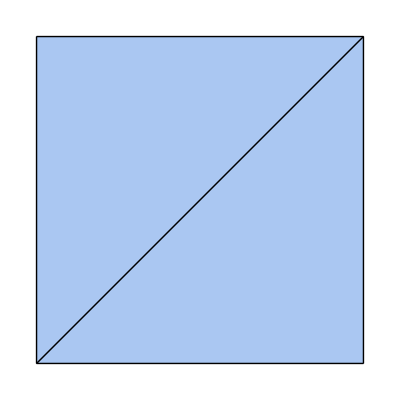

```mathematica
m=origami[{{0,0},{1,0},{1,1},{0,1}},{fold[{1,3}],face[{1,2,3}],face[{3,4,1}]}]
```

Origami is naturally embedded in 3D but displayed in 2D if possible.

```mathematica
embeddingDimension[m]
displayDimension[m]
```

3

2

Use display dimension to change the display dimension to 3D.

```mathematica
displayDimension[m->3]
```

-Graphics3D-

Getting a list of the components that make up the mechanical energy returns a list of the form:
	{component[indices,data],...}

```mathematica
mechanismComponents[m]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},{{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞}}],fold[{{1,3}},{{Automatic,∞}}]}

The data is in the order given by dataForm[].

```mathematica
dataForm[rigidBar]
```

{length,stiffness}

So in the above example, the rigid bar lengths are determined automatically and the bars have infinite stiffness.

To change the data, you can use the same properties.  The properties of a fold are given by

```mathematica
Options[fold]
```

{torsionalStiffness→∞,angle→Automatic}

```mathematica
m=origami[{{0,0},{1,0},{1,1},{0,1}},{Property[fold[{1,3}],{"torsionalStiffness"->1}],face[{1,2,3}],face[{3,4,1}]}]
```

-Graphics-

```mathematica
mechanismComponents[m]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},{{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞}}],fold[{{1,3}},{{Automatic,1}}]}

A fold generates both a fold[] component and a rigidBar[]. We can also manipulate the properties of the rigidBar[] and fold[] independently.

```mathematica
m=origami[{{0,0},{1,0},{1,1},{0,1}},{Property[fold[{1,3}],{"stiffness"->1}],face[{1,2,3}],face[{3,4,1}]}]
```

-Graphics-

```mathematica
mechanismComponents[m]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},{{Automatic,1},{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞}}],fold[{{1,3}},{{Automatic,∞}}]}

In a future version, I may rename the component fold[] to torsionalSpring[].

### mechanismPositions[]

```mathematica
m=origami[{{0,0},{1,0},{1,1},{0,1}},{fold[{1,3}],face[{1,2,3}],face[{3,4,1}]}];
```

Use mechanismPositions[] to get the coordinates.

```mathematica
mechanismPositions[m]
```

{{0,0,0},{1,0,0},{1,1,0},{0,1,0}}

The same function allows you to change the mechanism positions.

```mathematica
mechanismPositions[m->(m["positions"]+randomDisplacements[m])]
```

-Graphics3D-

The function displaceVertices[] returns new positions with one or more vertices displaced.

```mathematica
displaceVertices[m,{2->{0,0,1/2},1->{1/2,0,0}}]
```

{{1/2,0,0},{1,0,1/2},{1,1,0},{0,1,0}}

```mathematica
mechanismPositions[m->displaceVertices[m,{2->{0,0,1/2}}]]
```

-Graphics3D-

### mechanismComponents[]

```mathematica
m=origami[{{0,0},{1,0},{1,1},{0,1}},{Property[fold[{1,3}],{"stiffness"->1}],face[{1,2,3}],face[{3,4,1}]}]
```

-Graphics-

```mathematica
mechanismComponents[m]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},{{Automatic,1},{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞}}],fold[{{1,3}},{{Automatic,∞}}]}

To list only the rigidBar[] we use

```mathematica
mechanismComponents[m,rigidBar[_]]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},{{Automatic,1},{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞}}]}

To list all rigidBars meeting vertex 3,

```mathematica
mechanismComponents[m,rigidBar[{3,_}]]
```

{rigidBar[{{1,3},{2,3},{3,4}},{{Automatic,1},{Automatic,∞},{Automatic,∞}}]}

Notice how the order does not matter. To list all components meeting vertex 3,

```mathematica
mechanismComponents[m,_[{3,_}]]
```

{rigidBar[{{1,3},{2,3},{3,4}},{{Automatic,1},{Automatic,∞},{Automatic,∞}}],fold[{{1,3}},{{Automatic,∞}}]}

If we want the torsional stiffness of the fold to become Infinity again, we can use the same function’s 3rd argument.

```mathematica
mechanismComponents[
mechanismComponents[m,fold[_],{"torsionalStiffness"->Infinity}]
]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},{{Automatic,1},{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞}}],fold[{{1,3}},{{Automatic,∞}}]}

The new property will be changed on every component matching the pattern for which it is valid. We can also use multiple patterns:

```mathematica
mechanismComponents[
mechanismComponents[m,rigidBar[{1,3}]|fold[_],{"length"->Infinity}]
]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},{{∞,1},{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞}}],fold[{{1,3}},{{Automatic,∞}}]}

### modifyMechanism[]

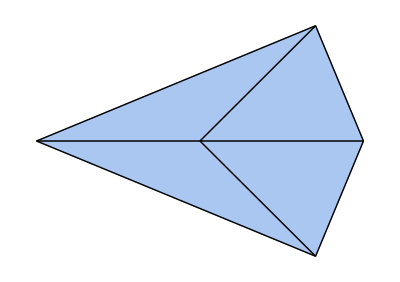

```mathematica
m=singleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}]
```

You can use some MeshRegion options.

```mathematica
modifyMechanism["Methods"]
```

{MeshCellLabel,MeshCellStyle,add,addComponent,style,label,shape}

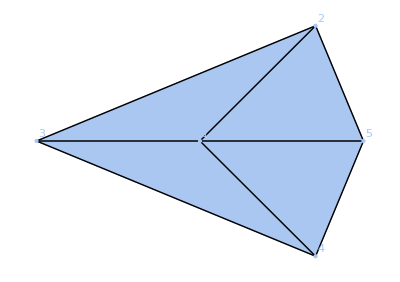

```mathematica
modifyMechanism[m,MeshCellLabel->{0->"Index"}]
```

Let’s get a random configuration.

```mathematica
{en,pos}=minimizeEnergy[m,mechanismEnergy[m],"initial"->(m["positions"]+randomDisplacements[m])]
```

minimizeEnergy::badinitial: Initial conditions are not well-formed numeric positions matching the mechanism.

{1.42238×10^-20,{{0.339663,0.00147679,-0.0369789},{1.03679,0.717898,-0.0644348},{-0.659926,-0.0118796,-0.0115992},{1.05584,-0.696116,-0.0582549},{1.33863,0.0147455,-0.0805106}}}

We can label the folds with their fold angles

```mathematica
Thread[Line[interiorEdges[m]]->foldAngle[m,pos,interiorEdges[m]]]
```

{Line[{{1,2},{3,1},{4,1},{5,1}}]→-0.0256868,Line[{{1,2},{3,1},{4,1},{5,1}}]→-0.0181638,Line[{{1,2},{3,1},{4,1},{5,1}}]→-0.0256868,Line[{{1,2},{3,1},{4,1},{5,1}}]→0.0181638}

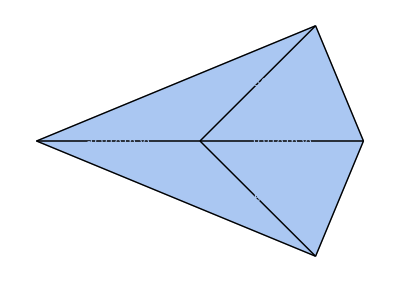

```mathematica
modifyMechanism[m,MeshCellLabel->Thread[(Line/@interiorEdges[m])->foldAngle[m,pos,interiorEdges[m]]]]
```

or color code the folds according to whether they are mountains or valleys

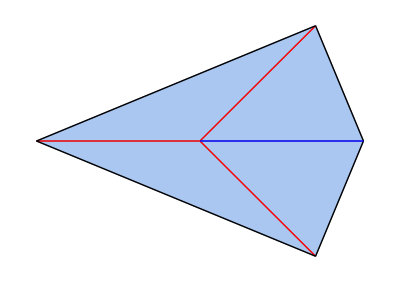

```mathematica
modifyMechanism[m,MeshCellStyle->Thread[(Line/@interiorEdges[m])->(If[#>0,Blue,Red]&/@foldAngle[m,pos,interiorEdges[m]])]]
```

You can also just color one edge, vertex or face

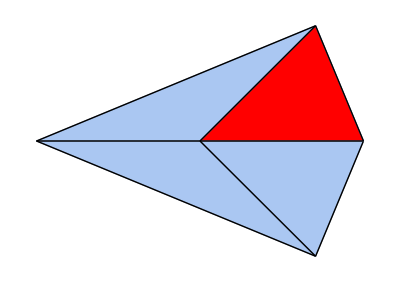

```mathematica
modifyMechanism[m,MeshCellStyle->Polygon[{1,5,2}]->{Red}]
```

Finally, we can add a mechanical component (but not a new display element) with “add”.

```mathematica
m2=modifyMechanism[m,"addComponent"->{fold[{1,2}]}]
```

-Graphics-

### randomOrigami[]

```mathematica
?randomOrigami
```

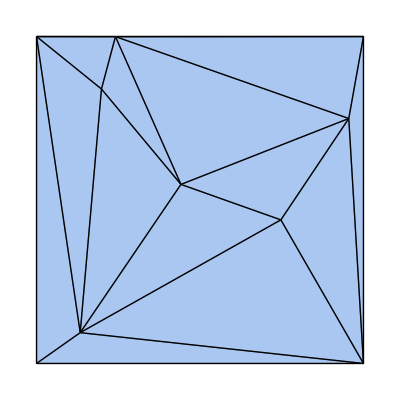

```mathematica
m=randomOrigami[6]
```

```mathematica
MeshCellCount[m,0]-4
```

6

#### Options

“boundary”

You can specify the location of the points on the boundary.

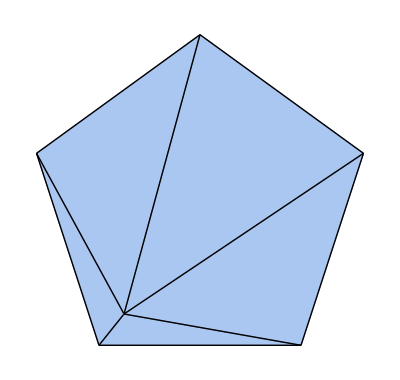

```mathematica
randomOrigami[1,"boundary"->CirclePoints[5]]
```

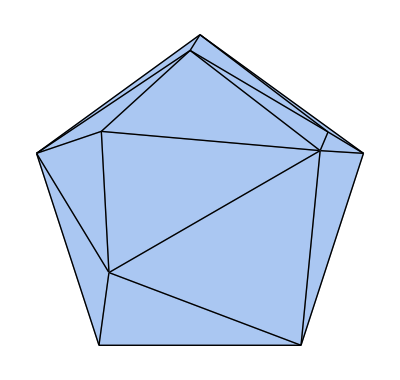

```mathematica
m=randomOrigami[5,"boundary"->CirclePoints[5]]
```

```mathematica
MeshCellCount[m,0]-5
```

5

### singleVertex[]

```mathematica
?singleVertex
```

```mathematica
singleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}]
```

-Graphics-

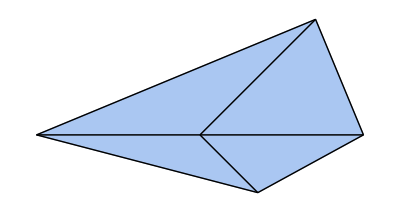

```mathematica
singleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4},{1,1,1/2,1}]
```

## Isometric deformations

```mathematica
m=modifyMechanism[
singleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4},MeshCellLabel->{0->"Index"}],
"addComponent"->{
(*eliminate Euclidean motions*)
joint[1],
Property[joint[3],{"components"->{"y","z"}}],
Property[joint[4],{"components"->"z"}],
fold[{1,5}]
}
]
```

-Graphics-

```mathematica
?infinitesimalMotions
```

```mathematica
Simplify@infinitesimalMotions[m]
```

{{{0,0,0},{0,0,√(2/3) $11[1]},{0,0,0},{0,0,0},{0,0,($11[1])/(√3)}},{-($11[1])^2/(6 √3)}}

The constraint matrix includes all constraints in the system, including the fixed joints.

```mathematica
MatrixForm[constraintMatrix[m]]
```

(-√2 | -√2 | 0 | √2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0
-2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | -2 (-1-1/(√2)) | √2 | 0 | 2 (-1-1/(√2)) | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2 (1+1/(√2)) | √2 | 0 | 2 (1+1/(√2)) | -√2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 (1-1/(√2)) | -√2 | 0 | 2 (1-1/(√2)) | √2 | 0
0 | 0 | 0 | 2 (-1+1/(√2)) | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 (-1+1/(√2)) | -√2 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 2-2 √2 | 0 | 0 | √2 | 0 | 0 | 0 | 0 | 0 | √2 | 0 | 0 | -2)

The compatibility matrix includes only the length constraints in the system.

```mathematica
MatrixForm[compatibilityMatrix[m]]
```

(-√2 | -√2 | 0 | √2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0
-2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | -2 (-1-1/(√2)) | √2 | 0 | 2 (-1-1/(√2)) | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2 (1+1/(√2)) | √2 | 0 | 2 (1+1/(√2)) | -√2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 (1-1/(√2)) | -√2 | 0 | 2 (1-1/(√2)) | √2 | 0
0 | 0 | 0 | 2 (-1+1/(√2)) | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 (-1+1/(√2)) | -√2 | 0)

The self-stresses returns a list of rules assigning stresses to edges that are associated with the self-stresses of the compatibility matrix. In other words, it uses only the rigidBar[] components.

```mathematica
ss=selfStresses[m]
```

{{rigidBar[{{1,2},{1,3},{1,4},{1,5},{2,3},{3,4},{4,5},{5,2}},{{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞},{Automatic,∞}}]}→{-2,-2-√2,-2,-2+√2,1,1,1,1}}

## Configurations and trajectories through configuration space

### Positions and displacements

There is no object for vertexDisplacements or vertexPositions. There is still vertexPosition[] and vertexDisplacement[] for single displacements and positions.

To generate a larger list, you can use a construction like

```mathematica
vertexPosition[{1,2,3},{"x","y"}]
```

{{vertexPosition[1,x],vertexPosition[1,y]},{vertexPosition[2,x],vertexPosition[2,y]},{vertexPosition[3,x],vertexPosition[3,y]}}

You can also refer to All[2] or All[3] for all the components in 2D and 3D

```mathematica
vertexDisplacement[{1,2,3},All[3]]
```

{{vertexDisplacement[1,x],vertexDisplacement[1,y],vertexDisplacement[1,z]},{vertexDisplacement[2,x],vertexDisplacement[2,y],vertexDisplacement[2,z]},{vertexDisplacement[3,x],vertexDisplacement[3,y],vertexDisplacement[3,z]}}

Finally, if you have a mechanism, you can use

```mathematica
vertexPosition[randomOrigami[1]]
```

{{vertexPosition[1,x],vertexPosition[1,y],vertexPosition[1,z]},{vertexPosition[2,x],vertexPosition[2,y],vertexPosition[2,z]},{vertexPosition[3,x],vertexPosition[3,y],vertexPosition[3,z]},{vertexPosition[4,x],vertexPosition[4,y],vertexPosition[4,z]},{vertexPosition[5,x],vertexPosition[5,y],vertexPosition[5,z]}}

You can over-ride the embedding dimension with

```mathematica
vertexDisplacement[randomOrigami[1],All[2]]
```

{{vertexDisplacement[1,x],vertexDisplacement[1,y]},{vertexDisplacement[2,x],vertexDisplacement[2,y]},{vertexDisplacement[3,x],vertexDisplacement[3,y]},{vertexDisplacement[4,x],vertexDisplacement[4,y]},{vertexDisplacement[5,x],vertexDisplacement[5,y]}}

### 4-bar linkage

To define a linkage, we can use framework[].

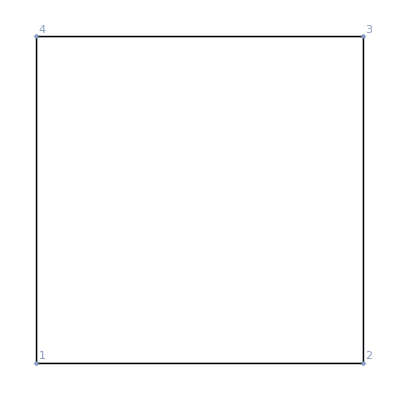

```mathematica
fourBarLinkage=framework[{{0,0},{1,0},{1,1},{0,1}},
{
rigidBar/@Partition[{1,2,3,4},2,1,1],
joint[1],Property[joint[2],"components"->"y"]
},
MeshCellLabel->{0->"Index"}
]
```

We used to use fixedJoint[] to fix a joint. Now we just use joint[]. Any joint has the properties given by

```mathematica
Options[joint]
```

{stiffness→∞,position→Automatic,components→All}

The infinitesimal motions from the above configuration are given by infinitesimalMotions[].

```mathematica
?infinitesimalMotions
```

```mathematica
infinitesimalMotions[fourBarLinkage,"variables"->c]
```

{{{0,0},{0,0},{c[1]/(√2),0},{c[1]/(√2),0}},{}}

As before, the first element is a list of displacements for the linear isometries. The second element is a set of quadratic constraints, if there are any. For a four-bar linkage, there are not. Therefore, we get an initial direction for a motion from this

```mathematica
direction=D[infinitesimalMotions[fourBarLinkage,"variables"->c][[1]],c[1]]
```

{{0,0},{0,0},{1/(√2),0},{1/(√2),0}}

The function isometricTrajectory[] gives us a list of positions starting along a specific direction and maintaining as close to straight trajectory as possible. For example, we can take 10 steps.

```mathematica
isometricTrajectory[fourBarLinkage,direction,10]
```

{{{0,0},{1,0},{1,1},{0,1}},{{0,0},{1.,0},{1.07053,0.997509},{0.0705346,0.997509}},{{-4.90069×10^-18,-5.00423×10^-18},{1.,-5.39859×10^-18},{1.14072,0.99005},{0.140718,0.99005}},{{-1.36319×10^-18,-2.53973×10^-18},{1.,-1.7789×10^-17},{1.2102,0.977658},{0.2102,0.977658}},{{-1.23197×10^-17,-5.20649×10^-19},{1.,-6.84429×10^-18},{1.27864,0.960397},{0.278635,0.960397}},{{-1.56166×10^-17,1.51385×10^-18},{1.,4.69968×10^-18},{1.34568,0.938352},{0.345682,0.938352}},{{-1.92184×10^-17,-5.23214×10^-19},{1.,2.39056×10^-17},{1.41101,0.911632},{0.411008,0.911632}},{{-2.60658×10^-17,-6.6216×10^-18},{1.,1.67943×10^-18},{1.47429,0.880371},{0.474286,0.880371}},{{-1.56942×10^-17,1.15934×10^-17},{1.,-1.74825×10^-17},{1.5352,0.844725},{0.535201,0.844725}},{{-4.00721×10^-18,-1.05296×10^-17},{1.,-1.8934×10^-17},{1.59345,0.804871},{0.59345,0.804871}},{{-2.73605×10^-18,5.42998×10^-18},{1.,-1.12719×10^-17},{1.64874,0.761007},{0.648743,0.761007}}}

Notice that each set of positions is just a list of 2d coordinates. There is no more wrapper around positions or displacements.

Here is how you would obtain an animation of the four bar linkage along this trajectory using plotMechanism[].

```mathematica
ListAnimate[
plotMechanism[fourBarLinkage,isometricTrajectory[fourBarLinkage,direction,30]]
]
```

### degree four vertex

For origami, we might use origami[] to create an origami mechanism. This uses the same arguments as framework[]. Alternatively,

```mathematica
m=singleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4},MeshCellLabel->{0->"Index"}]
```

-Graphics-

creates a single vertex with sector angles given in the arguments.

In this case, the infinitesimal motions involve quadratic constraints.

```mathematica
motions=Simplify[infinitesimalMotions[m,
"variables"->{vertexDisplacement[5,"z"],vertexDisplacement[4,"z"]},
"constraints"->{
vertexDisplacement[1,All[3]],
vertexDisplacement[2,{"y","z"}],
vertexDisplacement[3,"z"]}
]]
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,vertexDisplacement[4,z]},{0,0,vertexDisplacement[5,z]}},{(vertexDisplacement[5,z] (-√2 vertexDisplacement[4,z]+vertexDisplacement[5,z]))/(2 √3)}}

Notice we use the “constraints” option to fix the positions of one of the faces of the origami. This eliminates any issues from rigid rotations.

We can obtain two initial trajectories as

```mathematica
dir1=D[motions[[1]]/.First@Solve[motions[[2]]==0,vertexDisplacement[5,"z"]],vertexDisplacement[4,"z"]]
dir2=D[motions[[1]]/.Last@Solve[motions[[2]]==0,vertexDisplacement[5,"z"]],vertexDisplacement[4,"z"]]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,0,√2}}

We can obtain a set of two trajectories for each direction now.  Notice that we continue to use the constraints.

```mathematica
trajectory1=isometricTrajectory[m,dir1,30,"constraints"->{vertexDisplacement[1,All[3]],vertexDisplacement[2,{"y","z"}],vertexDisplacement[3,"z"]}];
trajectory2=isometricTrajectory[m,dir2,30,"constraints"->{vertexDisplacement[1,All[3]],vertexDisplacement[2,{"y","z"}],vertexDisplacement[3,"z"]}];
```

A new function, findMinimalTrajectory[] attempts to use the elastic band method to find the shortest way from one point to another in the configuration space. Here we have to include an additional term in the energy to maintain the same constraints.

```mathematica
test=findMinimalTrajectory[m,Last[trajectory1],Last[trajectory2],40,"energy"->(#.#&[Flatten[(vertexPosition[m]-m["positions"])[[{1,2,3}]]]]),
"minimizationOptions"->{MaxIterations->10^5},
Method->{"ElasticBand","stiffness"->10^(-3)}
];
```

The energies of the configurations found are

```mathematica
(mechanismEnergy[m]/.dataRules[vertexPosition,#])&/@test
```

{1.40898×10^-20,1.55058×10^-11,1.61285×10^-11,1.6064×10^-11,1.60955×10^-11,1.60556×10^-11,1.60694×10^-11,1.60946×10^-11,1.61505×10^-11,1.61431×10^-11,1.62323×10^-11,1.62627×10^-11,1.63613×10^-11,1.64687×10^-11,1.65479×10^-11,1.66927×10^-11,1.68072×10^-11,1.69398×10^-11,1.71415×10^-11,1.7243×10^-11,1.74243×10^-11,1.75647×10^-11,1.77269×10^-11,1.79922×10^-11,1.81865×10^-11,1.82614×10^-11,1.84995×10^-11,1.83285×10^-11,1.272×10^-11,1.40783×10^-10,5.94732×10^-8,9.61241×10^-6,7.47629×10^-7,1.22133×10^-8,1.7356×10^-8,2.14599×10^-8,2.64611×10^-8,3.22114×10^-8,3.84014×10^-8,4.4726×10^-8,3.50771×10^-8,2.26285×10^-20}

```mathematica
ListAnimate[plotMechanism[m,test]]
```

This method has a clear issue as we approach the bifurcation, however. You can see some weirdness in the trajectory.

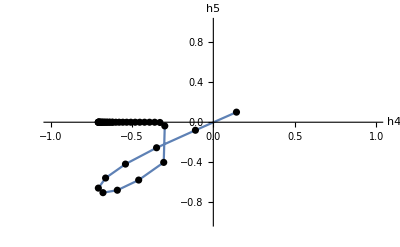

```mathematica
Show[
ListPlot[test[[All,{4,5},3]],Joined->True,PlotRange->{{-1,1},{-1,1}},AxesLabel->{"h4","h5"}],
ListPlot[test[[All,{4,5},3]],Joined->False,PlotRange->{{-1,1},{-1,1}},AxesLabel->{"h4","h5"},PlotStyle->Black]
]
```

### mapping out trajectories

Here is a 1 degree of freedom origami structure with one vertex

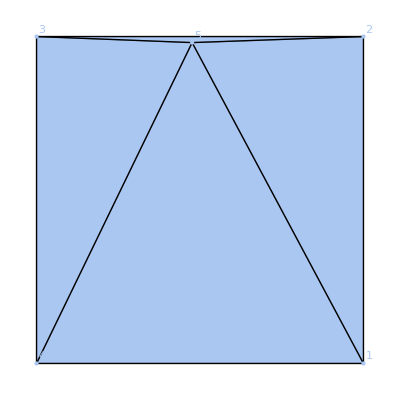

```mathematica
m=randomOrigami[1,MeshCellLabel->{0->"Index"}]
```

```mathematica
constraints={vertexDisplacement[5,All[3]],vertexDisplacement[1,{"y","z"}],vertexDisplacement[2,"z"]};
```

We first acquire two different directions along the configuration space.

```mathematica
Chop[infinitesimalMotions[m,"constraints"->constraints]]
```

{{{0,0,0},{0,0,0},{0,0,-1. $14[1]},{0,0,1. $14[2]},{0,0,0}},{-0.352831 ($14[1])^2+0.02586 $14[1] $14[2]+0.00602621 ($14[2])^2}}

```mathematica
dir=D[vertexDisplacement[m]/.Solve[Chop[Simplify[infinitesimalMotions[m,"constraints"->constraints,"variables"->vertexDisplacement[{3,4},"z"]][[2]]]]==0,vertexDisplacement[{3,4},"z"]],vertexDisplacement[3,"z"]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{{0,0,0},{0,0,0},{0,0,1},{0,0,-5.80127},{0,0,0}},{{0,0,0},{0,0,0},{0,0,1},{0,0,10.0925},{0,0,0}}}

Now we compute the height of the 4th and 5th vertex by following the trajectory as we proceed.

```mathematica
trajectory1=isometricTrajectory[m,dir[[1]],200,"stepsize"->0.1,"constraints"->constraints][[All,3;;4,3]];
trajectory2=isometricTrajectory[m,dir[[2]],200,"stepsize"->0.1,"constraints"->constraints][[All,3;;4,3]];
```

```mathematica
ListAnimate[Table[Show[
ListPlot[trajectory1[[1;;i]],Joined->True,PlotStyle->{Black,Opacity[0.5]},PlotRange->{{-2,2},{-2,2}}],
Graphics[{Blue,PointSize[0.025],Point[trajectory1[[i]]]}],
ListPlot[trajectory2[[1;;i]],Joined->True,PlotStyle->{Red,Opacity[0.5]},PlotRange->{{-2,2},{-2,2}}],
Graphics[{Blue,PointSize[0.025],Point[trajectory2[[i]]]}],
Axes->True,AxesLabel->{"h3","h4"}
],
{i,1,Length[trajectory1]}
]]
```

## dynamical systems

This is very experimental.

```mathematica
?dynamicalSystem
```

```mathematica
?dynamicalSystemEquations
```

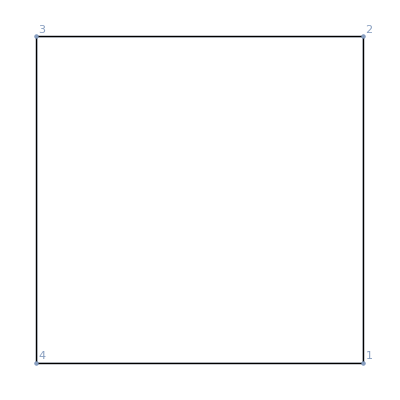

```mathematica
m=polygonalLinkage[CirclePoints[4],MeshCellLabel->{0->"Index"}]
```

```mathematica
eq=dynamicalSystem[m,{m["positions"],{{0,0},{1,0},{0,0},{-1,0}}},{t,0,1},"drag"->0.1]
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

```mathematica
eq/.t->0.4
```

{{0.623133,-0.70176},{1.01348,0.70176},{-0.623133,0.70176},{-1.01348,-0.70176}}

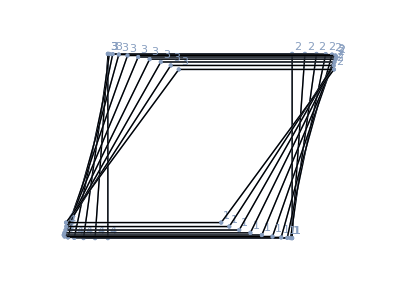

```mathematica
Show[plotMechanism[m,eq/.t->#&/@Range[0,1,0.1]]]
```

```mathematica
dynamicalSystemEquations[m,{v,t},"drag"->0.1]
```

{0.-2 (-v[1,x][t]+v[2,x][t]) (-2+(-v[1,x][t]+v[2,x][t])^2+(-v[1,y][t]+v[2,y][t])^2)+2 (v[1,x][t]-v[4,x][t]) (-2+(v[1,x][t]-v[4,x][t])^2+(v[1,y][t]-v[4,y][t])^2)+0.1 v[1,x]'[t]+v[1,x]''[t],0.-2 (-v[1,y][t]+v[2,y][t]) (-2+(-v[1,x][t]+v[2,x][t])^2+(-v[1,y][t]+v[2,y][t])^2)+2 (-2+(v[1,x][t]-v[4,x][t])^2+(v[1,y][t]-v[4,y][t])^2) (v[1,y][t]-v[4,y][t])+0.1 v[1,y]'[t]+v[1,y]''[t],0.+2 (-v[1,x][t]+v[2,x][t]) (-2+(-v[1,x][t]+v[2,x][t])^2+(-v[1,y][t]+v[2,y][t])^2)-2 (-v[2,x][t]+v[3,x][t]) (-2+(-v[2,x][t]+v[3,x][t])^2+(-v[2,y][t]+v[3,y][t])^2)+0.1 v[2,x]'[t]+v[2,x]''[t],0.+2 (-v[1,y][t]+v[2,y][t]) (-2+(-v[1,x][t]+v[2,x][t])^2+(-v[1,y][t]+v[2,y][t])^2)-2 (-v[2,y][t]+v[3,y][t]) (-2+(-v[2,x][t]+v[3,x][t])^2+(-v[2,y][t]+v[3,y][t])^2)+0.1 v[2,y]'[t]+v[2,y]''[t],0.+2 (-v[2,x][t]+v[3,x][t]) (-2+(-v[2,x][t]+v[3,x][t])^2+(-v[2,y][t]+v[3,y][t])^2)-2 (-v[3,x][t]+v[4,x][t]) (-2+(-v[3,x][t]+v[4,x][t])^2+(-v[3,y][t]+v[4,y][t])^2)+0.1 v[3,x]'[t]+v[3,x]''[t],0.+2 (-v[2,y][t]+v[3,y][t]) (-2+(-v[2,x][t]+v[3,x][t])^2+(-v[2,y][t]+v[3,y][t])^2)-2 (-v[3,y][t]+v[4,y][t]) (-2+(-v[3,x][t]+v[4,x][t])^2+(-v[3,y][t]+v[4,y][t])^2)+0.1 v[3,y]'[t]+v[3,y]''[t],0.-2 (v[1,x][t]-v[4,x][t]) (-2+(v[1,x][t]-v[4,x][t])^2+(v[1,y][t]-v[4,y][t])^2)+2 (-v[3,x][t]+v[4,x][t]) (-2+(-v[3,x][t]+v[4,x][t])^2+(-v[3,y][t]+v[4,y][t])^2)+0.1 v[4,x]'[t]+v[4,x]''[t],0.-2 (-2+(v[1,x][t]-v[4,x][t])^2+(v[1,y][t]-v[4,y][t])^2) (v[1,y][t]-v[4,y][t])+2 (-v[3,y][t]+v[4,y][t]) (-2+(-v[3,x][t]+v[4,x][t])^2+(-v[3,y][t]+v[4,y][t])^2)+0.1 v[4,y]'[t]+v[4,y]''[t]}

A pendulum

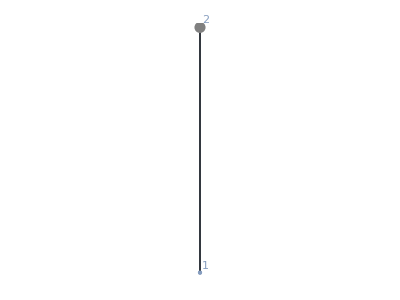

```mathematica
m=framework[{{0,0},{0,1}},{joint[2],rigidBar[{1,2}]}];
modifyMechanism[m,MeshCellLabel->{0->"Index"}]
```

Even though vertex 2 is pinned, we still have to provide initial conditions for it. These are ignored by the code.

```mathematica
out=dynamicalSystem[m,{m["positions"],{{10^(-3),0},{0,0}}},{t,0,10^4}]
```

{{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]},{0,1}}

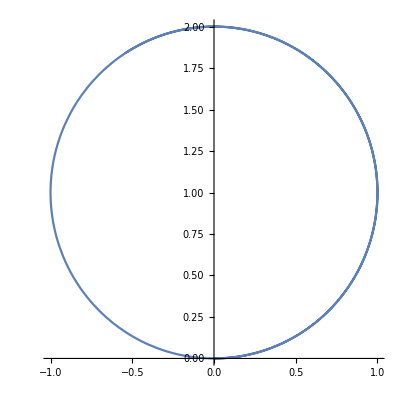

```mathematica
Show[
ParametricPlot[out[[1]]/.t->tt,{tt,0,10^4}],
ParametricPlot[out[[2]]/.t->tt,{tt,0,10^4}]
]
```

A pendulum with a small amount of gravity

```mathematica
out=dynamicalSystem[m,{m["positions"],{{10^(-2),0},{0,0}}},{t,0,10^4},"additional"->10^(-4)vertexPosition[1,"y"]]
```

{{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]},{0,1}}

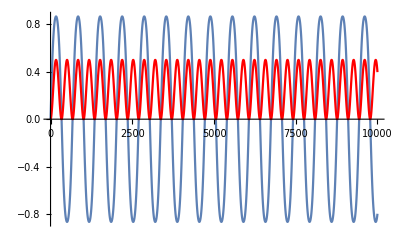

```mathematica
Show[
Plot[out[[1,1]]/.t->tt,{tt,0,10^4}],
Plot[out[[1,2]]/.t->tt,{tt,0,10^4},PlotStyle->Red]
]
```

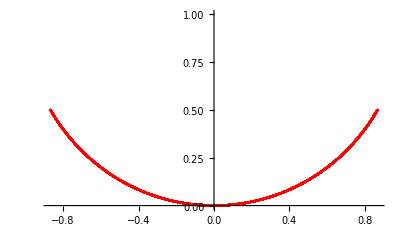

```mathematica
Show[
ParametricPlot[out[[1]]/.t->tt,{tt,0,10^4},PlotStyle->Red],
ParametricPlot[out[[2]]/.t->tt,{tt,0,10^4}],

PlotRange->All
]
```

If we give the joint an actual stiffness then we get something slightly different.

```mathematica
m=framework[{{0,0},{0,1}},{Property[joint[2],"stiffness"->10],rigidBar[{1,2}]}];
modifyMechanism[m,MeshCellLabel->{0->"Index"}]
```

-Graphics-

Though the solution is essentially the same, vertex 2  is treated as being pinned by a spring and we now get a numerical solution to the position of vertex 2.

```mathematica
out=dynamicalSystem[m,{m["positions"],{{10^(-3),0},{0,0}}},{t,0,10^4}]
```

{{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]},{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]}}

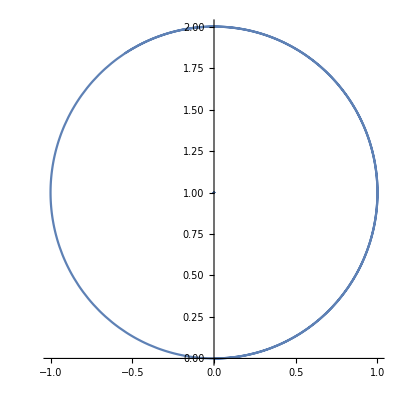

```mathematica
Show[
ParametricPlot[out[[1]]/.t->tt,{tt,0,10^4}],
ParametricPlot[out[[2]]/.t->tt,{tt,0,10^4}]
]
```

A pendulum with a small amount of gravity

```mathematica
out=dynamicalSystem[m,{m["positions"],{{10^(-2),0},{0,0}}},{t,0,10^4},"additional"->10^(-4)vertexPosition[1,"y"]]
```

{{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]},{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]}}

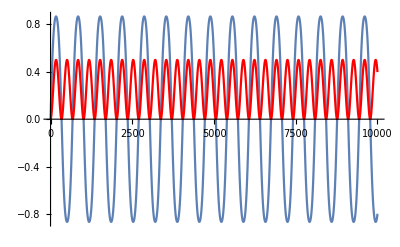

```mathematica
Show[
Plot[out[[1,1]]/.t->tt,{tt,0,10^4}],
Plot[out[[1,2]]/.t->tt,{tt,0,10^4},PlotStyle->Red]
]
```

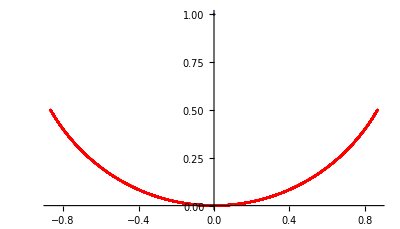

```mathematica
Show[
ParametricPlot[out[[1]]/.t->tt,{tt,0,10^4},PlotStyle->Red],
ParametricPlot[out[[2]]/.t->tt,{tt,0,10^4}],

PlotRange->All
]
```

## periodic mechanisms

### frameworks

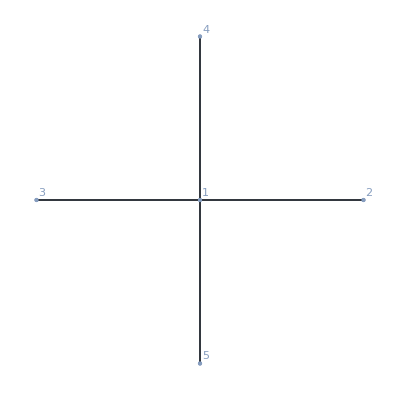

```mathematica
m=framework[{{0,0},{1,0},{-1,0},{0,1},{0,-1}},{
rigidBar[{1,#}]&/@Range[2,5]
},
MeshCellLabel->{0->"Index"}
]
```

```mathematica
pd=periodicData[5,{f1,f2},{1,f1[1],Inverse[f1[1]],f2[1],Inverse[f2[1]]}]
```

periodicData[{f1,f2}]

```mathematica
periodicEquivalenceClasses[m,pd,listEdges[m]]
```

{{{1,2},{3,1}},{{1,4}},{{1,5}}}

```mathematica
listEdges[m]
```

{{1,2},{1,3},{1,4},{1,5}}

```mathematica
constraintEquations[m,1][[{1,3}]]
```

{2 (-vertexDisplacement[1,x]+vertexDisplacement[2,x]),2 (-vertexDisplacement[1,y]+vertexDisplacement[4,y])}

```mathematica
rules=Flatten[Thread/@{
vertexDisplacement[2,All[2]]->zx vertexDisplacement[1,All[2]],
vertexDisplacement[3,All[2]]->zx^(-1) vertexDisplacement[1,All[2]],
vertexDisplacement[4,All[2]]->zy vertexDisplacement[1,All[2]],
vertexDisplacement[5,All[2]]->zy^(-1) vertexDisplacement[1,All[2]]
}];
```

```mathematica
MatrixForm[CoefficientArrays[constraintEquations[m,1][[{1,3}]]/.rules,vertexDisplacement[1,All[2]]][[2]]]
```

(-2+2 zx | 0
0 | -2+2 zy)

```mathematica
mat=CoefficientArrays[Join[constraintEquations[m,1],relations],Flatten[vertexDisplacement[m]]][[2]]
```

SparseArray[…]

```mathematica
GroebnerBasis[Join[constraintEquations[m,1],relations],Flatten[vertexDisplacement[m]]]
```

{vertexDisplacement[4,z]-zy^2 vertexDisplacement[5,z],zx vertexDisplacement[3,z]-zy vertexDisplacement[5,z],vertexDisplacement[2,z]-zx zy vertexDisplacement[5,z],vertexDisplacement[1,z]-zy vertexDisplacement[5,z],-vertexDisplacement[3,z]/zy+vertexDisplacement[5,z]/zx,-vertexDisplacement[5,y]+zy vertexDisplacement[5,y],-vertexDisplacement[5,y]+vertexDisplacement[5,y]/zy,vertexDisplacement[3,z] vertexDisplacement[5,x]-zy vertexDisplacement[5,x] vertexDisplacement[5,z],-vertexDisplacement[5,x]+zx vertexDisplacement[5,x],-vertexDisplacement[5,x]+vertexDisplacement[5,x]/zx,vertexDisplacement[4,y]-vertexDisplacement[5,y],vertexDisplacement[4,x]-zy^2 vertexDisplacement[5,x],vertexDisplacement[3,y]-vertexDisplacement[5,y]/zx,vertexDisplacement[3,x]-zy vertexDisplacement[5,x],vertexDisplacement[2,y]-zx vertexDisplacement[5,y],vertexDisplacement[2,x]-zy vertexDisplacement[5,x],vertexDisplacement[1,y]-vertexDisplacement[5,y],vertexDisplacement[1,x]-zy vertexDisplacement[5,x]}

### origami

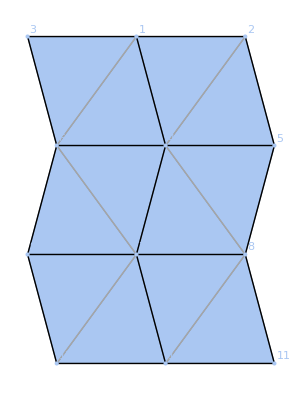

```mathematica
m=miuraOri[Pi/3+Pi/12,MeshCellLabel->{0->"Index"},"Triangulated"->True]
```

```mathematica
compare=vertexDisplacement[2,All[3]]-vertexDisplacement[3,All[3]];
constraintsx={
vertexDisplacement[5,All[3]]-vertexDisplacement[6,All[3]]-compare,
vertexDisplacement[8,All[3]]-vertexDisplacement[9,All[3]]-compare,
vertexDisplacement[11,All[3]]-vertexDisplacement[12,All[3]]-compare
};
compare=vertexDisplacement[3,All[3]]-vertexDisplacement[9,All[3]];
constraintsy={
vertexDisplacement[1,All[3]]-vertexDisplacement[7,All[3]]-compare,
vertexDisplacement[2,All[3]]-vertexDisplacement[8,All[3]]-compare,
vertexDisplacement[6,All[3]]-vertexDisplacement[12,All[3]]-compare,
vertexDisplacement[4,All[3]]-vertexDisplacement[10,All[3]]-compare,
vertexDisplacement[5,All[3]]-vertexDisplacement[11,All[3]]-compare,
};
constraints=Flatten[{constraintsx,constraintsy,{vertexDisplacement[1,All[3]],vertexDisplacement[2,{"y","z"}],vertexDisplacement[3,"z"]}}];
```

```mathematica
{lin,quad}=Chop[infinitesimalMotions[N[m],"constraints"->constraints,"variables"->h]];
```

```mathematica
Length[lin]
```

12

```mathematica
grquad=GroebnerBasis[quad,h/@Range[9]];
```

```mathematica
Length[grquad]
```

2

```mathematica
Variables[lin]
```

{h[1],h[2],h[3]}

```mathematica
lin/.NSolve[Join[grquad,{(h/@Range[3]) . (h/@Range[3])-1} ]==0,h/@Range[3]]
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,-0.154303},{0,0,-0.154303},{0,0,-0.154303},{0,0,-0.308607},{0,0,-0.308607},{0,0,-0.308607},{0,0,-0.46291},{0,0,-0.46291},{0,0,-0.46291}},{{0,0,0},{0,0,0},{0,0,0},{0,0,-0.154303},{0,0,-0.154303},{0,0,-0.154303},{0,0,-0.308607},{0,0,-0.308607},{0,0,-0.308607},{0,0,-0.46291},{0,0,-0.46291},{0,0,-0.46291}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0.154303},{0,0,0.154303},{0,0,0.154303},{0,0,0.308607},{0,0,0.308607},{0,0,0.308607},{0,0,0.46291},{0,0,0.46291},{0,0,0.46291}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0.154303},{0,0,0.154303},{0,0,0.154303},{0,0,0.308607},{0,0,0.308607},{0,0,0.308607},{0,0,0.46291},{0,0,0.46291},{0,0,0.46291}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0.208473},{0,0,0.208473},{0,0,0.208473},{0,0,0.26192},{0,0,0.26192},{0,0,0.26192},{0,0,0.470393},{0,0,0.470393},{0,0,0.470393}},{{0,0,0},{0,0,0},{0,0,0},{0,0,-0.208473},{0,0,-0.208473},{0,0,-0.208473},{0,0,-0.26192},{0,0,-0.26192},{0,0,-0.26192},{0,0,-0.470393},{0,0,-0.470393},{0,0,-0.470393}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0.451425},{0,0,0.451425},{0,0,0.451425},{0,0,-0.108118},{0,0,-0.108118},{0,0,-0.108118},{0,0,0.343307},{0,0,0.343307},{0,0,0.343307}},{{0,0,0},{0,0,0},{0,0,0},{0,0,-0.451425},{0,0,-0.451425},{0,0,-0.451425},{0,0,0.108118},{0,0,0.108118},{0,0,0.108118},{0,0,-0.343307},{0,0,-0.343307},{0,0,-0.343307}}}

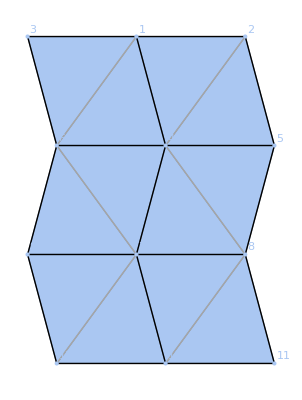

```mathematica
m
```

```mathematica
pd=identificationRules[m,{f1,#+{1,0,0}&},{f2,#+{0,1,0}&}]
```

periodicData[{f1,f2}]

```mathematica
pd["data"]
```

{f2[7],f1[f2[9]],f2[9],f2[10],f1[f2[12]],f2[12],7,f1[9],9,10,f1[12],12}

```mathematica
periodicEquivalenceClasses[m,pd,listVertices[m]]
```

{{1,7},{2,3,8,9},{4,10},{5,6,11,12}}

```mathematica
candidateConstraints=#[[1]]-#[[2]]&/@periodicityRules[m,pd,{vertexDisplacement[#,All[3]]&,vertexDisplacement[#,All[3]]&},{ zx#&,zy#&}]
```

{{vertexDisplacement[1,x]-zy vertexDisplacement[7,x],vertexDisplacement[1,y]-zy vertexDisplacement[7,y],vertexDisplacement[1,z]-zy vertexDisplacement[7,z]},{vertexDisplacement[2,x]-zx zy vertexDisplacement[9,x],vertexDisplacement[2,y]-zx zy vertexDisplacement[9,y],vertexDisplacement[2,z]-zx zy vertexDisplacement[9,z]},{vertexDisplacement[3,x]-zy vertexDisplacement[9,x],vertexDisplacement[3,y]-zy vertexDisplacement[9,y],vertexDisplacement[3,z]-zy vertexDisplacement[9,z]},{vertexDisplacement[4,x]-zy vertexDisplacement[10,x],vertexDisplacement[4,y]-zy vertexDisplacement[10,y],vertexDisplacement[4,z]-zy vertexDisplacement[10,z]},{vertexDisplacement[5,x]-zx zy vertexDisplacement[12,x],vertexDisplacement[5,y]-zx zy vertexDisplacement[12,y],vertexDisplacement[5,z]-zx zy vertexDisplacement[12,z]},{vertexDisplacement[6,x]-zy vertexDisplacement[12,x],vertexDisplacement[6,y]-zy vertexDisplacement[12,y],vertexDisplacement[6,z]-zy vertexDisplacement[12,z]},{0,0,0},{vertexDisplacement[8,x]-zx vertexDisplacement[9,x],vertexDisplacement[8,y]-zx vertexDisplacement[9,y],vertexDisplacement[8,z]-zx vertexDisplacement[9,z]},{0,0,0},{0,0,0},{vertexDisplacement[11,x]-zx vertexDisplacement[12,x],vertexDisplacement[11,y]-zx vertexDisplacement[12,y],vertexDisplacement[11,z]-zx vertexDisplacement[12,z]},{0,0,0}}

```mathematica
candidateConstraints[[2]]
```

{vertexDisplacement[2,x]-zx zy vertexDisplacement[9,x],vertexDisplacement[2,y]-zx zy vertexDisplacement[9,y],vertexDisplacement[2,z]-zx zy vertexDisplacement[9,z]}

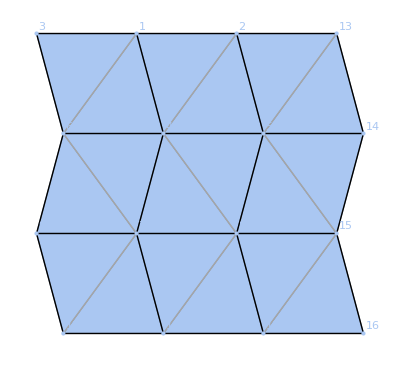

```mathematica
m2=tesselateMechanism[m,{{1/2,0,0},{0,1,0}},{2,1}]
```

```mathematica
?deleteVertices
```

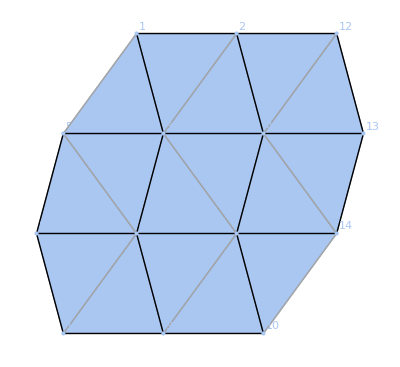

```mathematica
m3=deleteVertices[m2,{3,16}]
```

```mathematica
?identificationRules
```

```mathematica
pd=identificationRules[m3,{f1,#+{1,0,0}&},{f2,#+{0,1,0}&}]
```

periodicData[{f1,f2}]

```mathematica
simplestConstraints=With[{eq=constraintEquations[m3,1]//.Flatten[Thread/@periodicityRules[m3,pd,{vertexDisplacement[#,All[3]]&,vertexDisplacement[#,All[3]]&},{ #&, #&}]]},
GroebnerBasis[eq,Variables[eq]]
]
```

{-vertexDisplacement[9,y]+vertexDisplacement[11,y],vertexDisplacement[9,x]-vertexDisplacement[11,x],-vertexDisplacement[8,y]+vertexDisplacement[11,y],vertexDisplacement[8,x]-vertexDisplacement[11,x],vertexDisplacement[6,y]-vertexDisplacement[11,y],vertexDisplacement[6,x]-vertexDisplacement[11,x]}

```mathematica
{lin,quad}=Chop[infinitesimalMotions[N[m3],"variables"->h,"constraints"->Join[simplestConstraints,Flatten[{vertexDisplacement[1,{"x","y","z"}],vertexDisplacement[2,{"y","z"}],vertexDisplacement[3,"z"]}]]]];
```

```mathematica
lin
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0.46394 h[1]-0.566192 h[2]-0.0455874 h[3]-0.055792 h[4]+0.116742 h[8]-0.0122088 h[9]+0.667246 h[10]},{0,0,-0.820869 h[1]-0.256253 h[2]+0.0768622 h[3]+0.167308 h[4]-0.230656 h[8]+0.0469398 h[9]+0.413767 h[10]},{0,0,0.177064 h[1]+0.242383 h[2]+0.265148 h[3]+0.476084 h[4]-0.0248493 h[8]+0.766217 h[9]+0.158851 h[10]},{0,0,0.114048 h[1]-0.529729 h[2]+0.369531 h[3]+0.54912 h[4]-0.132321 h[8]-0.241149 h[9]-0.4389 h[10]},{0,0,0.102949 h[1]+0.0868712 h[2]-0.787464 h[3]+0.50359 h[4]-0.306918 h[8]-0.110359 h[9]+0.04212 h[10]},{0,0,-0.172564 h[1]-0.494121 h[2]-0.404314 h[3]-0.167919 h[4]+0.319985 h[8]+0.531092 h[9]-0.387234 h[10]},{0,0,-0.161858 h[1]+0.150652 h[2]-0.0398488 h[3]+0.398631 h[4]+0.847617 h[8]-0.241182 h[9]+0.118273 h[10]},{0,0,-0.999866 h[5]-0.0163665 h[6]},{0,0,0.0163665 h[5]-0.999866 h[6]},{0,0,1. h[7]},{0,0,1. h[11]}}

```mathematica
Length[quad]
```

10

```mathematica
NSolve[Join[quad,{(h/@Range[11]).(h/@Range[11])-1}]==0,h/@Range[11]]
```

{}

## Examples

### simple example

This is the simplest non-trivial example of a mechanism.

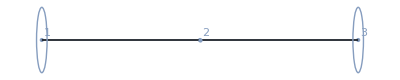

```mathematica
m=framework[{
{-1,0},{0,0},{1,0}
},{
Property[joint[1],MeshCellShapeFunction->(Circle[#,1/30]&)],
Property[joint[3],MeshCellShapeFunction->(Circle[#,1/30]&)],
rigidBar[{1,2}],rigidBar[{2,3}]
},
MeshCellLabel->{0->"Index"}
]
```

```mathematica
infinitesimalMotions[m,"variables"->v]
```

{{{0,0},{0,v[1]},{0,0}},{√(2/5) v[1]^2}}

```mathematica
allEquations=constraintEquations[m,Infinity]/.{
vertexDisplacement[1,_]->0,
vertexDisplacement[3,_]->0
}
```

{0,0,0,0,-1+(1+vertexDisplacement[2,x])^2+vertexDisplacement[2,y]^2,-1+(1-vertexDisplacement[2,x])^2+vertexDisplacement[2,y]^2}

```mathematica
vectorField=FullSimplify[Expand[allEquations[[{5,6}]]/.{vertexDisplacement[2,"x"]->x,vertexDisplacement[2,"y"]->y}]]
```

{x (2+x)+y^2,(-2+x) x+y^2}

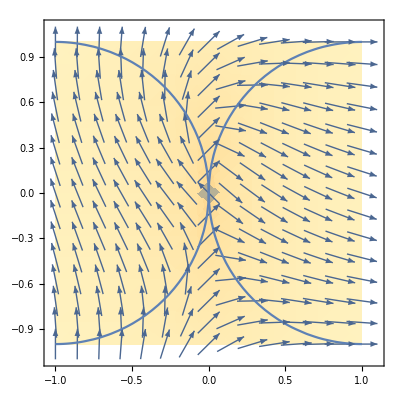

```mathematica
Show[
DensityPlot[Log[vectorField . vectorField],{x,-1,1},{y,-1,1},PlotRange->All],
VectorPlot[vectorField/Sqrt[vectorField . vectorField],{x,-1,1},{y,-1,1}],
ContourPlot[vectorField[[1]]==0,{x,-1,1},{y,-1,1}],
ContourPlot[vectorField[[2]]==0,{x,-1,1},{y,-1,1}]
]
```

```mathematica
vectorField/.{x->0,y->0}
```

{0,0}

```mathematica
D[vectorField,{{x,y}}]/.{x->0,y->0}
```

{{2,0},{-2,0}}

```mathematica
expr=FullSimplify[D[ArcTan@@(vectorField/.{x->r Cos[t],y->r Sin[t]}),t],r>0]
```

(2 r Sin[t])/(2+r^2+2 Cos[2 t])

```mathematica
NIntegrate[expr/.r->0.01,{t,0,2Pi},MaxRecursion->100]/(2 Pi)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.16417×10^-14 and 2.36813×10^-13 for the integral and error estimates.

1.85284×10^-15

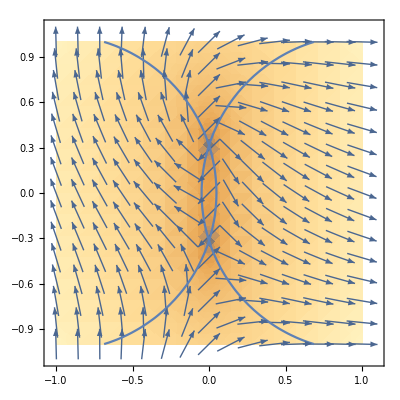

```mathematica
vectorField2=vectorField-{1/10,1/10};
Show[
DensityPlot[Log[vectorField2. vectorField2],{x,-1,1},{y,-1,1},PlotRange->All],
VectorPlot[vectorField2/Sqrt[vectorField2 . vectorField2],{x,-1,1},{y,-1,1}],
ContourPlot[vectorField2[[1]]==0,{x,-1,1},{y,-1,1}],
ContourPlot[vectorField2[[2]]==0,{x,-1,1},{y,-1,1}]
]
```

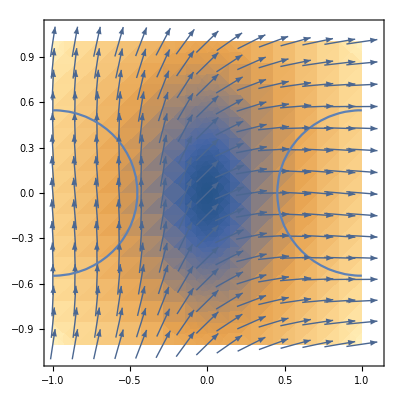

```mathematica
vectorField2=vectorField+{7/10,7/10};
Show[
DensityPlot[Log[vectorField2. vectorField2],{x,-1,1},{y,-1,1},PlotRange->All],
VectorPlot[vectorField2/Sqrt[vectorField2 . vectorField2],{x,-1,1},{y,-1,1}],
ContourPlot[vectorField2[[1]]==0,{x,-1,1},{y,-1,1}],
ContourPlot[vectorField2[[2]]==0,{x,-1,1},{y,-1,1}]
]
```

```mathematica
Solve[vectorField2==0,{x,y}]
```

{{x→0,y→-1/(√10)},{x→0,y→1/(√10)}}

```mathematica
Det/@(D[vectorField2,{{x,y}}]/.Solve[vectorField2==0,{x,y}])
```

{-4 √(2/5),4 √(2/5)}

```mathematica
expr=FullSimplify[D[ArcTan@@(vectorField2/.{x->r Cos[t],y->(1/Sqrt[10]+r Sin[t])}),t],r>0];
NIntegrate[expr/.r->0.01,{t,0,2Pi}]/(2 Pi)
```

1.

```mathematica
expr=FullSimplify[D[ArcTan@@(vectorField2/.{x->r Cos[t],y->(-1/Sqrt[10]+r Sin[t])}),t],r>0];
NIntegrate[expr/.r->0.01,{t,0,2Pi}]/(2 Pi)
```

-1.

### Watt mechanism

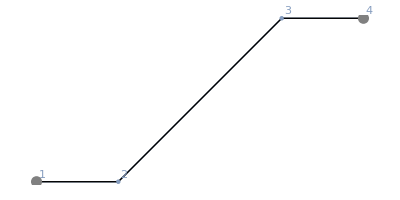

```mathematica
m=framework[{
 {-1,0},{-1/2,0},{1/2,1},{1,1}
},
{
joint[1],
joint[4],
rigidBar[{1,2}],rigidBar[{2,3}],rigidBar[{3,4}]
},
MeshCellLabel->{0->"Index"}
]
```

```mathematica
Options[infinitesimalMotions]
```

{constraints→None,variables→Automatic,Method→Automatic,Modulus→0,Tolerance→Automatic,ZeroTest→Automatic}

```mathematica
infinitesimalMotions[m,"variables"->v]
```

{{{0,0},{0,v[1]/(√2)},{0,v[1]/(√2)},{0,0}},{}}

```mathematica
?isometricTrajectory
```

```mathematica
listEdges[m,{1}]
```

{{{1,2}}}

```mathematica
compatibilityMatrix[m]//MatrixForm
```

(-1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | -2 | 2 | 2 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 1 | 0)

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

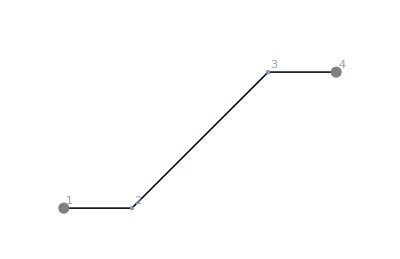
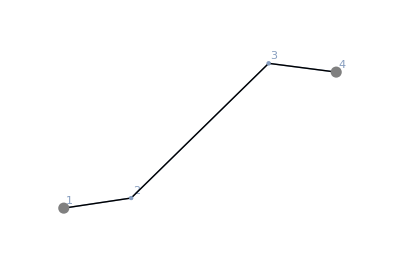
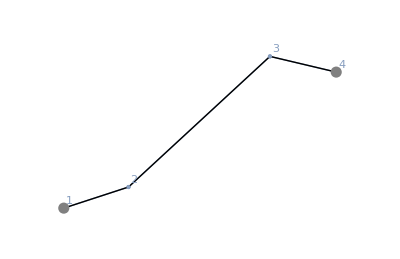
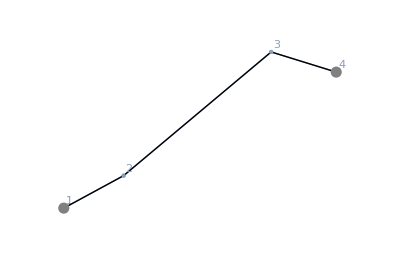
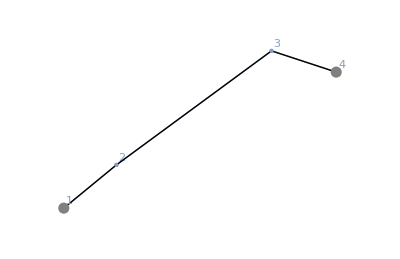
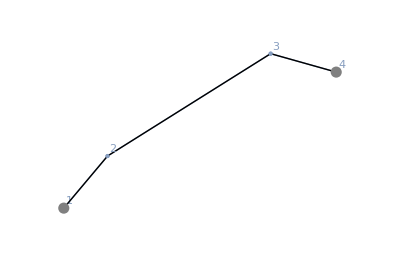
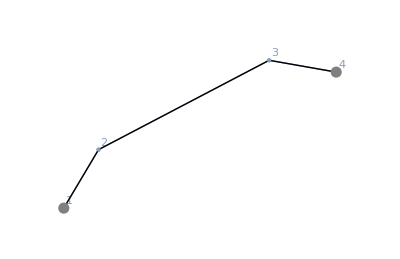
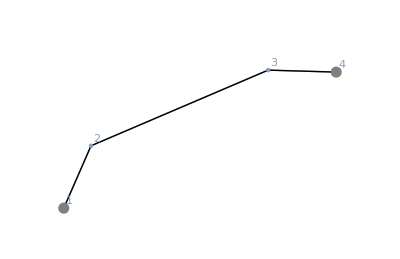

```mathematica
plotMechanism[m,isometricTrajectory[m, {{0,0},{0,1},{0,0},{0,0}}, 10]]
```

```mathematica
Dimensions[isometricTrajectory[m,
D[infinitesimalMotions[m,"variables"->v][[1]],v[1]],
50
]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

{51,4,2}

```mathematica
ListAnimate[plotMechanism[m,
isometricTrajectory[m,
D[infinitesimalMotions[m,"variables"->v][[1]],v[1]],
50
]
]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

### 3rd order

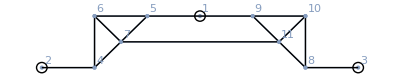

```mathematica
m=framework[{
{0,1},{-3,0},{3,0},
{-2,0},{-1,1},{-2,1},{-3/2,1/2},
{2,0},{1,1},{2,1},{3/2,1/2}
},{
Property[joint[1],MeshCellShapeFunction->(Circle[#,1/10]&)],
Property[joint[2],MeshCellShapeFunction->(Circle[#,1/10]&)],
Property[joint[3],MeshCellShapeFunction->(Circle[#,1/10]&)],

(*left mechanism*)
rigidBar[{2,4}],rigidBar[{4,6}],rigidBar[{6,5}],rigidBar[{4,7}],rigidBar[{7,5}],rigidBar[{6,7}],rigidBar[{5,1}],

(*right mechanism*)
rigidBar[{1,9}],rigidBar[{9,10}],rigidBar[{10,8}],rigidBar[{8,11}],rigidBar[{9,11}],rigidBar[{11,10}],rigidBar[{8,3}],

rigidBar[{7,11}]
},
MeshCellLabel->{0->"Index"}
]
```

```mathematica
{linear,quadratic}=infinitesimalMotions[m,"variables"->v]
```

{{{0,0},{0,0},{0,0},{0,v[2]/2},{0,v[2]/2},{0,v[2]/2},{0,v[2]/2},{0,v[1]/2},{0,v[1]/2},{0,v[1]/2},{0,v[1]/2}},{v[1]^2/(4 √73)-(v[1] v[2])/(2 √73)+v[2]^2/(4 √73)}}